### 4 (3a + 1s) case

```mathematica
Solve[A1*x+B1*y+C1*z+D1*w==0,x]
```

{{x→(-B1 y-C1 z-D1 w)/A1}}

```mathematica
x=(-D1 w-B1 y-C1 z)/A1
```

(-B1 y-C1 z-D1 w)/A1

```mathematica
Solve[A2*x+B2*y+C2*z+D2*w==0,y]
```

{{y→(-A1 C2 z-A1 D2 w+A2 C1 z+A2 D1 w)/(A1 B2-A2 B1)}}

```mathematica
y=(A2 D1 w-A1 D2 w+A2 C1 z-A1 C2 z)/(-A2 B1+A1 B2)
```

(-A1 C2 z-A1 D2 w+A2 C1 z+A2 D1 w)/(A1 B2-A2 B1)

```mathematica
Solve[A3*x+B3*y+C3*z+D3*w==0,z]
```

{{z→((A2 A3 B1 D1 w)/(A1 (A1 B2-A2 B1))-(A3 B1 D2 w)/(A1 B2-A2 B1)-(A2 B3 D1 w)/(A1 B2-A2 B1)+(A1 B3 D2 w)/(A1 B2-A2 B1)+(A3 D1 w)/A1-D3 w)/(-(A2 A3 B1 C1)/(A1 (A1 B2-A2 B1))+(A3 B1 C2)/(A1 B2-A2 B1)+(A2 B3 C1)/(A1 B2-A2 B1)-(A1 B3 C2)/(A1 B2-A2 B1)-(A3 C1)/A1+C3)}}

```mathematica
z=((A3 D1 w)/A1+(A2 A3 B1 D1 w)/(A1 (-A2 B1+A1 B2))-(A2 B3 D1 w)/(-A2 B1+A1 B2)-(A3 B1 D2 w)/(-A2 B1+A1 B2)+(A1 B3 D2 w)/(-A2 B1+A1 B2)-D3 w)/(-(A3 C1)/A1-(A2 A3 B1 C1)/(A1 (-A2 B1+A1 B2))+(A2 B3 C1)/(-A2 B1+A1 B2)+(A3 B1 C2)/(-A2 B1+A1 B2)-(A1 B3 C2)/(-A2 B1+A1 B2)+C3)//Simplify
```

(w (-A1 B2 D3+A1 B3 D2+A2 B1 D3-A2 B3 D1-A3 B1 D2+A3 B2 D1))/(A1 B2 C3-A1 B3 C2-A2 B1 C3+A2 B3 C1+A3 B1 C2-A3 B2 C1)

```mathematica
y //Simplify
```

(w (A1 C2 D3-A1 C3 D2-A2 C1 D3+A2 C3 D1+A3 C1 D2-A3 C2 D1))/(A1 B2 C3-A1 B3 C2-A2 B1 C3+A2 B3 C1+A3 B1 C2-A3 B2 C1)

```mathematica
x //Simplify
```

(w (-B1 C2 D3+B1 C3 D2+B2 C1 D3-B2 C3 D1-B3 C1 D2+B3 C2 D1))/(A1 B2 C3-A1 B3 C2-A2 B1 C3+A2 B3 C1+A3 B1 C2-A3 B2 C1)

```mathematica
xs=x/w//Simplify//Numerator
zs=z/w//Simplify//Numerator
ys=y/w//Simplify//Numerator
ws=z //Simplify //Denominator
```

-B1 C2 D3+B1 C3 D2+B2 C1 D3-B2 C3 D1-B3 C1 D2+B3 C2 D1

-A1 B2 D3+A1 B3 D2+A2 B1 D3-A2 B3 D1-A3 B1 D2+A3 B2 D1

-A1 C2 D3+A1 C3 D2+A2 C1 D3-A2 C3 D1-A3 C1 D2+A3 C2 D1

A1 B2 C3-A1 B3 C2-A2 B1 C3+A2 B3 C1+A3 B1 C2-A3 B2 C1

```mathematica
w1=ws/.{A1->a11-lami,A2->a12,A3->a13,B1->Conjugate[a12],B2->a22-lami,B3->a23,C1->Conjugate[a13],C2->Conjugate[a23],C3->a33-lami}
```

(a11-lami) (a22-lami) (a33-lami)-a23 (a11-lami) Conjugate[a23]+a12 a23 Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a12 Conjugate[a12] (a33-lami)-a13 Conjugate[a13] (a22-lami)

```mathematica
z1=zs/.{A1->a11-lami,A2->a12,A3->a13,B1->Conjugate[a12],B2->a22-lami,B3->a23,C1->Conjugate[a13],C2->Conjugate[a23],C3->a33-lami,D1->Conjugate[a14],D2->Conjugate[a24],D3->Conjugate[a34]}
```

-(a11-lami) (a22-lami) Conjugate[a34]+a23 (a11-lami) Conjugate[a24]-a13 Conjugate[a12] Conjugate[a24]-a12 a23 Conjugate[a14]+a12 Conjugate[a12] Conjugate[a34]+a13 Conjugate[a14] (a22-lami)

```mathematica
y1=ys/.{A1->a11-lami,A2->a12,A3->a13,B1->Conjugate[a12],B2->a22-lami,B3->a23,C1->Conjugate[a13],C2->Conjugate[a23],C3->a33-lami,D1->Conjugate[a14],D2->Conjugate[a24],D3->Conjugate[a34]}
```

-(a11-lami) Conjugate[a23] Conjugate[a34]+(a11-lami) Conjugate[a24] (a33-lami)+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33-lami)+a13 Conjugate[a14] Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]

```mathematica
x1= xs/.{A1->a11-lami,A2->a12,A3->a13,B1->Conjugate[a12],B2->a22-lami,B3->a23,C1->Conjugate[a13],C2->Conjugate[a23],C3->a33-lami,D1->Conjugate[a14],D2->Conjugate[a24],D3->Conjugate[a34]}
```

-Conjugate[a12] Conjugate[a23] Conjugate[a34]+Conjugate[a12] Conjugate[a24] (a33-lami)+Conjugate[a13] (a22-lami) Conjugate[a34]-a23 Conjugate[a13] Conjugate[a24]-(Conjugate[a14] (a22-lami) (a33-lami))+a23 Conjugate[a14] Conjugate[a23]

```mathematica
Uvec = {x1,y1,z1,w1}
```

{-Conjugate[a12] Conjugate[a23] Conjugate[a34]+Conjugate[a12] Conjugate[a24] (a33-lami)+Conjugate[a13] (a22-lami) Conjugate[a34]-a23 Conjugate[a13] Conjugate[a24]-(Conjugate[a14] (a22-lami) (a33-lami))+a23 Conjugate[a14] Conjugate[a23],-(a11-lami) Conjugate[a23] Conjugate[a34]+(a11-lami) Conjugate[a24] (a33-lami)+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33-lami)+a13 Conjugate[a14] Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24],-(a11-lami) (a22-lami) Conjugate[a34]+a23 (a11-lami) Conjugate[a24]-a13 Conjugate[a12] Conjugate[a24]-a12 a23 Conjugate[a14]+a12 Conjugate[a12] Conjugate[a34]+a13 Conjugate[a14] (a22-lami),(a11-lami) (a22-lami) (a33-lami)-a23 (a11-lami) Conjugate[a23]+a12 a23 Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a12 Conjugate[a12] (a33-lami)-a13 Conjugate[a13] (a22-lami)}

```mathematica
Uvec={(-Conjugate[a12])*Conjugate[a23]*Conjugate[a34] + 
   Conjugate[a12]*Conjugate[a24]*(a33[x] - lami[x]) + 
   Conjugate[a13]*(a22[x] - lami[x])*Conjugate[a34] - 
   a23*Conjugate[a13]*Conjugate[a24] - 
   Conjugate[a14]*(a22[x] - lami[x])*(a33[x] - lami[x]) + 
   a23*Conjugate[a14]*Conjugate[a23], 
  (lami[x] - a11[x])*Conjugate[a23]*Conjugate[a34] + 
   (a11[x] - lami[x])*Conjugate[a24]*(a33[x] - lami[x]) + 
   a12*Conjugate[a13]*Conjugate[a34] - 
   a12*Conjugate[a14]*(a33[x] - lami[x]) + 
   a13*Conjugate[a14]*Conjugate[a23] - 
   a13*Conjugate[a13]*Conjugate[a24], 
  (lami[x] - a11[x])*(a22[x] - lami[x])*Conjugate[a34] + 
   a23*(a11[x] - lami[x])*Conjugate[a24] - 
   a13*Conjugate[a12]*Conjugate[a24] - 
   a12*a23*Conjugate[a14] + a12*Conjugate[a12]*
    Conjugate[a34] + a13*Conjugate[a14]*
    (a22[x] - lami[x]), (a11[x] - lami[x])*(a22[x] - lami[x])*
    (a33[x] - lami[x]) - a23*(a11[x] - lami[x])*
    Conjugate[a23] + a12*a23*Conjugate[a13] + 
   a13*Conjugate[a12]*Conjugate[a23] - 
   a12*Conjugate[a12]*(a33[x] - lami[x]) - 
   a13*Conjugate[a13]*(a22[x] - lami[x])}
```

{-Conjugate[a12] Conjugate[a23] Conjugate[a34]+Conjugate[a12] Conjugate[a24] (a33(x)-lami(x))+Conjugate[a13] Conjugate[a34] (a22(x)-lami(x))-a23 Conjugate[a13] Conjugate[a24]-Conjugate[a14] (a22(x)-lami(x)) (a33(x)-lami(x))+a23 Conjugate[a14] Conjugate[a23],Conjugate[a23] Conjugate[a34] (lami(x)-a11(x))+Conjugate[a24] (a11(x)-lami(x)) (a33(x)-lami(x))+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33(x)-lami(x))+a13 Conjugate[a14] Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24],Conjugate[a34] (lami(x)-a11(x)) (a22(x)-lami(x))+a23 Conjugate[a24] (a11(x)-lami(x))-a13 Conjugate[a12] Conjugate[a24]-a12 a23 Conjugate[a14]+a12 Conjugate[a12] Conjugate[a34]+a13 Conjugate[a14] (a22(x)-lami(x)),(a11(x)-lami(x)) (a22(x)-lami(x)) (a33(x)-lami(x))-a23 Conjugate[a23] (a11(x)-lami(x))+a12 a23 Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a12 Conjugate[a12] (a33(x)-lami(x))-a13 Conjugate[a13] (a22(x)-lami(x))}

```mathematica
dUvec=D[Uvec,x];
expr=Simplify[Uvec.Conjugate[dUvec]]
```

(Conjugate[a34] (lami(x)-a11(x)) (a22(x)-lami(x))+a23 Conjugate[a24] (a11(x)-lami(x))-a13 Conjugate[a12] Conjugate[a24]-a12 a23 Conjugate[a14]+a12 Conjugate[a12] Conjugate[a34]+a13 Conjugate[a14] (a22(x)-lami(x))) Conjugate[(a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))]+(Conjugate[a23] Conjugate[a34] (lami(x)-a11(x))+Conjugate[a24] (a11(x)-lami(x)) (a33(x)-lami(x))+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33(x)-lami(x))+a13 Conjugate[a14] Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]) (Conjugate[(Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x)))]+a23 a34 (Conjugate[lami'(x)]-Conjugate[a11'(x)]))+((a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x))-a23 Conjugate[a23] (a11(x)-lami(x))+a12 a23 Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a12 Conjugate[a12] (a33(x)-lami(x))-a13 Conjugate[a13] (a22(x)-lami(x))) Conjugate[(-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))]+(-Conjugate[a12] Conjugate[a23] Conjugate[a34]+Conjugate[a12] Conjugate[a24] (a33(x)-lami(x))+Conjugate[a13] Conjugate[a34] (a22(x)-lami(x))-a23 Conjugate[a13] Conjugate[a24]+Conjugate[a14] (a22(x)-lami(x)) (lami(x)-a33(x))+a23 Conjugate[a14] Conjugate[a23]) (a12 a24 (Conjugate[a33'(x)]-Conjugate[lami'(x)])+a13 a34 (Conjugate[a22'(x)]-Conjugate[lami'(x)])-a14 Conjugate[((a33(x)-lami(x)) (a22'(x)-lami'(x))+(a22(x)-lami(x)) (a33'(x)-lami'(x)))])

```mathematica
expr2=expr-Conjugate[expr]//Simplify
```

(Conjugate[(Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x)))]+a23 a34 (Conjugate[lami'(x)]-Conjugate[a11'(x)])) (a13 Conjugate[a14] Conjugate[a23]+Conjugate[a34] (lami(x)-a11(x)) Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33(x)-lami(x))+Conjugate[a24] (a11(x)-lami(x)) (a33(x)-lami(x)))+Conjugate[(a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))] (-a12 a23 Conjugate[a14]+a13 (a22(x)-lami(x)) Conjugate[a14]-a13 Conjugate[a12] Conjugate[a24]+a12 Conjugate[a12] Conjugate[a34]+a23 Conjugate[a24] (a11(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))+(-a14 Conjugate[((a33(x)-lami(x)) (a22'(x)-lami'(x))+(a22(x)-lami(x)) (a33'(x)-lami'(x)))]+a13 a34 (Conjugate[a22'(x)]-Conjugate[lami'(x)])+a12 a24 (Conjugate[a33'(x)]-Conjugate[lami'(x)])) (a23 Conjugate[a14] Conjugate[a23]-Conjugate[a12] Conjugate[a34] Conjugate[a23]-a23 Conjugate[a13] Conjugate[a24]+Conjugate[a13] Conjugate[a34] (a22(x)-lami(x))+Conjugate[a12] Conjugate[a24] (a33(x)-lami(x))+Conjugate[a14] (a22(x)-lami(x)) (lami(x)-a33(x)))+Conjugate[(-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))] (a12 a23 Conjugate[a13]-a13 (a22(x)-lami(x)) Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a23 Conjugate[a23] (a11(x)-lami(x))-a12 Conjugate[a12] (a33(x)-lami(x))+(a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x)))-(-a12 a23 a34+a13 (Conjugate[a22(x)]-Conjugate[lami(x)]) a34+a14 a23 Conjugate[a23]-a13 a24 Conjugate[a23]+a12 a24 (Conjugate[a33(x)]-Conjugate[lami(x)])+a14 (Conjugate[a22(x)]-Conjugate[lami(x)]) (Conjugate[lami(x)]-Conjugate[a33(x)])) (-Conjugate[a14] ((a33(x)-lami(x)) (a22'(x)-lami'(x))+(a22(x)-lami(x)) (a33'(x)-lami'(x)))+Conjugate[(a13 a34)] (a22'(x)-lami'(x))+Conjugate[(a12 a24)] (a33'(x)-lami'(x)))-(a12 a23 Conjugate[a13]+a13 Conjugate[(a12 a23)]-Conjugate[(a23 Conjugate[a23] (a11(x)-lami(x))-(lami(x)-a22(x)) (lami(x)-a33(x)) (a11(x)-lami(x))+a13 Conjugate[a13] (a22(x)-lami(x))+a12 Conjugate[a12] (a33(x)-lami(x)))]) (-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))-(a13 a34 Conjugate[a12]+a14 a23 Conjugate[a13]-a13 a24 Conjugate[a13]+a23 a34 (Conjugate[lami(x)]-Conjugate[a11(x)])+(Conjugate[lami(x)]-Conjugate[a33(x)]) (a14 Conjugate[a12]+a24 (Conjugate[lami(x)]-Conjugate[a11(x)]))) (Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x))+Conjugate[(a23 a34)] (lami'(x)-a11'(x)))-(a12 a34 Conjugate[a12]-a12 a24 Conjugate[a13]-a14 Conjugate[(a12 a23)]+Conjugate[(a23 Conjugate[a24] (a11(x)-lami(x))+a13 Conjugate[a14] (a22(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))]) (a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))

```mathematica
expr21=Simplify[expr2,Assumptions->{Element[a11[x],Reals],Element[a22[x],Reals],Element[a33[x],Reals],Element[lami[x],Reals],Element[Ni,Reals]}]//Simplify
```

Conjugate[(a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))] (-a12 a23 Conjugate[a14]+a13 (a22(x)-lami(x)) Conjugate[a14]-a13 Conjugate[a12] Conjugate[a24]+a12 Conjugate[a12] Conjugate[a34]+a23 Conjugate[a24] (a11(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))+Conjugate[(-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))] (a12 a23 Conjugate[a13]-a13 (a22(x)-lami(x)) Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a23 Conjugate[a23] (a11(x)-lami(x))-a12 Conjugate[a12] (a33(x)-lami(x))+(a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x)))-(-a12 a23 a34+a13 (a22(x)-lami(x)) a34+a14 a23 Conjugate[a23]-a13 a24 Conjugate[a23]+a12 a24 (a33(x)-lami(x))+a14 (a22(x)-lami(x)) (lami(x)-a33(x))) (-Conjugate[a14] ((a33(x)-lami(x)) (a22'(x)-lami'(x))+(a22(x)-lami(x)) (a33'(x)-lami'(x)))+Conjugate[(a13 a34)] (a22'(x)-lami'(x))+Conjugate[(a12 a24)] (a33'(x)-lami'(x)))-(a12 a23 Conjugate[a13]+a13 Conjugate[(a12 a23)]-Conjugate[(a23 Conjugate[a23] (a11(x)-lami(x))+a13 Conjugate[a13] (a22(x)-lami(x))+a12 Conjugate[a12] (a33(x)-lami(x)))]+(a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x))) (-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))+(a23 Conjugate[a14] Conjugate[a23]-Conjugate[a12] Conjugate[a34] Conjugate[a23]-a23 Conjugate[a13] Conjugate[a24]+Conjugate[a13] Conjugate[a34] (a22(x)-lami(x))+Conjugate[a12] Conjugate[a24] (a33(x)-lami(x))+Conjugate[a14] (a22(x)-lami(x)) (lami(x)-a33(x))) ((a13 a34-a14 a33(x)+a14 lami(x)) a22'(x)+(a12 a24-a14 a22(x)+a14 lami(x)) a33'(x)+(-a12 a24-a13 a34+a14 a22(x)+a14 a33(x)-2 a14 lami(x)) lami'(x))+(a13 Conjugate[a14] Conjugate[a23]+Conjugate[a34] (lami(x)-a11(x)) Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33(x)-lami(x))+Conjugate[a24] (a11(x)-lami(x)) (a33(x)-lami(x))) (Conjugate[(Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x)))]+a23 a34 (lami'(x)-a11'(x)))-(a13 a34 Conjugate[a12]+a14 a23 Conjugate[a13]-a13 a24 Conjugate[a13]+a23 a34 (lami(x)-a11(x))+(lami(x)-a33(x)) (-a24 a11(x)+a14 Conjugate[a12]+a24 lami(x))) (Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x))+Conjugate[(a23 a34)] (lami'(x)-a11'(x)))-(a12 a34 Conjugate[a12]-a12 a24 Conjugate[a13]-a14 Conjugate[(a12 a23)]+Conjugate[(a23 Conjugate[a24] (a11(x)-lami(x))+a13 Conjugate[a14] (a22(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))]) (a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))

```mathematica
expr21/.{D[lami[x],x]->0}
```

(a24 Conjugate[(a23 a11'(x))]+a14 Conjugate[(a13 a22'(x))]+Conjugate[(Conjugate[a34] (lami(x)-a11(x)) a22'(x)-Conjugate[a34] (a22(x)-lami(x)) a11'(x))]) (-a12 a23 Conjugate[a14]+a13 (a22(x)-lami(x)) Conjugate[a14]-a13 Conjugate[a12] Conjugate[a24]+a12 Conjugate[a12] Conjugate[a34]+a23 Conjugate[a24] (a11(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))+(-a23 Conjugate[(a23 a11'(x))]-a13 Conjugate[(a13 a22'(x))]-a12 Conjugate[(a12 a33'(x))]+Conjugate[((a22(x)-lami(x)) (a33(x)-lami(x)) a11'(x)+(a11(x)-lami(x)) (a33(x)-lami(x)) a22'(x)+(a11(x)-lami(x)) (a22(x)-lami(x)) a33'(x))]) (a12 a23 Conjugate[a13]-a13 (a22(x)-lami(x)) Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a23 Conjugate[a23] (a11(x)-lami(x))-a12 Conjugate[a12] (a33(x)-lami(x))+(a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x)))+(a13 Conjugate[a14] Conjugate[a23]+Conjugate[a34] (lami(x)-a11(x)) Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33(x)-lami(x))+Conjugate[a24] (a11(x)-lami(x)) (a33(x)-lami(x))) (-a14 Conjugate[(a12 a33'(x))]+Conjugate[(Conjugate[a24] (a33(x)-lami(x)) a11'(x)+Conjugate[a24] (a11(x)-lami(x)) a33'(x))]-a23 a34 a11'(x))-(a12 a34 Conjugate[a12]-a12 a24 Conjugate[a13]-a14 Conjugate[(a12 a23)]+Conjugate[(a23 Conjugate[a24] (a11(x)-lami(x))+a13 Conjugate[a14] (a22(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))]) (a23 Conjugate[a24] a11'(x)-Conjugate[a34] (a22(x)-lami(x)) a11'(x)+a13 Conjugate[a14] a22'(x)+Conjugate[a34] (lami(x)-a11(x)) a22'(x))-(a13 a34 Conjugate[a12]+a14 a23 Conjugate[a13]-a13 a24 Conjugate[a13]+a23 a34 (lami(x)-a11(x))+(lami(x)-a33(x)) (-a24 a11(x)+a14 Conjugate[a12]+a24 lami(x))) (-Conjugate[(a23 a34)] a11'(x)+Conjugate[a24] (a33(x)-lami(x)) a11'(x)-a12 Conjugate[a14] a33'(x)+Conjugate[a24] (a11(x)-lami(x)) a33'(x))-(a12 a23 Conjugate[a13]+a13 Conjugate[(a12 a23)]-Conjugate[(a23 Conjugate[a23] (a11(x)-lami(x))+a13 Conjugate[a13] (a22(x)-lami(x))+a12 Conjugate[a12] (a33(x)-lami(x)))]+(a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x))) (-a23 Conjugate[a23] a11'(x)+(a22(x)-lami(x)) (a33(x)-lami(x)) a11'(x)-a13 Conjugate[a13] a22'(x)+(a11(x)-lami(x)) (a33(x)-lami(x)) a22'(x)-a12 Conjugate[a12] a33'(x)+(a11(x)-lami(x)) (a22(x)-lami(x)) a33'(x))+(a23 Conjugate[a14] Conjugate[a23]-Conjugate[a12] Conjugate[a34] Conjugate[a23]-a23 Conjugate[a13] Conjugate[a24]+Conjugate[a13] Conjugate[a34] (a22(x)-lami(x))+Conjugate[a12] Conjugate[a24] (a33(x)-lami(x))+Conjugate[a14] (a22(x)-lami(x)) (lami(x)-a33(x))) ((a13 a34-a14 a33(x)+a14 lami(x)) a22'(x)+(a12 a24-a14 a22(x)+a14 lami(x)) a33'(x))-(-a12 a23 a34+a13 (a22(x)-lami(x)) a34+a14 a23 Conjugate[a23]-a13 a24 Conjugate[a23]+a12 a24 (a33(x)-lami(x))+a14 (a22(x)-lami(x)) (lami(x)-a33(x))) (Conjugate[(a13 a34)] a22'(x)+Conjugate[(a12 a24)] a33'(x)-Conjugate[a14] ((a33(x)-lami(x)) a22'(x)+(a22(x)-lami(x)) a33'(x)))

```mathematica
cexpr = ComplexExpand[expr2,{a12,a13,a14,a23,a24,a34}];
```

```mathematica
cexpr2=Collect[cexpr,{a11'[x],a22'[x],a33'[x]}]
```

ⅈ (-2 Im(a13) Im(a14) Im(a34) (a22(x))^2-2 Im(a34) Re(a13) Re(a14) (a22(x))^2+2 Im(a14) Re(a13) Re(a34) (a22(x))^2-2 Im(a13) Re(a14) Re(a34) (a22(x))^2+4 Im(a13) Im(a14) Im(a34) lami(x) a22(x)+2 Im(a14) Im(a23) Im(a34) Re(a12) a22(x)+2 Im(a13) Im(a24) Im(a34) Re(a12) a22(x)-2 Im(a14) Im(a23) Im(a24) Re(a13) a22(x)-2 Im(a12) Im(a24) Im(a34) Re(a13) a22(x)+2 Im(a13) Im(a23) Im(a24) Re(a14) a22(x)-2 Im(a12) Im(a23) Im(a34) Re(a14) a22(x)+4 Im(a34) lami(x) Re(a13) Re(a14) a22(x)+2 Im(a13) Im(a14) Im(a24) Re(a23) a22(x)+2 Im(a12) Im(a14) Im(a34) Re(a23) a22(x)+2 Im(a34) Re(a12) Re(a14) Re(a23) a22(x)+2 Im(a24) Re(a13) Re(a14) Re(a23) a22(x)-2 Im(a13) Im(a14) Im(a23) Re(a24) a22(x)+2 Im(a12) Im(a13) Im(a34) Re(a24) a22(x)+2 Im(a34) Re(a12) Re(a13) Re(a24) a22(x)-2 Im(a23) Re(a13) Re(a14) Re(a24) a22(x)-2 Im(a14) Re(a13) Re(a23) Re(a24) a22(x)+2 Im(a13) Re(a14) Re(a23) Re(a24) a22(x)+2 Im(a12) Im(a14) Im(a23) Re(a34) a22(x)-2 Im(a12) Im(a13) Im(a24) Re(a34) a22(x)-4 Im(a14) lami(x) Re(a13) Re(a34) a22(x)-2 Im(a24) Re(a12) Re(a13) Re(a34) a22(x)+4 Im(a13) lami(x) Re(a14) Re(a34) a22(x)+2 Im(a23) Re(a12) Re(a14) Re(a34) a22(x)-2 Im(a14) Re(a12) Re(a23) Re(a34) a22(x)+2 Im(a12) Re(a14) Re(a23) Re(a34) a22(x)+2 Im(a13) Re(a12) Re(a24) Re(a34) a22(x)-2 Im(a12) Re(a13) Re(a24) Re(a34) a22(x)+2 Im(a12) Im(a13) Im(a23) (Im(a24))^2-2 Im(a12) Im(a13) Im(a23) (Im(a34))^2-2 Im(a12) Im(a14) Im(a24) (lami(x))^2-2 Im(a13) Im(a14) Im(a34) (lami(x))^2-2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a12) Im(a14) Im(a24) (Re(a23))^2-2 Im(a13) Im(a14) Im(a34) (Re(a23))^2-2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a12) Im(a13) Im(a23) (Re(a24))^2+2 Im(a23) Re(a12) Re(a13) (Re(a24))^2-2 Im(a13) Re(a12) Re(a23) (Re(a24))^2+2 Im(a12) Re(a13) Re(a23) (Re(a24))^2-2 Im(a12) Im(a13) Im(a23) (Re(a34))^2-2 Im(a23) Re(a12) Re(a13) (Re(a34))^2+2 Im(a13) Re(a12) Re(a23) (Re(a34))^2-2 Im(a12) Re(a13) Re(a23) (Re(a34))^2-2 Im(a12) Im(a14) (Im(a23))^2 Im(a24)-2 (a33(x))^2 Im(a12) Im(a14) Im(a24)-2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)-2 (Im(a12))^2 Im(a23) Im(a24) Im(a34)+2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)+4 a33(x) Im(a12) Im(a14) Im(a24) lami(x)+2 a33(x) Im(a14) Im(a23) Im(a34) Re(a12)-2 a33(x) Im(a13) Im(a24) Im(a34) Re(a12)-4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)-2 a33(x) Im(a14) Im(a23) Im(a24) Re(a13)+2 a33(x) Im(a12) Im(a24) Im(a34) Re(a13)+4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)-2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)+2 a33(x) Im(a13) Im(a23) Im(a24) Re(a14)-2 a33(x) Im(a12) Im(a23) Im(a34) Re(a14)-4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)+4 Im(a12) Im(a23) Im(a34) lami(x) Re(a14)-2 Im(a24) (lami(x))^2 Re(a12) Re(a14)-2 (a33(x))^2 Im(a24) Re(a12) Re(a14)-2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)+4 a33(x) Im(a24) lami(x) Re(a12) Re(a14)-2 Im(a34) (lami(x))^2 Re(a13) Re(a14)-2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)+2 a33(x) Im(a13) Im(a14) Im(a24) Re(a23)+2 a33(x) Im(a12) Im(a14) Im(a34) Re(a23)-4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)-4 Im(a12) Im(a14) Im(a34) lami(x) Re(a23)-2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)+2 Im(a12) (Im(a24))^2 Re(a13) Re(a23)-2 Im(a12) (Im(a34))^2 Re(a13) Re(a23)+2 a33(x) Im(a34) Re(a12) Re(a14) Re(a23)-4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)+2 a33(x) Im(a24) Re(a13) Re(a14) Re(a23)-4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)-2 Im(a12) Re(a14) (Re(a23))^2 Re(a24)-2 a33(x) Im(a13) Im(a14) Im(a23) Re(a24)-2 a33(x) Im(a12) Im(a13) Im(a34) Re(a24)+4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)+2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 Im(a14) (lami(x))^2 Re(a12) Re(a24)+2 (a33(x))^2 Im(a14) Re(a12) Re(a24)-4 a33(x) Im(a14) lami(x) Re(a12) Re(a24)-2 a33(x) Im(a34) Re(a12) Re(a13) Re(a24)-2 Im(a12) (Im(a23))^2 Re(a14) Re(a24)-2 Im(a12) (lami(x))^2 Re(a14) Re(a24)-2 (a33(x))^2 Im(a12) Re(a14) Re(a24)+4 a33(x) Im(a12) lami(x) Re(a14) Re(a24)-2 a33(x) Im(a23) Re(a13) Re(a14) Re(a24)+4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)-2 (Im(a12))^2 Im(a34) Re(a23) Re(a24)+2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)-2 a33(x) Im(a14) Re(a13) Re(a23) Re(a24)+4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)+2 a33(x) Im(a13) Re(a14) Re(a23) Re(a24)-4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)+2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)-2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)+2 a33(x) Im(a12) Im(a14) Im(a23) Re(a34)+2 a33(x) Im(a12) Im(a13) Im(a24) Re(a34)-4 Im(a12) Im(a14) Im(a23) lami(x) Re(a34)+2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (lami(x))^2 Re(a13) Re(a34)+2 a33(x) Im(a24) Re(a12) Re(a13) Re(a34)-2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (lami(x))^2 Re(a14) Re(a34)+2 a33(x) Im(a23) Re(a12) Re(a14) Re(a34)-4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)+2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)+2 (Im(a12))^2 Im(a24) Re(a23) Re(a34)-2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)-2 a33(x) Im(a14) Re(a12) Re(a23) Re(a34)+4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)+2 a33(x) Im(a12) Re(a14) Re(a23) Re(a34)-4 Im(a12) lami(x) Re(a14) Re(a23) Re(a34)-2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)-2 (Im(a12))^2 Im(a23) Re(a24) Re(a34)+2 (Im(a13))^2 Im(a23) Re(a24) Re(a34)-2 a33(x) Im(a13) Re(a12) Re(a24) Re(a34)+2 a33(x) Im(a12) Re(a13) Re(a24) Re(a34)) a11'(x)+ⅈ (-2 Im(a23) Im(a24) Im(a34) (a11(x))^2-2 Im(a34) Re(a23) Re(a24) (a11(x))^2+2 Im(a24) Re(a23) Re(a34) (a11(x))^2-2 Im(a23) Re(a24) Re(a34) (a11(x))^2+4 Im(a23) Im(a24) Im(a34) lami(x) a11(x)+2 Im(a14) Im(a23) Im(a34) Re(a12) a11(x)+2 Im(a13) Im(a24) Im(a34) Re(a12) a11(x)+2 Im(a14) Im(a23) Im(a24) Re(a13) a11(x)-2 Im(a12) Im(a24) Im(a34) Re(a13) a11(x)-2 Im(a13) Im(a23) Im(a24) Re(a14) a11(x)-2 Im(a12) Im(a23) Im(a34) Re(a14) a11(x)-2 Im(a13) Im(a14) Im(a24) Re(a23) a11(x)+2 Im(a12) Im(a14) Im(a34) Re(a23) a11(x)+2 Im(a34) Re(a12) Re(a14) Re(a23) a11(x)-2 Im(a24) Re(a13) Re(a14) Re(a23) a11(x)+2 Im(a13) Im(a14) Im(a23) Re(a24) a11(x)+2 Im(a12) Im(a13) Im(a34) Re(a24) a11(x)+2 Im(a34) Re(a12) Re(a13) Re(a24) a11(x)+2 Im(a23) Re(a13) Re(a14) Re(a24) a11(x)+4 Im(a34) lami(x) Re(a23) Re(a24) a11(x)+2 Im(a14) Re(a13) Re(a23) Re(a24) a11(x)-2 Im(a13) Re(a14) Re(a23) Re(a24) a11(x)+2 Im(a12) Im(a14) Im(a23) Re(a34) a11(x)-2 Im(a12) Im(a13) Im(a24) Re(a34) a11(x)-2 Im(a24) Re(a12) Re(a13) Re(a34) a11(x)+2 Im(a23) Re(a12) Re(a14) Re(a34) a11(x)-4 Im(a24) lami(x) Re(a23) Re(a34) a11(x)-2 Im(a14) Re(a12) Re(a23) Re(a34) a11(x)+2 Im(a12) Re(a14) Re(a23) Re(a34) a11(x)+4 Im(a23) lami(x) Re(a24) Re(a34) a11(x)+2 Im(a13) Re(a12) Re(a24) Re(a34) a11(x)-2 Im(a12) Re(a13) Re(a24) Re(a34) a11(x)+2 Im(a12) Im(a13) Im(a23) (Im(a34))^2+2 Im(a12) Im(a14) Im(a24) (lami(x))^2-2 Im(a23) Im(a24) Im(a34) (lami(x))^2-2 Im(a13) Im(a14) Im(a34) (Re(a12))^2+2 Im(a12) Im(a14) Im(a24) (Re(a13))^2-2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a12) Im(a13) Im(a23) (Re(a14))^2-2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a13) Im(a14) Im(a34) (Re(a23))^2+2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a12) Im(a13) Im(a23) (Re(a34))^2+2 Im(a23) Re(a12) Re(a13) (Re(a34))^2-2 Im(a13) Re(a12) Re(a23) (Re(a34))^2+2 Im(a12) Re(a13) Re(a23) (Re(a34))^2-2 Im(a12) Im(a13) (Im(a14))^2 Im(a23)+2 Im(a12) (Im(a13))^2 Im(a14) Im(a24)+2 (a33(x))^2 Im(a12) Im(a14) Im(a24)+2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)-2 (Im(a12))^2 Im(a13) Im(a14) Im(a34)-2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 a33(x) Im(a12) Im(a14) Im(a24) lami(x)-2 a33(x) Im(a14) Im(a23) Im(a34) Re(a12)+2 a33(x) Im(a13) Im(a24) Im(a34) Re(a12)-4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)+2 a33(x) Im(a14) Im(a23) Im(a24) Re(a13)-2 a33(x) Im(a12) Im(a24) Im(a34) Re(a13)-4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+4 Im(a12) Im(a24) Im(a34) lami(x) Re(a13)+2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)+2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)-2 a33(x) Im(a13) Im(a23) Im(a24) Re(a14)+2 a33(x) Im(a12) Im(a23) Im(a34) Re(a14)+4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)+2 Im(a24) (lami(x))^2 Re(a12) Re(a14)+2 (a33(x))^2 Im(a24) Re(a12) Re(a14)+2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)-4 a33(x) Im(a24) lami(x) Re(a12) Re(a14)-2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)-2 (Im(a12))^2 Im(a34) Re(a13) Re(a14)+2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)+2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)-2 Im(a12) Re(a13) (Re(a14))^2 Re(a23)-2 a33(x) Im(a13) Im(a14) Im(a24) Re(a23)-2 a33(x) Im(a12) Im(a14) Im(a34) Re(a23)+4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)+2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)-2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)-2 Im(a12) (Im(a14))^2 Re(a13) Re(a23)+2 Im(a12) (Im(a34))^2 Re(a13) Re(a23)-2 a33(x) Im(a34) Re(a12) Re(a14) Re(a23)-2 a33(x) Im(a24) Re(a13) Re(a14) Re(a23)+4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)-2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)+2 a33(x) Im(a13) Im(a14) Im(a23) Re(a24)+2 a33(x) Im(a12) Im(a13) Im(a34) Re(a24)-4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)-4 Im(a12) Im(a13) Im(a34) lami(x) Re(a24)-2 Im(a14) (lami(x))^2 Re(a12) Re(a24)-2 (a33(x))^2 Im(a14) Re(a12) Re(a24)-2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)+4 a33(x) Im(a14) lami(x) Re(a12) Re(a24)+2 a33(x) Im(a34) Re(a12) Re(a13) Re(a24)-4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)+2 Im(a12) (Im(a13))^2 Re(a14) Re(a24)+2 Im(a12) (lami(x))^2 Re(a14) Re(a24)+2 Im(a12) (Re(a13))^2 Re(a14) Re(a24)+2 (a33(x))^2 Im(a12) Re(a14) Re(a24)-4 a33(x) Im(a12) lami(x) Re(a14) Re(a24)+2 a33(x) Im(a23) Re(a13) Re(a14) Re(a24)-4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (lami(x))^2 Re(a23) Re(a24)-2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)-2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)+2 a33(x) Im(a14) Re(a13) Re(a23) Re(a24)-4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)-2 a33(x) Im(a13) Re(a14) Re(a23) Re(a24)+4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)-2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)+2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)-2 a33(x) Im(a12) Im(a14) Im(a23) Re(a34)-2 a33(x) Im(a12) Im(a13) Im(a24) Re(a34)+4 Im(a12) Im(a13) Im(a24) lami(x) Re(a34)-2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)+2 (Im(a12))^2 Im(a14) Re(a13) Re(a34)-2 a33(x) Im(a24) Re(a12) Re(a13) Re(a34)+4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)-2 (Im(a12))^2 Im(a13) Re(a14) Re(a34)-2 a33(x) Im(a23) Re(a12) Re(a14) Re(a34)+2 Im(a24) (lami(x))^2 Re(a23) Re(a34)+2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)+2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)+2 a33(x) Im(a14) Re(a12) Re(a23) Re(a34)-2 a33(x) Im(a12) Re(a14) Re(a23) Re(a34)-2 Im(a23) (lami(x))^2 Re(a24) Re(a34)-2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)-2 (Im(a13))^2 Im(a23) Re(a24) Re(a34)+2 a33(x) Im(a13) Re(a12) Re(a24) Re(a34)-4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34)-2 a33(x) Im(a12) Re(a13) Re(a24) Re(a34)+4 Im(a12) lami(x) Re(a13) Re(a24) Re(a34)) a22'(x)+ⅈ (2 Im(a23) Im(a24) Im(a34) (a11(x))^2+2 Im(a34) Re(a23) Re(a24) (a11(x))^2-2 Im(a24) Re(a23) Re(a34) (a11(x))^2+2 Im(a23) Re(a24) Re(a34) (a11(x))^2-4 Im(a23) Im(a24) Im(a34) lami(x) a11(x)-2 Im(a14) Im(a23) Im(a34) Re(a12) a11(x)-2 Im(a13) Im(a24) Im(a34) Re(a12) a11(x)-2 Im(a14) Im(a23) Im(a24) Re(a13) a11(x)+2 Im(a12) Im(a24) Im(a34) Re(a13) a11(x)+2 Im(a13) Im(a23) Im(a24) Re(a14) a11(x)+2 Im(a12) Im(a23) Im(a34) Re(a14) a11(x)+2 Im(a13) Im(a14) Im(a24) Re(a23) a11(x)-2 Im(a12) Im(a14) Im(a34) Re(a23) a11(x)-2 Im(a34) Re(a12) Re(a14) Re(a23) a11(x)+2 Im(a24) Re(a13) Re(a14) Re(a23) a11(x)-2 Im(a13) Im(a14) Im(a23) Re(a24) a11(x)-2 Im(a12) Im(a13) Im(a34) Re(a24) a11(x)-2 Im(a34) Re(a12) Re(a13) Re(a24) a11(x)-2 Im(a23) Re(a13) Re(a14) Re(a24) a11(x)-4 Im(a34) lami(x) Re(a23) Re(a24) a11(x)-2 Im(a14) Re(a13) Re(a23) Re(a24) a11(x)+2 Im(a13) Re(a14) Re(a23) Re(a24) a11(x)-2 Im(a12) Im(a14) Im(a23) Re(a34) a11(x)+2 Im(a12) Im(a13) Im(a24) Re(a34) a11(x)+2 Im(a24) Re(a12) Re(a13) Re(a34) a11(x)-2 Im(a23) Re(a12) Re(a14) Re(a34) a11(x)+4 Im(a24) lami(x) Re(a23) Re(a34) a11(x)+2 Im(a14) Re(a12) Re(a23) Re(a34) a11(x)-2 Im(a12) Re(a14) Re(a23) Re(a34) a11(x)-4 Im(a23) lami(x) Re(a24) Re(a34) a11(x)-2 Im(a13) Re(a12) Re(a24) Re(a34) a11(x)+2 Im(a12) Re(a13) Re(a24) Re(a34) a11(x)-2 Im(a12) Im(a13) Im(a23) (Im(a24))^2+2 Im(a13) Im(a14) Im(a34) (lami(x))^2+2 Im(a23) Im(a24) Im(a34) (lami(x))^2+2 Im(a13) Im(a14) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a12))^2-2 Im(a12) Im(a14) Im(a24) (Re(a13))^2+2 Im(a12) Im(a13) Im(a23) (Re(a14))^2+2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a12) Im(a14) Im(a24) (Re(a23))^2+2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a12) Im(a13) Im(a23) (Re(a24))^2-2 Im(a23) Re(a12) Re(a13) (Re(a24))^2+2 Im(a13) Re(a12) Re(a23) (Re(a24))^2-2 Im(a12) Re(a13) Re(a23) (Re(a24))^2+2 Im(a12) Im(a13) (Im(a14))^2 Im(a23)+2 Im(a12) Im(a14) (Im(a23))^2 Im(a24)-2 Im(a12) (Im(a13))^2 Im(a14) Im(a24)+2 (a22(x))^2 Im(a13) Im(a14) Im(a34)+2 (Im(a12))^2 Im(a13) Im(a14) Im(a34)+2 (Im(a12))^2 Im(a23) Im(a24) Im(a34)-4 a22(x) Im(a13) Im(a14) Im(a34) lami(x)-2 a22(x) Im(a14) Im(a23) Im(a34) Re(a12)-2 a22(x) Im(a13) Im(a24) Im(a34) Re(a12)+4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)+2 a22(x) Im(a14) Im(a23) Im(a24) Re(a13)+2 a22(x) Im(a12) Im(a24) Im(a34) Re(a13)-4 Im(a12) Im(a24) Im(a34) lami(x) Re(a13)-2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)+2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)-2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)-2 a22(x) Im(a13) Im(a23) Im(a24) Re(a14)+2 a22(x) Im(a12) Im(a23) Im(a34) Re(a14)-4 Im(a12) Im(a23) Im(a34) lami(x) Re(a14)-2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)+2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)+2 Im(a34) (lami(x))^2 Re(a13) Re(a14)+2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)+2 (a22(x))^2 Im(a34) Re(a13) Re(a14)+2 (Im(a12))^2 Im(a34) Re(a13) Re(a14)-4 a22(x) Im(a34) lami(x) Re(a13) Re(a14)-2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)+2 Im(a12) Re(a13) (Re(a14))^2 Re(a23)-2 a22(x) Im(a13) Im(a14) Im(a24) Re(a23)-2 a22(x) Im(a12) Im(a14) Im(a34) Re(a23)+4 Im(a12) Im(a14) Im(a34) lami(x) Re(a23)-2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+2 Im(a12) (Im(a14))^2 Re(a13) Re(a23)-2 Im(a12) (Im(a24))^2 Re(a13) Re(a23)-2 a22(x) Im(a34) Re(a12) Re(a14) Re(a23)+4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)-2 a22(x) Im(a24) Re(a13) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)+2 Im(a12) Re(a14) (Re(a23))^2 Re(a24)+2 a22(x) Im(a13) Im(a14) Im(a23) Re(a24)-2 a22(x) Im(a12) Im(a13) Im(a34) Re(a24)+4 Im(a12) Im(a13) Im(a34) lami(x) Re(a24)-2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)-2 a22(x) Im(a34) Re(a12) Re(a13) Re(a24)+4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)-2 Im(a12) (Im(a13))^2 Re(a14) Re(a24)+2 Im(a12) (Im(a23))^2 Re(a14) Re(a24)-2 Im(a12) (Re(a13))^2 Re(a14) Re(a24)+2 a22(x) Im(a23) Re(a13) Re(a14) Re(a24)+2 Im(a34) (lami(x))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)+2 (Im(a12))^2 Im(a34) Re(a23) Re(a24)+2 a22(x) Im(a14) Re(a13) Re(a23) Re(a24)-2 a22(x) Im(a13) Re(a14) Re(a23) Re(a24)-2 a22(x) Im(a12) Im(a14) Im(a23) Re(a34)+2 a22(x) Im(a12) Im(a13) Im(a24) Re(a34)+4 Im(a12) Im(a14) Im(a23) lami(x) Re(a34)-4 Im(a12) Im(a13) Im(a24) lami(x) Re(a34)-2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)-2 (a22(x))^2 Im(a14) Re(a13) Re(a34)-2 (Im(a12))^2 Im(a14) Re(a13) Re(a34)+4 a22(x) Im(a14) lami(x) Re(a13) Re(a34)+2 a22(x) Im(a24) Re(a12) Re(a13) Re(a34)-4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (lami(x))^2 Re(a14) Re(a34)+2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+2 (a22(x))^2 Im(a13) Re(a14) Re(a34)+2 (Im(a12))^2 Im(a13) Re(a14) Re(a34)-4 a22(x) Im(a13) lami(x) Re(a14) Re(a34)-2 a22(x) Im(a23) Re(a12) Re(a14) Re(a34)+4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)-2 Im(a24) (lami(x))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-2 (Im(a12))^2 Im(a24) Re(a23) Re(a34)+2 a22(x) Im(a14) Re(a12) Re(a23) Re(a34)-4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)-2 a22(x) Im(a12) Re(a14) Re(a23) Re(a34)+4 Im(a12) lami(x) Re(a14) Re(a23) Re(a34)+2 Im(a23) (lami(x))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+2 (Im(a12))^2 Im(a23) Re(a24) Re(a34)-2 a22(x) Im(a13) Re(a12) Re(a24) Re(a34)+4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34)+2 a22(x) Im(a12) Re(a13) Re(a24) Re(a34)-4 Im(a12) lami(x) Re(a13) Re(a24) Re(a34)) a33'(x)

```mathematica
coeff11=Coefficient[cexpr2,a11'[x]];
coeff22=Coefficient[cexpr2,a22'[x]];
coeff33=Coefficient[cexpr2,a33'[x]];
```

```mathematica
col11=Collect[coeff11,{a33[x],a22[x]}]
```

ⅈ (-2 Im(a13) Im(a14) Im(a34)-2 Re(a13) Re(a14) Im(a34)+2 Im(a14) Re(a13) Re(a34)-2 Im(a13) Re(a14) Re(a34)) (a22(x))^2+ⅈ (4 Im(a13) Im(a14) Im(a34) lami(x)+4 Im(a34) Re(a13) Re(a14) lami(x)-4 Im(a14) Re(a13) Re(a34) lami(x)+4 Im(a13) Re(a14) Re(a34) lami(x)+2 Im(a14) Im(a23) Im(a34) Re(a12)+2 Im(a13) Im(a24) Im(a34) Re(a12)-2 Im(a14) Im(a23) Im(a24) Re(a13)-2 Im(a12) Im(a24) Im(a34) Re(a13)+2 Im(a13) Im(a23) Im(a24) Re(a14)-2 Im(a12) Im(a23) Im(a34) Re(a14)+2 Im(a13) Im(a14) Im(a24) Re(a23)+2 Im(a12) Im(a14) Im(a34) Re(a23)+2 Im(a34) Re(a12) Re(a14) Re(a23)+2 Im(a24) Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23) Re(a24)+2 Im(a12) Im(a13) Im(a34) Re(a24)+2 Im(a34) Re(a12) Re(a13) Re(a24)-2 Im(a23) Re(a13) Re(a14) Re(a24)-2 Im(a14) Re(a13) Re(a23) Re(a24)+2 Im(a13) Re(a14) Re(a23) Re(a24)+2 Im(a12) Im(a14) Im(a23) Re(a34)-2 Im(a12) Im(a13) Im(a24) Re(a34)-2 Im(a24) Re(a12) Re(a13) Re(a34)+2 Im(a23) Re(a12) Re(a14) Re(a34)-2 Im(a14) Re(a12) Re(a23) Re(a34)+2 Im(a12) Re(a14) Re(a23) Re(a34)+2 Im(a13) Re(a12) Re(a24) Re(a34)-2 Im(a12) Re(a13) Re(a24) Re(a34)) a22(x)+ⅈ (a33(x))^2 (-2 Im(a12) Im(a14) Im(a24)-2 Re(a12) Re(a14) Im(a24)+2 Im(a14) Re(a12) Re(a24)-2 Im(a12) Re(a14) Re(a24))+ⅈ a33(x) (4 Im(a12) Im(a14) Im(a24) lami(x)+4 Im(a24) Re(a12) Re(a14) lami(x)-4 Im(a14) Re(a12) Re(a24) lami(x)+4 Im(a12) Re(a14) Re(a24) lami(x)+2 Im(a14) Im(a23) Im(a34) Re(a12)-2 Im(a13) Im(a24) Im(a34) Re(a12)-2 Im(a14) Im(a23) Im(a24) Re(a13)+2 Im(a12) Im(a24) Im(a34) Re(a13)+2 Im(a13) Im(a23) Im(a24) Re(a14)-2 Im(a12) Im(a23) Im(a34) Re(a14)+2 Im(a13) Im(a14) Im(a24) Re(a23)+2 Im(a12) Im(a14) Im(a34) Re(a23)+2 Im(a34) Re(a12) Re(a14) Re(a23)+2 Im(a24) Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23) Re(a24)-2 Im(a12) Im(a13) Im(a34) Re(a24)-2 Im(a34) Re(a12) Re(a13) Re(a24)-2 Im(a23) Re(a13) Re(a14) Re(a24)-2 Im(a14) Re(a13) Re(a23) Re(a24)+2 Im(a13) Re(a14) Re(a23) Re(a24)+2 Im(a12) Im(a14) Im(a23) Re(a34)+2 Im(a12) Im(a13) Im(a24) Re(a34)+2 Im(a24) Re(a12) Re(a13) Re(a34)+2 Im(a23) Re(a12) Re(a14) Re(a34)-2 Im(a14) Re(a12) Re(a23) Re(a34)+2 Im(a12) Re(a14) Re(a23) Re(a34)-2 Im(a13) Re(a12) Re(a24) Re(a34)+2 Im(a12) Re(a13) Re(a24) Re(a34))+ⅈ (-2 Im(a23) Im(a24) Im(a34) (Im(a12))^2-2 Im(a34) Re(a23) Re(a24) (Im(a12))^2+2 Im(a24) Re(a23) Re(a34) (Im(a12))^2-2 Im(a23) Re(a24) Re(a34) (Im(a12))^2+2 Im(a13) Im(a23) (Im(a24))^2 Im(a12)-2 Im(a13) Im(a23) (Im(a34))^2 Im(a12)-2 Im(a14) Im(a24) (lami(x))^2 Im(a12)-2 Im(a14) Im(a24) (Re(a23))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a24))^2 Im(a12)+2 Re(a13) Re(a23) (Re(a24))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a34))^2 Im(a12)-2 Re(a13) Re(a23) (Re(a34))^2 Im(a12)-2 Im(a14) (Im(a23))^2 Im(a24) Im(a12)+4 Im(a23) Im(a34) lami(x) Re(a14) Im(a12)-4 Im(a14) Im(a34) lami(x) Re(a23) Im(a12)+2 (Im(a24))^2 Re(a13) Re(a23) Im(a12)-2 (Im(a34))^2 Re(a13) Re(a23) Im(a12)-2 Re(a14) (Re(a23))^2 Re(a24) Im(a12)-2 (Im(a23))^2 Re(a14) Re(a24) Im(a12)-2 (lami(x))^2 Re(a14) Re(a24) Im(a12)-4 Im(a14) Im(a23) lami(x) Re(a34) Im(a12)-4 lami(x) Re(a14) Re(a23) Re(a34) Im(a12)-2 Im(a13) Im(a14) Im(a34) (lami(x))^2-2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a13) Im(a14) Im(a34) (Re(a23))^2-2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a23) Re(a12) Re(a13) (Re(a24))^2-2 Im(a13) Re(a12) Re(a23) (Re(a24))^2-2 Im(a23) Re(a12) Re(a13) (Re(a34))^2+2 Im(a13) Re(a12) Re(a23) (Re(a34))^2-2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)+2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)-2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)-2 Im(a24) (lami(x))^2 Re(a12) Re(a14)-2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)-2 Im(a34) (lami(x))^2 Re(a13) Re(a14)-2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)-4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)-2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)-4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)-4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)+4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)+2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 Im(a14) (lami(x))^2 Re(a12) Re(a24)+4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)+2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)+4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)-4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)+2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)-2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)+2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (lami(x))^2 Re(a14) Re(a34)-4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)+2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)-2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)+4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)-2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)+2 (Im(a13))^2 Im(a23) Re(a24) Re(a34))

```mathematica
const1 = %/.{a33[x]->0,a22[x]->0}
```

ⅈ (-2 Im(a23) Im(a24) Im(a34) (Im(a12))^2-2 Im(a34) Re(a23) Re(a24) (Im(a12))^2+2 Im(a24) Re(a23) Re(a34) (Im(a12))^2-2 Im(a23) Re(a24) Re(a34) (Im(a12))^2+2 Im(a13) Im(a23) (Im(a24))^2 Im(a12)-2 Im(a13) Im(a23) (Im(a34))^2 Im(a12)-2 Im(a14) Im(a24) (lami(x))^2 Im(a12)-2 Im(a14) Im(a24) (Re(a23))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a24))^2 Im(a12)+2 Re(a13) Re(a23) (Re(a24))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a34))^2 Im(a12)-2 Re(a13) Re(a23) (Re(a34))^2 Im(a12)-2 Im(a14) (Im(a23))^2 Im(a24) Im(a12)+4 Im(a23) Im(a34) lami(x) Re(a14) Im(a12)-4 Im(a14) Im(a34) lami(x) Re(a23) Im(a12)+2 (Im(a24))^2 Re(a13) Re(a23) Im(a12)-2 (Im(a34))^2 Re(a13) Re(a23) Im(a12)-2 Re(a14) (Re(a23))^2 Re(a24) Im(a12)-2 (Im(a23))^2 Re(a14) Re(a24) Im(a12)-2 (lami(x))^2 Re(a14) Re(a24) Im(a12)-4 Im(a14) Im(a23) lami(x) Re(a34) Im(a12)-4 lami(x) Re(a14) Re(a23) Re(a34) Im(a12)-2 Im(a13) Im(a14) Im(a34) (lami(x))^2-2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a13) Im(a14) Im(a34) (Re(a23))^2-2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a23) Re(a12) Re(a13) (Re(a24))^2-2 Im(a13) Re(a12) Re(a23) (Re(a24))^2-2 Im(a23) Re(a12) Re(a13) (Re(a34))^2+2 Im(a13) Re(a12) Re(a23) (Re(a34))^2-2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)+2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)-2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)-2 Im(a24) (lami(x))^2 Re(a12) Re(a14)-2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)-2 Im(a34) (lami(x))^2 Re(a13) Re(a14)-2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)-4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)-2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)-4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)-4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)+4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)+2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 Im(a14) (lami(x))^2 Re(a12) Re(a24)+4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)+2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)+4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)-4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)+2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)-2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)+2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (lami(x))^2 Re(a14) Re(a34)-4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)+2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)-2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)+4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)-2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)+2 (Im(a13))^2 Im(a23) Re(a24) Re(a34))

```mathematica
col22=Collect[coeff22,{a11[x],a33[x]}]
```

ⅈ (-2 Im(a23) Im(a24) Im(a34)-2 Re(a23) Re(a24) Im(a34)+2 Im(a24) Re(a23) Re(a34)-2 Im(a23) Re(a24) Re(a34)) (a11(x))^2+ⅈ (4 Im(a23) Im(a24) Im(a34) lami(x)+4 Im(a34) Re(a23) Re(a24) lami(x)-4 Im(a24) Re(a23) Re(a34) lami(x)+4 Im(a23) Re(a24) Re(a34) lami(x)+2 Im(a14) Im(a23) Im(a34) Re(a12)+2 Im(a13) Im(a24) Im(a34) Re(a12)+2 Im(a14) Im(a23) Im(a24) Re(a13)-2 Im(a12) Im(a24) Im(a34) Re(a13)-2 Im(a13) Im(a23) Im(a24) Re(a14)-2 Im(a12) Im(a23) Im(a34) Re(a14)-2 Im(a13) Im(a14) Im(a24) Re(a23)+2 Im(a12) Im(a14) Im(a34) Re(a23)+2 Im(a34) Re(a12) Re(a14) Re(a23)-2 Im(a24) Re(a13) Re(a14) Re(a23)+2 Im(a13) Im(a14) Im(a23) Re(a24)+2 Im(a12) Im(a13) Im(a34) Re(a24)+2 Im(a34) Re(a12) Re(a13) Re(a24)+2 Im(a23) Re(a13) Re(a14) Re(a24)+2 Im(a14) Re(a13) Re(a23) Re(a24)-2 Im(a13) Re(a14) Re(a23) Re(a24)+2 Im(a12) Im(a14) Im(a23) Re(a34)-2 Im(a12) Im(a13) Im(a24) Re(a34)-2 Im(a24) Re(a12) Re(a13) Re(a34)+2 Im(a23) Re(a12) Re(a14) Re(a34)-2 Im(a14) Re(a12) Re(a23) Re(a34)+2 Im(a12) Re(a14) Re(a23) Re(a34)+2 Im(a13) Re(a12) Re(a24) Re(a34)-2 Im(a12) Re(a13) Re(a24) Re(a34)) a11(x)+ⅈ (a33(x))^2 (2 Im(a12) Im(a14) Im(a24)+2 Re(a12) Re(a14) Im(a24)-2 Im(a14) Re(a12) Re(a24)+2 Im(a12) Re(a14) Re(a24))+ⅈ a33(x) (-4 Im(a12) Im(a14) Im(a24) lami(x)-4 Im(a24) Re(a12) Re(a14) lami(x)+4 Im(a14) Re(a12) Re(a24) lami(x)-4 Im(a12) Re(a14) Re(a24) lami(x)-2 Im(a14) Im(a23) Im(a34) Re(a12)+2 Im(a13) Im(a24) Im(a34) Re(a12)+2 Im(a14) Im(a23) Im(a24) Re(a13)-2 Im(a12) Im(a24) Im(a34) Re(a13)-2 Im(a13) Im(a23) Im(a24) Re(a14)+2 Im(a12) Im(a23) Im(a34) Re(a14)-2 Im(a13) Im(a14) Im(a24) Re(a23)-2 Im(a12) Im(a14) Im(a34) Re(a23)-2 Im(a34) Re(a12) Re(a14) Re(a23)-2 Im(a24) Re(a13) Re(a14) Re(a23)+2 Im(a13) Im(a14) Im(a23) Re(a24)+2 Im(a12) Im(a13) Im(a34) Re(a24)+2 Im(a34) Re(a12) Re(a13) Re(a24)+2 Im(a23) Re(a13) Re(a14) Re(a24)+2 Im(a14) Re(a13) Re(a23) Re(a24)-2 Im(a13) Re(a14) Re(a23) Re(a24)-2 Im(a12) Im(a14) Im(a23) Re(a34)-2 Im(a12) Im(a13) Im(a24) Re(a34)-2 Im(a24) Re(a12) Re(a13) Re(a34)-2 Im(a23) Re(a12) Re(a14) Re(a34)+2 Im(a14) Re(a12) Re(a23) Re(a34)-2 Im(a12) Re(a14) Re(a23) Re(a34)+2 Im(a13) Re(a12) Re(a24) Re(a34)-2 Im(a12) Re(a13) Re(a24) Re(a34))+ⅈ (-2 Im(a13) Im(a14) Im(a34) (Im(a12))^2-2 Im(a34) Re(a13) Re(a14) (Im(a12))^2+2 Im(a14) Re(a13) Re(a34) (Im(a12))^2-2 Im(a13) Re(a14) Re(a34) (Im(a12))^2+2 Im(a13) Im(a23) (Im(a34))^2 Im(a12)+2 Im(a14) Im(a24) (lami(x))^2 Im(a12)+2 Im(a14) Im(a24) (Re(a13))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a14))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a34))^2 Im(a12)+2 Re(a13) Re(a23) (Re(a34))^2 Im(a12)-2 Im(a13) (Im(a14))^2 Im(a23) Im(a12)+2 (Im(a13))^2 Im(a14) Im(a24) Im(a12)+4 Im(a24) Im(a34) lami(x) Re(a13) Im(a12)-2 Re(a13) (Re(a14))^2 Re(a23) Im(a12)-2 (Im(a14))^2 Re(a13) Re(a23) Im(a12)+2 (Im(a34))^2 Re(a13) Re(a23) Im(a12)-4 Im(a13) Im(a34) lami(x) Re(a24) Im(a12)+2 (Im(a13))^2 Re(a14) Re(a24) Im(a12)+2 (lami(x))^2 Re(a14) Re(a24) Im(a12)+2 (Re(a13))^2 Re(a14) Re(a24) Im(a12)+4 Im(a13) Im(a24) lami(x) Re(a34) Im(a12)+4 lami(x) Re(a13) Re(a24) Re(a34) Im(a12)-2 Im(a23) Im(a24) Im(a34) (lami(x))^2-2 Im(a13) Im(a14) Im(a34) (Re(a12))^2-2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a13) Im(a14) Im(a34) (Re(a23))^2+2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a23) Re(a12) Re(a13) (Re(a34))^2-2 Im(a13) Re(a12) Re(a23) (Re(a34))^2+2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)-2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)-4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)+2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)+4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)+2 Im(a24) (lami(x))^2 Re(a12) Re(a14)+2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)-2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)+2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)+2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)+4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)+2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)-2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)+4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)-2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)-2 Im(a14) (lami(x))^2 Re(a12) Re(a24)-2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)-4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)-4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (lami(x))^2 Re(a23) Re(a24)-2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)-2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)-4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)+4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)-2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)+2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)-2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)+4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+2 Im(a24) (lami(x))^2 Re(a23) Re(a34)+2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)+2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)-2 Im(a23) (lami(x))^2 Re(a24) Re(a34)-2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)-2 (Im(a13))^2 Im(a23) Re(a24) Re(a34)-4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34))

```mathematica
const2 = %/.{a11[x]->0,a33[x]->0}
```

ⅈ (-2 Im(a13) Im(a14) Im(a34) (Im(a12))^2-2 Im(a34) Re(a13) Re(a14) (Im(a12))^2+2 Im(a14) Re(a13) Re(a34) (Im(a12))^2-2 Im(a13) Re(a14) Re(a34) (Im(a12))^2+2 Im(a13) Im(a23) (Im(a34))^2 Im(a12)+2 Im(a14) Im(a24) (lami(x))^2 Im(a12)+2 Im(a14) Im(a24) (Re(a13))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a14))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a34))^2 Im(a12)+2 Re(a13) Re(a23) (Re(a34))^2 Im(a12)-2 Im(a13) (Im(a14))^2 Im(a23) Im(a12)+2 (Im(a13))^2 Im(a14) Im(a24) Im(a12)+4 Im(a24) Im(a34) lami(x) Re(a13) Im(a12)-2 Re(a13) (Re(a14))^2 Re(a23) Im(a12)-2 (Im(a14))^2 Re(a13) Re(a23) Im(a12)+2 (Im(a34))^2 Re(a13) Re(a23) Im(a12)-4 Im(a13) Im(a34) lami(x) Re(a24) Im(a12)+2 (Im(a13))^2 Re(a14) Re(a24) Im(a12)+2 (lami(x))^2 Re(a14) Re(a24) Im(a12)+2 (Re(a13))^2 Re(a14) Re(a24) Im(a12)+4 Im(a13) Im(a24) lami(x) Re(a34) Im(a12)+4 lami(x) Re(a13) Re(a24) Re(a34) Im(a12)-2 Im(a23) Im(a24) Im(a34) (lami(x))^2-2 Im(a13) Im(a14) Im(a34) (Re(a12))^2-2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a13) Im(a14) Im(a34) (Re(a23))^2+2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a23) Re(a12) Re(a13) (Re(a34))^2-2 Im(a13) Re(a12) Re(a23) (Re(a34))^2+2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)-2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)-4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)+2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)+4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)+2 Im(a24) (lami(x))^2 Re(a12) Re(a14)+2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)-2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)+2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)+2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)+4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)+2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)-2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)+4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)-2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)-2 Im(a14) (lami(x))^2 Re(a12) Re(a24)-2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)-4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)-4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (lami(x))^2 Re(a23) Re(a24)-2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)-2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)-4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)+4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)-2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)+2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)-2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)+4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+2 Im(a24) (lami(x))^2 Re(a23) Re(a34)+2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)+2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)-2 Im(a23) (lami(x))^2 Re(a24) Re(a34)-2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)-2 (Im(a13))^2 Im(a23) Re(a24) Re(a34)-4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34))

```mathematica
col33=Collect[coeff33,{a11[x],a22[x]}]
```

ⅈ (2 Im(a23) Im(a24) Im(a34)+2 Re(a23) Re(a24) Im(a34)-2 Im(a24) Re(a23) Re(a34)+2 Im(a23) Re(a24) Re(a34)) (a11(x))^2+ⅈ (-4 Im(a23) Im(a24) Im(a34) lami(x)-4 Im(a34) Re(a23) Re(a24) lami(x)+4 Im(a24) Re(a23) Re(a34) lami(x)-4 Im(a23) Re(a24) Re(a34) lami(x)-2 Im(a14) Im(a23) Im(a34) Re(a12)-2 Im(a13) Im(a24) Im(a34) Re(a12)-2 Im(a14) Im(a23) Im(a24) Re(a13)+2 Im(a12) Im(a24) Im(a34) Re(a13)+2 Im(a13) Im(a23) Im(a24) Re(a14)+2 Im(a12) Im(a23) Im(a34) Re(a14)+2 Im(a13) Im(a14) Im(a24) Re(a23)-2 Im(a12) Im(a14) Im(a34) Re(a23)-2 Im(a34) Re(a12) Re(a14) Re(a23)+2 Im(a24) Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23) Re(a24)-2 Im(a12) Im(a13) Im(a34) Re(a24)-2 Im(a34) Re(a12) Re(a13) Re(a24)-2 Im(a23) Re(a13) Re(a14) Re(a24)-2 Im(a14) Re(a13) Re(a23) Re(a24)+2 Im(a13) Re(a14) Re(a23) Re(a24)-2 Im(a12) Im(a14) Im(a23) Re(a34)+2 Im(a12) Im(a13) Im(a24) Re(a34)+2 Im(a24) Re(a12) Re(a13) Re(a34)-2 Im(a23) Re(a12) Re(a14) Re(a34)+2 Im(a14) Re(a12) Re(a23) Re(a34)-2 Im(a12) Re(a14) Re(a23) Re(a34)-2 Im(a13) Re(a12) Re(a24) Re(a34)+2 Im(a12) Re(a13) Re(a24) Re(a34)) a11(x)+ⅈ (a22(x))^2 (2 Im(a13) Im(a14) Im(a34)+2 Re(a13) Re(a14) Im(a34)-2 Im(a14) Re(a13) Re(a34)+2 Im(a13) Re(a14) Re(a34))+ⅈ a22(x) (-4 Im(a13) Im(a14) Im(a34) lami(x)-4 Im(a34) Re(a13) Re(a14) lami(x)+4 Im(a14) Re(a13) Re(a34) lami(x)-4 Im(a13) Re(a14) Re(a34) lami(x)-2 Im(a14) Im(a23) Im(a34) Re(a12)-2 Im(a13) Im(a24) Im(a34) Re(a12)+2 Im(a14) Im(a23) Im(a24) Re(a13)+2 Im(a12) Im(a24) Im(a34) Re(a13)-2 Im(a13) Im(a23) Im(a24) Re(a14)+2 Im(a12) Im(a23) Im(a34) Re(a14)-2 Im(a13) Im(a14) Im(a24) Re(a23)-2 Im(a12) Im(a14) Im(a34) Re(a23)-2 Im(a34) Re(a12) Re(a14) Re(a23)-2 Im(a24) Re(a13) Re(a14) Re(a23)+2 Im(a13) Im(a14) Im(a23) Re(a24)-2 Im(a12) Im(a13) Im(a34) Re(a24)-2 Im(a34) Re(a12) Re(a13) Re(a24)+2 Im(a23) Re(a13) Re(a14) Re(a24)+2 Im(a14) Re(a13) Re(a23) Re(a24)-2 Im(a13) Re(a14) Re(a23) Re(a24)-2 Im(a12) Im(a14) Im(a23) Re(a34)+2 Im(a12) Im(a13) Im(a24) Re(a34)+2 Im(a24) Re(a12) Re(a13) Re(a34)-2 Im(a23) Re(a12) Re(a14) Re(a34)+2 Im(a14) Re(a12) Re(a23) Re(a34)-2 Im(a12) Re(a14) Re(a23) Re(a34)-2 Im(a13) Re(a12) Re(a24) Re(a34)+2 Im(a12) Re(a13) Re(a24) Re(a34))+ⅈ (2 Im(a13) Im(a14) Im(a34) (Im(a12))^2+2 Im(a23) Im(a24) Im(a34) (Im(a12))^2+2 Im(a34) Re(a13) Re(a14) (Im(a12))^2+2 Im(a34) Re(a23) Re(a24) (Im(a12))^2-2 Im(a14) Re(a13) Re(a34) (Im(a12))^2+2 Im(a13) Re(a14) Re(a34) (Im(a12))^2-2 Im(a24) Re(a23) Re(a34) (Im(a12))^2+2 Im(a23) Re(a24) Re(a34) (Im(a12))^2-2 Im(a13) Im(a23) (Im(a24))^2 Im(a12)-2 Im(a14) Im(a24) (Re(a13))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a14))^2 Im(a12)+2 Im(a14) Im(a24) (Re(a23))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a24))^2 Im(a12)-2 Re(a13) Re(a23) (Re(a24))^2 Im(a12)+2 Im(a13) (Im(a14))^2 Im(a23) Im(a12)+2 Im(a14) (Im(a23))^2 Im(a24) Im(a12)-2 (Im(a13))^2 Im(a14) Im(a24) Im(a12)-4 Im(a24) Im(a34) lami(x) Re(a13) Im(a12)-4 Im(a23) Im(a34) lami(x) Re(a14) Im(a12)+2 Re(a13) (Re(a14))^2 Re(a23) Im(a12)+4 Im(a14) Im(a34) lami(x) Re(a23) Im(a12)+2 (Im(a14))^2 Re(a13) Re(a23) Im(a12)-2 (Im(a24))^2 Re(a13) Re(a23) Im(a12)+2 Re(a14) (Re(a23))^2 Re(a24) Im(a12)+4 Im(a13) Im(a34) lami(x) Re(a24) Im(a12)-2 (Im(a13))^2 Re(a14) Re(a24) Im(a12)+2 (Im(a23))^2 Re(a14) Re(a24) Im(a12)-2 (Re(a13))^2 Re(a14) Re(a24) Im(a12)+4 Im(a14) Im(a23) lami(x) Re(a34) Im(a12)-4 Im(a13) Im(a24) lami(x) Re(a34) Im(a12)+4 lami(x) Re(a14) Re(a23) Re(a34) Im(a12)-4 lami(x) Re(a13) Re(a24) Re(a34) Im(a12)+2 Im(a13) Im(a14) Im(a34) (lami(x))^2+2 Im(a23) Im(a24) Im(a34) (lami(x))^2+2 Im(a13) Im(a14) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a23) Re(a12) Re(a13) (Re(a24))^2+2 Im(a13) Re(a12) Re(a23) (Re(a24))^2+4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)-2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)+2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)-2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)-2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)+2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)+2 Im(a34) (lami(x))^2 Re(a13) Re(a14)+2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)-2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)-2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)-2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)+4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)+2 Im(a34) (lami(x))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)-2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)-4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (lami(x))^2 Re(a14) Re(a34)+2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)-2 Im(a24) (lami(x))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)+2 Im(a23) (lami(x))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34))

```mathematica
const3 = %/.{a11[x]->0,a22[x]->0}
```

ⅈ (2 Im(a13) Im(a14) Im(a34) (Im(a12))^2+2 Im(a23) Im(a24) Im(a34) (Im(a12))^2+2 Im(a34) Re(a13) Re(a14) (Im(a12))^2+2 Im(a34) Re(a23) Re(a24) (Im(a12))^2-2 Im(a14) Re(a13) Re(a34) (Im(a12))^2+2 Im(a13) Re(a14) Re(a34) (Im(a12))^2-2 Im(a24) Re(a23) Re(a34) (Im(a12))^2+2 Im(a23) Re(a24) Re(a34) (Im(a12))^2-2 Im(a13) Im(a23) (Im(a24))^2 Im(a12)-2 Im(a14) Im(a24) (Re(a13))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a14))^2 Im(a12)+2 Im(a14) Im(a24) (Re(a23))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a24))^2 Im(a12)-2 Re(a13) Re(a23) (Re(a24))^2 Im(a12)+2 Im(a13) (Im(a14))^2 Im(a23) Im(a12)+2 Im(a14) (Im(a23))^2 Im(a24) Im(a12)-2 (Im(a13))^2 Im(a14) Im(a24) Im(a12)-4 Im(a24) Im(a34) lami(x) Re(a13) Im(a12)-4 Im(a23) Im(a34) lami(x) Re(a14) Im(a12)+2 Re(a13) (Re(a14))^2 Re(a23) Im(a12)+4 Im(a14) Im(a34) lami(x) Re(a23) Im(a12)+2 (Im(a14))^2 Re(a13) Re(a23) Im(a12)-2 (Im(a24))^2 Re(a13) Re(a23) Im(a12)+2 Re(a14) (Re(a23))^2 Re(a24) Im(a12)+4 Im(a13) Im(a34) lami(x) Re(a24) Im(a12)-2 (Im(a13))^2 Re(a14) Re(a24) Im(a12)+2 (Im(a23))^2 Re(a14) Re(a24) Im(a12)-2 (Re(a13))^2 Re(a14) Re(a24) Im(a12)+4 Im(a14) Im(a23) lami(x) Re(a34) Im(a12)-4 Im(a13) Im(a24) lami(x) Re(a34) Im(a12)+4 lami(x) Re(a14) Re(a23) Re(a34) Im(a12)-4 lami(x) Re(a13) Re(a24) Re(a34) Im(a12)+2 Im(a13) Im(a14) Im(a34) (lami(x))^2+2 Im(a23) Im(a24) Im(a34) (lami(x))^2+2 Im(a13) Im(a14) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a23) Re(a12) Re(a13) (Re(a24))^2+2 Im(a13) Re(a12) Re(a23) (Re(a24))^2+4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)-2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)+2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)-2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)-2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)+2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)+2 Im(a34) (lami(x))^2 Re(a13) Re(a14)+2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)-2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)-2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)-2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)+4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)+2 Im(a34) (lami(x))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)-2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)-4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (lami(x))^2 Re(a14) Re(a34)+2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)-2 Im(a24) (lami(x))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)+2 Im(a23) (lami(x))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34))

```mathematica
const1+const2+const3//Simplify
```

0

#### Quadratic terms Simplification

```mathematica
ct=Coefficient[col11,a22[x]^2]//.reductionRules
```

2 ⅈ Im(a14 Conjugate[a13] Conjugate[a34])

```mathematica
Coefficient[col11,a33[x]^2]//.reductionRules
```

2 ⅈ Im(a14 Conjugate[a12] Conjugate[a24])

```mathematica
Coefficient[col22,a11[x]^2]//.reductionRules
```

2 ⅈ Im(a24 Conjugate[a23] Conjugate[a34])

```mathematica
Coefficient[col22,a33[x]^2]//.reductionRules
```

-2 ⅈ Im(a14 Conjugate[a12] Conjugate[a24])

```mathematica
Coefficient[col33,a22[x]^2]//.reductionRules
```

-2 ⅈ Im(a14 Conjugate[a13] Conjugate[a34])

```mathematica
Coefficient[col33,a11[x]^2]//.reductionRules
```

-2 ⅈ Im(a24 Conjugate[a23] Conjugate[a34])

#### Linear terms Simplification

```mathematica
reductionRules={(-2 Re[z1_] Re[z2_] Im[z3_]+2 Re[z1_] Im[z2_] Re[z3_]-2 Im[z1_] Re[z2_] Re[z3_]-2 Im[z1_] Im[z2_] Im[z3_]):>2 Im[z2*Conjugate[z1]*Conjugate[z3]],(+2 Re[z1_] Re[z2_] Im[z3_]-2 Re[z1_] Im[z2_] Re[z3_]+2 Im[z1_] Re[z2_] Re[z3_]+2 Im[z1_] Im[z2_] Im[z3_]):>-2 Im[z2*Conjugate[z1]*Conjugate[z3]],(2 Re[z1_] Im[z2_] Im[z4_]-2 Im[z1_] Re[z2_] Im[z4_]+2 Im[z1_] Im[z2_] Re[z4_]+2 Re[z1_] Re[z2_] Re[z4_]):>2 Re[z1*Conjugate[z2]*z4],(-2 Re[z1_] Im[z2_] Im[z4_]+2 Im[z1_] Re[z2_] Im[z4_]-2 Im[z1_] Im[z2_] Re[z4_]-2 Re[z1_] Re[z2_] Re[z4_]):>-2 Re[z1*Conjugate[z2]*z4],(-2I* Re[z1_] Re[z2_] Im[z3_]+2I* Re[z1_] Im[z2_] Re[z3_]-2I* Im[z1_] Re[z2_] Re[z3_]-2I* Im[z1_] Im[z2_] Im[z3_]):>I*2 Im[z2*Conjugate[z1]*Conjugate[z3]],(+2I* Re[z1_] Re[z2_] Im[z3_]-2 I*Re[z1_] Im[z2_] Re[z3_]+2I* Im[z1_] Re[z2_] Re[z3_]+2 I*Im[z1_] Im[z2_] Im[z3_]):>-2I* Im[z2*Conjugate[z1]*Conjugate[z3]],(2I* Re[z1_] Im[z2_] Im[z4_]-2 I*Im[z1_] Re[z2_] Im[z4_]+2I* Im[z1_] Im[z2_] Re[z4_]+2 I*Re[z1_] Re[z2_] Re[z4_]):>2I* Re[z1*Conjugate[z2]*z4],(-2I* Re[z1_] Im[z2_] Im[z4_]+2I* Im[z1_] Re[z2_] Im[z4_]-2I* Im[z1_] Im[z2_] Re[z4_]-2I* Re[z1_] Re[z2_] Re[z4_]):>-2I* Re[z1*Conjugate[z2]*z4],(-4I* Re[z1_] Re[z2_] Im[z3_]+4I* Re[z1_] Im[z2_] Re[z3_]-4I* Im[z1_] Re[z2_] Re[z3_]-4I* Im[z1_] Im[z2_] Im[z3_]):>I*4 Im[z2*Conjugate[z1]*Conjugate[z3]],(+4I* Re[z1_] Re[z2_] Im[z3_]-4 I*Re[z1_] Im[z2_] Re[z3_]+4I* Im[z1_] Re[z2_] Re[z3_]+4 I*Im[z1_] Im[z2_] Im[z3_]):>-4I* Im[z2*Conjugate[z1]*Conjugate[z3]],(4I* Re[z1_] Im[z2_] Im[z4_]-4 I*Im[z1_] Re[z2_] Im[z4_]+4I* Im[z1_] Im[z2_] Re[z4_]+4 I*Re[z1_] Re[z2_] Re[z4_]):>4I* Re[z1*Conjugate[z2]*z4],(-4I* Re[z1_] Im[z2_] Im[z4_]+4I* Im[z1_] Re[z2_] Im[z4_]-4I* Im[z1_] Im[z2_] Re[z4_]-4I* Re[z1_] Re[z2_] Re[z4_]):>-4I* Re[z1*Conjugate[z2]*z4]};
```

```mathematica
Collect[Coefficient[col11,a22[x]],{Im[a34],Re[a34]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a24],Re[a24],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col11a22=ctFixed//.reductionRules(*Col11 a22*)
```

2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a24])+2 ⅈ Im(a34) Re(a12 a24 Conjugate[a13])-2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])+2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])+2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])-4 ⅈ lami(x) Im(a14 Conjugate[a13] Conjugate[a34])

```mathematica
Collect[Coefficient[col11,a33[x]],{Im[a24],Re[a24]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a34],Re[a34],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col11a33=ctFixed//.reductionRules(*Col11 a33*)
```

2 ⅈ Re(a24) Im(a12 Conjugate[a13] Conjugate[a34])+2 ⅈ Im(a24) Re(a13 a34 Conjugate[a12])-2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])-4 ⅈ lami(x) Im(a14 Conjugate[a12] Conjugate[a24])+2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])+2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])

```mathematica
Collect[Coefficient[col22,a11[x]],{Im[a34],Re[a34]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a13],Re[a13],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col22a11=ctFixed//.reductionRules(*Col22 a11*)
```

2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a24])+2 ⅈ Im(a34) Re(a12 a24 Conjugate[a13])-2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])-2 ⅈ Re(a13) Im(a24 Conjugate[a14] Conjugate[a23])-2 ⅈ Im(a13) Re(a14 a23 Conjugate[a24])-4 ⅈ lami(x) Im(a24 Conjugate[a23] Conjugate[a34])

```mathematica
Collect[Coefficient[col22,a33[x]],{Im[a24],Re[a24]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a34],Re[a34],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col22a33=ctFixed//.reductionRules(*Col22 a33*)
```

-2 ⅈ Re(a24) Im(a12 Conjugate[a13] Conjugate[a34])-2 ⅈ Im(a24) Re(a13 a34 Conjugate[a12])+2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])-2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])+4 ⅈ lami(x) Im(a14 Conjugate[a12] Conjugate[a24])-2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])-2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])

```mathematica
Collect[Coefficient[col33,a22[x]],{Im[a34],Re[a34]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a24],Re[a24],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col33a22=ctFixed//.reductionRules(*Col33 a22*)
```

-2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a24])-2 ⅈ Im(a34) Re(a12 a24 Conjugate[a13])+2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])-2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])-2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])-2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])+4 ⅈ lami(x) Im(a14 Conjugate[a13] Conjugate[a34])

```mathematica
Collect[Coefficient[col33,a11[x]],{Im[a24],Re[a24]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a12],Re[a12],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col33a11=ctFixed//.reductionRules (*Col33 a11*)
```

2 ⅈ Re(a24) Im(a12 Conjugate[a13] Conjugate[a34])+2 ⅈ Im(a24) Re(a13 a34 Conjugate[a12])+2 ⅈ Re(a12) Im(a14 Conjugate[a23] Conjugate[a34])-2 ⅈ Im(a12) Re(a23 a34 Conjugate[a14])+2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])+2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])+4 ⅈ lami(x) Im(a24 Conjugate[a23] Conjugate[a34])

#### Constant Simplification

```mathematica
const1+const2+const3//Simplify
```

0

```mathematica
c1t=Collect[const1,{Im[a24],Re[a24],Im[a34],Re[a34]}]
```

Im(a24) (ⅈ (-2 Re(a12) Re(a14) (Im(a23))^2-2 Im(a12) Im(a14) (Re(a23))^2-2 Im(a12) Im(a14) (Im(a23))^2-2 Re(a12) Re(a14) (Re(a23))^2-2 Im(a12) Im(a14) (lami(x))^2-2 Re(a12) Re(a14) (lami(x))^2+4 Re(a13) Im(a14) Im(a23) lami(x)-4 Im(a13) Re(a14) Im(a23) lami(x)-4 Im(a13) Im(a14) Re(a23) lami(x)-4 Re(a13) Re(a14) Re(a23) lami(x))+ⅈ Im(a34) (-2 (Re(a12))^2 Im(a23)-2 (Im(a12))^2 Im(a23)+2 (Re(a13))^2 Im(a23)+2 (Im(a13))^2 Im(a23))+ⅈ Re(a34) (2 (Im(a12))^2 Re(a23)+2 (Re(a12))^2 Re(a23)-2 (Im(a13))^2 Re(a23)-2 (Re(a13))^2 Re(a23)))+Re(a24) (ⅈ (2 Re(a12) Im(a14) (Im(a23))^2-2 Im(a12) Re(a14) (Im(a23))^2+2 Re(a12) Im(a14) (Re(a23))^2-2 Im(a12) Re(a14) (Re(a23))^2+2 Re(a12) Im(a14) (lami(x))^2-2 Im(a12) Re(a14) (lami(x))^2+4 Re(a13) Re(a14) Im(a23) lami(x)+4 Re(a13) Im(a14) Re(a23) lami(x)-4 Im(a13) Re(a14) Re(a23) lami(x)+4 Im(a13) Im(a14) Im(a23) lami(x))+ⅈ Im(a34) (-2 (Im(a12))^2 Re(a23)-2 (Re(a12))^2 Re(a23)+2 (Im(a13))^2 Re(a23)+2 (Re(a13))^2 Re(a23))+ⅈ Re(a34) (-2 (Re(a12))^2 Im(a23)-2 (Im(a12))^2 Im(a23)+2 (Re(a13))^2 Im(a23)+2 (Im(a13))^2 Im(a23)))+ⅈ Im(a34) (-4 Re(a12) Im(a14) Im(a23) lami(x)+4 Im(a12) Re(a14) Im(a23) lami(x)-4 Im(a12) Im(a14) Re(a23) lami(x)-4 Re(a12) Re(a14) Re(a23) lami(x)-2 Re(a13) Re(a14) (Im(a23))^2-2 Im(a13) Im(a14) (Re(a23))^2-2 Im(a13) Im(a14) (Im(a23))^2-2 Re(a13) Re(a14) (Re(a23))^2-2 Im(a13) Im(a14) (lami(x))^2-2 Re(a13) Re(a14) (lami(x))^2)+ⅈ Re(a34) (-4 Re(a12) Re(a14) Im(a23) lami(x)+4 Re(a12) Im(a14) Re(a23) lami(x)-4 Im(a12) Re(a14) Re(a23) lami(x)-4 Im(a12) Im(a14) Im(a23) lami(x)+2 Re(a13) Im(a14) (Im(a23))^2-2 Im(a13) Re(a14) (Im(a23))^2+2 Re(a13) Im(a14) (Re(a23))^2-2 Im(a13) Re(a14) (Re(a23))^2+2 Re(a13) Im(a14) (lami(x))^2-2 Im(a13) Re(a14) (lami(x))^2)+ⅈ (Im(a24))^2 (2 Re(a12) Re(a13) Im(a23)-2 Re(a12) Im(a13) Re(a23)+2 Im(a12) Re(a13) Re(a23)+2 Im(a12) Im(a13) Im(a23))+ⅈ (Re(a24))^2 (2 Re(a12) Re(a13) Im(a23)-2 Re(a12) Im(a13) Re(a23)+2 Im(a12) Re(a13) Re(a23)+2 Im(a12) Im(a13) Im(a23))+ⅈ (Re(a34))^2 (-2 Re(a12) Re(a13) Im(a23)+2 Re(a12) Im(a13) Re(a23)-2 Im(a12) Re(a13) Re(a23)-2 Im(a12) Im(a13) Im(a23))+ⅈ (Im(a34))^2 (-2 Re(a12) Re(a13) Im(a23)+2 Re(a12) Im(a13) Re(a23)-2 Im(a12) Re(a13) Re(a23)-2 Im(a12) Im(a13) Im(a23))

```mathematica
cv1=Collect[Collect[Coefficient[c1t,Re[a24]] ,{lami[x]}]//.reductionRules,{lami[x]}]//Expand//Factor
```

-2 ⅈ (Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Im(a12) Re(a14) (lami(x))^2-Re(a12) Im(a14) (lami(x))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+2 lami(x) Im(a13 Conjugate[a14] Conjugate[a23])-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34))

```mathematica
Collect[Coefficient[c1t,Im[a24]] ,{lami[x]}]//.reductionRules
```

ⅈ Im(a34) (-2 (Re(a12))^2 Im(a23)-2 (Im(a12))^2 Im(a23)+2 (Re(a13))^2 Im(a23)+2 (Im(a13))^2 Im(a23))+ⅈ Re(a34) (2 (Im(a12))^2 Re(a23)+2 (Re(a12))^2 Re(a23)-2 (Im(a13))^2 Re(a23)-2 (Re(a13))^2 Re(a23))-2 ⅈ Re(a12) Re(a14) (Im(a23))^2-2 ⅈ Im(a12) Im(a14) (Re(a23))^2-2 ⅈ Im(a12) Im(a14) (Im(a23))^2-2 ⅈ Re(a12) Re(a14) (Re(a23))^2+(lami(x))^2 (-2 ⅈ Im(a12) Im(a14)-2 ⅈ Re(a12) Re(a14))-4 ⅈ lami(x) Re(a14 a23 Conjugate[a13])

```mathematica
cv2=Collect[Collect[Coefficient[c1t,Im[a24]] ,{lami[x]}]//.reductionRules,{Im[a12]},Factor]//Factor
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+Im(a12) Im(a14) (lami(x))^2+Re(a12) Re(a14) (lami(x))^2-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)+2 lami(x) Re(a14 a23 Conjugate[a13])-(Re(a13))^2 Im(a23) Im(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))

```mathematica
cv1+cv2//Factor
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (lami(x))^2-Re(a12) Im(a14) (lami(x))^2+Im(a12) Im(a14) (lami(x))^2+Re(a12) Re(a14) (lami(x))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)+2 lami(x) Im(a13 Conjugate[a14] Conjugate[a23])+2 lami(x) Re(a14 a23 Conjugate[a13])-(Re(a13))^2 Im(a23) Im(a34)-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))

```mathematica
Collect[cv1+cv2//Factor,{lami[x]}]
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)-(Re(a13))^2 Im(a23) Im(a34)-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))-2 ⅈ (lami(x))^2 (-Re(a12) Im(a14)+Im(a12) Re(a14)+Im(a12) Im(a14)+Re(a12) Re(a14))-2 ⅈ lami(x) (2 Im(a13 Conjugate[a14] Conjugate[a23])+2 Re(a14 a23 Conjugate[a13]))

```mathematica
Coefficient[c1t,Im[a34]^2]//.reductionRules
Coefficient[c1t,Im[a24]^2]//.reductionRules
Coefficient[c1t,Re[a34]^2]//.reductionRules
Coefficient[c1t,Re[a24]^2]//.reductionRules
```

2 ⅈ Im(a13 Conjugate[a12] Conjugate[a23])

-2 ⅈ Im(a13 Conjugate[a12] Conjugate[a23])

2 ⅈ Im(a13 Conjugate[a12] Conjugate[a23])

-2 ⅈ Im(a13 Conjugate[a12] Conjugate[a23])

```mathematica
Collect[Coefficient[c1t,Re[a34]]/.a24->0 ,{lami[x]}]//.reductionRules
```

4 ⅈ lami(x) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Re(a13) Im(a14) (Im(a23))^2-2 ⅈ Im(a13) Re(a14) (Im(a23))^2+2 ⅈ Re(a13) Im(a14) (Re(a23))^2-2 ⅈ Im(a13) Re(a14) (Re(a23))^2+(lami(x))^2 (2 ⅈ Re(a13) Im(a14)-2 ⅈ Im(a13) Re(a14))

```mathematica
Collect[Coefficient[c1t,Im[a34]]/.a24->0 ,{lami[x]}]//.reductionRules
```

-4 ⅈ lami(x) Re(a12 a23 Conjugate[a14])-2 ⅈ Re(a13) Re(a14) (Im(a23))^2-2 ⅈ Im(a13) Im(a14) (Re(a23))^2-2 ⅈ Im(a13) Im(a14) (Im(a23))^2-2 ⅈ Re(a13) Re(a14) (Re(a23))^2+(lami(x))^2 (-2 ⅈ Im(a13) Im(a14)-2 ⅈ Re(a13) Re(a14))

```mathematica
Collect[Coefficient[c1t,Im[a34]],{Re[a12],Im[a12]}]
```

Im(a12) (4 ⅈ Re(a14) Im(a23) lami(x)-4 ⅈ Im(a14) Re(a23) lami(x))+Re(a12) (-4 ⅈ Im(a14) Im(a23) lami(x)-4 ⅈ Re(a14) Re(a23) lami(x))+(Im(a12))^2 (-2 ⅈ Im(a23) Im(a24)-2 ⅈ Re(a23) Re(a24))+(Re(a12))^2 (-2 ⅈ Im(a23) Im(a24)-2 ⅈ Re(a23) Re(a24))-2 ⅈ Im(a13) Im(a14) (Re(a23))^2-2 ⅈ Re(a13) Re(a14) (Im(a23))^2-2 ⅈ Im(a13) Im(a14) (Im(a23))^2-2 ⅈ Re(a13) Re(a14) (Re(a23))^2-2 ⅈ Im(a13) Im(a14) (lami(x))^2-2 ⅈ Re(a13) Re(a14) (lami(x))^2+2 ⅈ (Re(a13))^2 Im(a23) Im(a24)+2 ⅈ (Im(a13))^2 Re(a23) Re(a24)+2 ⅈ (Im(a13))^2 Im(a23) Im(a24)+2 ⅈ (Re(a13))^2 Re(a23) Re(a24)

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules
```

Re(a24) (ⅈ (2 Re(a12) Im(a14) Im(a23)-2 Im(a12) Re(a14) Im(a23)+2 Re(a12) Im(a14) Re(a23)-2 Im(a12) Re(a14) Re(a23)+2 Re(a12) Im(a14) lami(x)-2 Im(a12) Re(a14) lami(x)+4 Re(a13) Re(a14) Im(a23) lami(x)+4 Re(a13) Im(a14) Re(a23) lami(x)-4 Im(a13) Re(a14) Re(a23) lami(x)+4 Im(a13) Im(a14) Im(a23) lami(x))+ⅈ Im(a34) (-2 Im(a12) Re(a23)-2 Re(a12) Re(a23)+2 Im(a13) Re(a23)+2 Re(a13) Re(a23))+ⅈ Re(a34) (-2 Re(a12) Im(a23)-2 Im(a12) Im(a23)+2 Re(a13) Im(a23)+2 Im(a13) Im(a23)))+Im(a24) (ⅈ (-2 Re(a12) Re(a14) Im(a23)-2 Im(a12) Im(a14) Re(a23)-2 Im(a12) Im(a14) Im(a23)-2 Re(a12) Re(a14) Re(a23)-2 Im(a12) Im(a14) lami(x)-2 Re(a12) Re(a14) lami(x)+4 Re(a13) Im(a14) Im(a23) lami(x)-4 Im(a13) Re(a14) Im(a23) lami(x)-4 Im(a13) Im(a14) Re(a23) lami(x)-4 Re(a13) Re(a14) Re(a23) lami(x))+ⅈ Im(a34) (-2 Re(a12) Im(a23)-2 Im(a12) Im(a23)+2 Re(a13) Im(a23)+2 Im(a13) Im(a23))+ⅈ Re(a34) (2 Im(a12) Re(a23)+2 Re(a12) Re(a23)-2 Im(a13) Re(a23)-2 Re(a13) Re(a23)))+ⅈ Im(a34) (-4 Re(a12) Im(a14) Im(a23) lami(x)+4 Im(a12) Re(a14) Im(a23) lami(x)-4 Im(a12) Im(a14) Re(a23) lami(x)-4 Re(a12) Re(a14) Re(a23) lami(x)-2 Re(a13) Re(a14) Im(a23)-2 Im(a13) Im(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23)-2 Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) lami(x)-2 Re(a13) Re(a14) lami(x))+ⅈ Re(a34) (-4 Re(a12) Re(a14) Im(a23) lami(x)+4 Re(a12) Im(a14) Re(a23) lami(x)-4 Im(a12) Re(a14) Re(a23) lami(x)-4 Im(a12) Im(a14) Im(a23) lami(x)+2 Re(a13) Im(a14) Im(a23)-2 Im(a13) Re(a14) Im(a23)+2 Re(a13) Im(a14) Re(a23)-2 Im(a13) Re(a14) Re(a23)+2 Re(a13) Im(a14) lami(x)-2 Im(a13) Re(a14) lami(x))-2 ⅈ Re(a24) Im(a13 Conjugate[a12] Conjugate[a23])-2 ⅈ Im(a24) Im(a13 Conjugate[a12] Conjugate[a23])+2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Im(a13 Conjugate[a12] Conjugate[a23])

```mathematica
Collect[simplifiedExpr,{Im[a12],Re[a12],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col33a11=ctFixed//.reductionRules (*Col33 a11*)
```

Constant 2

```mathematica
c1t=Collect[const2,{Im[a23],Re[a23],Im[a13],Re[a13]}]
```

Re(a23) (ⅈ Im(a13) (2 Re(a12) (Im(a14))^2+2 Re(a12) (Re(a14))^2-2 Re(a12) (Im(a34))^2-2 Re(a12) (Re(a34))^2+4 Im(a14) Im(a24) lami(x)+4 Re(a14) Re(a24) lami(x))+ⅈ Re(a13) (-2 Im(a12) (Re(a14))^2-2 Im(a12) (Im(a14))^2+2 Im(a12) (Re(a34))^2+2 Im(a12) (Im(a34))^2-4 Im(a14) Re(a24) lami(x)+4 Re(a14) Im(a24) lami(x))+ⅈ (Im(a13))^2 (2 Im(a24) Re(a34)-2 Re(a24) Im(a34))+ⅈ (Re(a13))^2 (2 Im(a24) Re(a34)-2 Re(a24) Im(a34))+ⅈ (2 Im(a24) Re(a34) (lami(x))^2-2 Re(a24) Im(a34) (lami(x))^2))+Im(a23) (ⅈ Im(a13) (-2 Im(a12) (Re(a14))^2-2 Im(a12) (Im(a14))^2+2 Im(a12) (Re(a34))^2+2 Im(a12) (Im(a34))^2-4 Im(a14) Re(a24) lami(x)+4 Re(a14) Im(a24) lami(x))+ⅈ Re(a13) (-2 Re(a12) (Im(a14))^2-2 Re(a12) (Re(a14))^2+2 Re(a12) (Im(a34))^2+2 Re(a12) (Re(a34))^2-4 Im(a14) Im(a24) lami(x)-4 Re(a14) Re(a24) lami(x))+ⅈ (Im(a13))^2 (-2 Im(a24) Im(a34)-2 Re(a24) Re(a34))+ⅈ (Re(a13))^2 (-2 Im(a24) Im(a34)-2 Re(a24) Re(a34))+ⅈ (-2 Im(a24) Im(a34) (lami(x))^2-2 Re(a24) Re(a34) (lami(x))^2))+ⅈ Im(a13) (-2 (Im(a12))^2 Re(a14) Re(a34)-2 (Re(a12))^2 Im(a14) Im(a34)-2 (Im(a12))^2 Im(a14) Im(a34)-2 (Re(a12))^2 Re(a14) Re(a34)-4 Im(a12) Re(a24) Im(a34) lami(x)+4 Im(a12) Im(a24) Re(a34) lami(x)-4 Re(a12) Im(a24) Im(a34) lami(x)-4 Re(a12) Re(a24) Re(a34) lami(x))+ⅈ Re(a13) (-2 (Im(a12))^2 Re(a14) Im(a34)+2 (Im(a12))^2 Im(a14) Re(a34)-2 (Re(a12))^2 Re(a14) Im(a34)+2 (Re(a12))^2 Im(a14) Re(a34)+4 Im(a12) Re(a24) Re(a34) lami(x)-4 Re(a12) Re(a24) Im(a34) lami(x)+4 Re(a12) Im(a24) Re(a34) lami(x)+4 Im(a12) Im(a24) Im(a34) lami(x))+ⅈ (Im(a13))^2 (2 Re(a12) Re(a14) Im(a24)-2 Re(a12) Im(a14) Re(a24)+2 Im(a12) Re(a14) Re(a24)+2 Im(a12) Im(a14) Im(a24))+ⅈ (Re(a13))^2 (2 Re(a12) Re(a14) Im(a24)-2 Re(a12) Im(a14) Re(a24)+2 Im(a12) Re(a14) Re(a24)+2 Im(a12) Im(a14) Im(a24))+ⅈ (2 Re(a12) Re(a14) Im(a24) (lami(x))^2-2 Re(a12) Im(a14) Re(a24) (lami(x))^2+2 Im(a12) Re(a14) Re(a24) (lami(x))^2+2 Im(a12) Im(a14) Im(a24) (lami(x))^2)+(Im(a23))^2 (ⅈ Re(a13) (2 Re(a14) Im(a34)-2 Im(a14) Re(a34))+ⅈ Im(a13) (2 Im(a14) Im(a34)+2 Re(a14) Re(a34)))+(Re(a23))^2 (ⅈ Re(a13) (2 Re(a14) Im(a34)-2 Im(a14) Re(a34))+ⅈ Im(a13) (2 Im(a14) Im(a34)+2 Re(a14) Re(a34)))

```mathematica
Coefficient[c1t,Re[a23]]
```

ⅈ Im(a13) (2 Re(a12) (Im(a14))^2+2 Re(a12) (Re(a14))^2-2 Re(a12) (Im(a34))^2-2 Re(a12) (Re(a34))^2+4 Im(a14) Im(a24) lami(x)+4 Re(a14) Re(a24) lami(x))+ⅈ Re(a13) (-2 Im(a12) (Re(a14))^2-2 Im(a12) (Im(a14))^2+2 Im(a12) (Re(a34))^2+2 Im(a12) (Im(a34))^2-4 Im(a14) Re(a24) lami(x)+4 Re(a14) Im(a24) lami(x))+ⅈ (Im(a13))^2 (2 Im(a24) Re(a34)-2 Re(a24) Im(a34))+ⅈ (Re(a13))^2 (2 Im(a24) Re(a34)-2 Re(a24) Im(a34))+ⅈ (2 Im(a24) Re(a34) (lami(x))^2-2 Re(a24) Im(a34) (lami(x))^2)

```mathematica
cv1=Collect[Collect[Coefficient[c1t,Re[a23]] ,{lami[x]}]//.reductionRules,{lami[x]}]//Expand//Factor
```

-2 ⅈ (-Re(a12) Im(a13) (Re(a14))^2-Re(a12) Im(a13) (Im(a14))^2+Im(a12) Re(a13) (Re(a14))^2+Im(a12) Re(a13) (Im(a14))^2+Re(a12) Im(a13) (Re(a34))^2+Re(a12) Im(a13) (Im(a34))^2-Im(a12) Re(a13) (Re(a34))^2-Im(a12) Re(a13) (Im(a34))^2+2 lami(x) Im(a14 Conjugate[a13] Conjugate[a24])+(Im(a13))^2 Re(a24) Im(a34)-(Im(a13))^2 Im(a24) Re(a34)+(Re(a13))^2 Re(a24) Im(a34)-(Re(a13))^2 Im(a24) Re(a34)+Re(a24) Im(a34) (lami(x))^2-Im(a24) Re(a34) (lami(x))^2)

```mathematica
Collect[Coefficient[c1t,Im[a24]] ,{lami[x]}]//.reductionRules
```

ⅈ Im(a34) (-2 (Re(a12))^2 Im(a23)-2 (Im(a12))^2 Im(a23)+2 (Re(a13))^2 Im(a23)+2 (Im(a13))^2 Im(a23))+ⅈ Re(a34) (2 (Im(a12))^2 Re(a23)+2 (Re(a12))^2 Re(a23)-2 (Im(a13))^2 Re(a23)-2 (Re(a13))^2 Re(a23))-2 ⅈ Re(a12) Re(a14) (Im(a23))^2-2 ⅈ Im(a12) Im(a14) (Re(a23))^2-2 ⅈ Im(a12) Im(a14) (Im(a23))^2-2 ⅈ Re(a12) Re(a14) (Re(a23))^2+(lami(x))^2 (-2 ⅈ Im(a12) Im(a14)-2 ⅈ Re(a12) Re(a14))-4 ⅈ lami(x) Re(a14 a23 Conjugate[a13])

```mathematica
cv2=Collect[Collect[Coefficient[c1t,Im[a24]] ,{lami[x]}]//.reductionRules,{Im[a12]},Factor]//Factor
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+Im(a12) Im(a14) (lami(x))^2+Re(a12) Re(a14) (lami(x))^2-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)+2 lami(x) Re(a14 a23 Conjugate[a13])-(Re(a13))^2 Im(a23) Im(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))

```mathematica
cv1+cv2//Factor
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (lami(x))^2-Re(a12) Im(a14) (lami(x))^2+Im(a12) Im(a14) (lami(x))^2+Re(a12) Re(a14) (lami(x))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)+2 lami(x) Im(a13 Conjugate[a14] Conjugate[a23])+2 lami(x) Re(a14 a23 Conjugate[a13])-(Re(a13))^2 Im(a23) Im(a34)-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))

```mathematica
Collect[cv1+cv2//Factor,{lami[x]}]
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)-(Re(a13))^2 Im(a23) Im(a34)-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))-2 ⅈ (lami(x))^2 (-Re(a12) Im(a14)+Im(a12) Re(a14)+Im(a12) Im(a14)+Re(a12) Re(a14))-2 ⅈ lami(x) (2 Im(a13 Conjugate[a14] Conjugate[a23])+2 Re(a14 a23 Conjugate[a13]))

```mathematica
Coefficient[c1t,Im[a13]^2]//.reductionRules
Coefficient[c1t,Im[a23]^2]//.reductionRules
Coefficient[c1t,Re[a23]^2]//.reductionRules
Coefficient[c1t,Re[a13]^2]//.reductionRules
```

2 ⅈ Im(a24 Conjugate[a23] Conjugate[a34])-2 ⅈ Im(a14 Conjugate[a12] Conjugate[a24])

ⅈ Re(a13) (2 Re(a14) Im(a34)-2 Im(a14) Re(a34))+ⅈ Im(a13) (2 Im(a14) Im(a34)+2 Re(a14) Re(a34))

ⅈ Re(a13) (2 Re(a14) Im(a34)-2 Im(a14) Re(a34))+ⅈ Im(a13) (2 Im(a14) Im(a34)+2 Re(a14) Re(a34))

2 ⅈ Im(a24 Conjugate[a23] Conjugate[a34])-2 ⅈ Im(a14 Conjugate[a12] Conjugate[a24])

```mathematica
Collect[Coefficient[c1t,Re[a34]]/.a24->0 ,{lami[x]}]//.reductionRules
```

4 ⅈ lami(x) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Re(a13) Im(a14) (Im(a23))^2-2 ⅈ Im(a13) Re(a14) (Im(a23))^2+2 ⅈ Re(a13) Im(a14) (Re(a23))^2-2 ⅈ Im(a13) Re(a14) (Re(a23))^2+(lami(x))^2 (2 ⅈ Re(a13) Im(a14)-2 ⅈ Im(a13) Re(a14))

```mathematica
Collect[Coefficient[c1t,Im[a34]]/.a24->0 ,{lami[x]}]//.reductionRules
```

-4 ⅈ lami(x) Re(a12 a23 Conjugate[a14])-2 ⅈ Re(a13) Re(a14) (Im(a23))^2-2 ⅈ Im(a13) Im(a14) (Re(a23))^2-2 ⅈ Im(a13) Im(a14) (Im(a23))^2-2 ⅈ Re(a13) Re(a14) (Re(a23))^2+(lami(x))^2 (-2 ⅈ Im(a13) Im(a14)-2 ⅈ Re(a13) Re(a14))

```mathematica
Collect[Coefficient[c1t,Im[a34]],{Re[a12],Im[a12]}]
```

Im(a12) (4 ⅈ Re(a14) Im(a23) lami(x)-4 ⅈ Im(a14) Re(a23) lami(x))+Re(a12) (-4 ⅈ Im(a14) Im(a23) lami(x)-4 ⅈ Re(a14) Re(a23) lami(x))+(Im(a12))^2 (-2 ⅈ Im(a23) Im(a24)-2 ⅈ Re(a23) Re(a24))+(Re(a12))^2 (-2 ⅈ Im(a23) Im(a24)-2 ⅈ Re(a23) Re(a24))-2 ⅈ Im(a13) Im(a14) (Re(a23))^2-2 ⅈ Re(a13) Re(a14) (Im(a23))^2-2 ⅈ Im(a13) Im(a14) (Im(a23))^2-2 ⅈ Re(a13) Re(a14) (Re(a23))^2-2 ⅈ Im(a13) Im(a14) (lami(x))^2-2 ⅈ Re(a13) Re(a14) (lami(x))^2+2 ⅈ (Re(a13))^2 Im(a23) Im(a24)+2 ⅈ (Im(a13))^2 Re(a23) Re(a24)+2 ⅈ (Im(a13))^2 Im(a23) Im(a24)+2 ⅈ (Re(a13))^2 Re(a23) Re(a24)

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules
```

Re(a24) (ⅈ (2 Re(a12) Im(a14) Im(a23)-2 Im(a12) Re(a14) Im(a23)+2 Re(a12) Im(a14) Re(a23)-2 Im(a12) Re(a14) Re(a23)+2 Re(a12) Im(a14) lami(x)-2 Im(a12) Re(a14) lami(x)+4 Re(a13) Re(a14) Im(a23) lami(x)+4 Re(a13) Im(a14) Re(a23) lami(x)-4 Im(a13) Re(a14) Re(a23) lami(x)+4 Im(a13) Im(a14) Im(a23) lami(x))+ⅈ Im(a34) (-2 Im(a12) Re(a23)-2 Re(a12) Re(a23)+2 Im(a13) Re(a23)+2 Re(a13) Re(a23))+ⅈ Re(a34) (-2 Re(a12) Im(a23)-2 Im(a12) Im(a23)+2 Re(a13) Im(a23)+2 Im(a13) Im(a23)))+Im(a24) (ⅈ (-2 Re(a12) Re(a14) Im(a23)-2 Im(a12) Im(a14) Re(a23)-2 Im(a12) Im(a14) Im(a23)-2 Re(a12) Re(a14) Re(a23)-2 Im(a12) Im(a14) lami(x)-2 Re(a12) Re(a14) lami(x)+4 Re(a13) Im(a14) Im(a23) lami(x)-4 Im(a13) Re(a14) Im(a23) lami(x)-4 Im(a13) Im(a14) Re(a23) lami(x)-4 Re(a13) Re(a14) Re(a23) lami(x))+ⅈ Im(a34) (-2 Re(a12) Im(a23)-2 Im(a12) Im(a23)+2 Re(a13) Im(a23)+2 Im(a13) Im(a23))+ⅈ Re(a34) (2 Im(a12) Re(a23)+2 Re(a12) Re(a23)-2 Im(a13) Re(a23)-2 Re(a13) Re(a23)))+ⅈ Im(a34) (-4 Re(a12) Im(a14) Im(a23) lami(x)+4 Im(a12) Re(a14) Im(a23) lami(x)-4 Im(a12) Im(a14) Re(a23) lami(x)-4 Re(a12) Re(a14) Re(a23) lami(x)-2 Re(a13) Re(a14) Im(a23)-2 Im(a13) Im(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23)-2 Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) lami(x)-2 Re(a13) Re(a14) lami(x))+ⅈ Re(a34) (-4 Re(a12) Re(a14) Im(a23) lami(x)+4 Re(a12) Im(a14) Re(a23) lami(x)-4 Im(a12) Re(a14) Re(a23) lami(x)-4 Im(a12) Im(a14) Im(a23) lami(x)+2 Re(a13) Im(a14) Im(a23)-2 Im(a13) Re(a14) Im(a23)+2 Re(a13) Im(a14) Re(a23)-2 Im(a13) Re(a14) Re(a23)+2 Re(a13) Im(a14) lami(x)-2 Im(a13) Re(a14) lami(x))-2 ⅈ Re(a24) Im(a13 Conjugate[a12] Conjugate[a23])-2 ⅈ Im(a24) Im(a13 Conjugate[a12] Conjugate[a23])+2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Im(a13 Conjugate[a12] Conjugate[a23])

```mathematica
Collect[simplifiedExpr,{Im[a12],Re[a12],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col33a11=ctFixed//.reductionRules (*Col33 a11*)
```

```mathematica
const1+const2  +const3//Simplify
```

0

### 4 (3a + 1s) case for lambda’

```mathematica
ClearAll[x,y,z,w]
```

```mathematica
Solve[A1*x+B1*y+C1*z+D1*w==0,x]
```

{{x→(-B1 y-C1 z-D1 w)/A1}}

```mathematica
x=(-D1 w-B1 y-C1 z)/A1
```

(-B1 y-C1 z-D1 w)/A1

```mathematica
Solve[A2*x+B2*y+C2*z+D2*w==0,y]
```

{{y→(-A1 C2 z-A1 D2 w+A2 C1 z+A2 D1 w)/(A1 B2-A2 B1)}}

```mathematica
y=(A2 D1 w-A1 D2 w+A2 C1 z-A1 C2 z)/(-A2 B1+A1 B2)
```

(-A1 C2 z-A1 D2 w+A2 C1 z+A2 D1 w)/(A1 B2-A2 B1)

```mathematica
Solve[A3*x+B3*y+C3*z+D3*w==0,z]
```

{{z→((A2 A3 B1 D1 w)/(A1 (A1 B2-A2 B1))-(A3 B1 D2 w)/(A1 B2-A2 B1)-(A2 B3 D1 w)/(A1 B2-A2 B1)+(A1 B3 D2 w)/(A1 B2-A2 B1)+(A3 D1 w)/A1-D3 w)/(-(A2 A3 B1 C1)/(A1 (A1 B2-A2 B1))+(A3 B1 C2)/(A1 B2-A2 B1)+(A2 B3 C1)/(A1 B2-A2 B1)-(A1 B3 C2)/(A1 B2-A2 B1)-(A3 C1)/A1+C3)}}

```mathematica
z=((A3 D1 w)/A1+(A2 A3 B1 D1 w)/(A1 (-A2 B1+A1 B2))-(A2 B3 D1 w)/(-A2 B1+A1 B2)-(A3 B1 D2 w)/(-A2 B1+A1 B2)+(A1 B3 D2 w)/(-A2 B1+A1 B2)-D3 w)/(-(A3 C1)/A1-(A2 A3 B1 C1)/(A1 (-A2 B1+A1 B2))+(A2 B3 C1)/(-A2 B1+A1 B2)+(A3 B1 C2)/(-A2 B1+A1 B2)-(A1 B3 C2)/(-A2 B1+A1 B2)+C3)//Simplify
```

(w (-A1 B2 D3+A1 B3 D2+A2 B1 D3-A2 B3 D1-A3 B1 D2+A3 B2 D1))/(A1 B2 C3-A1 B3 C2-A2 B1 C3+A2 B3 C1+A3 B1 C2-A3 B2 C1)

```mathematica
y //Simplify
```

(w (A1 C2 D3-A1 C3 D2-A2 C1 D3+A2 C3 D1+A3 C1 D2-A3 C2 D1))/(A1 B2 C3-A1 B3 C2-A2 B1 C3+A2 B3 C1+A3 B1 C2-A3 B2 C1)

```mathematica
x //Simplify
```

(w (-B1 C2 D3+B1 C3 D2+B2 C1 D3-B2 C3 D1-B3 C1 D2+B3 C2 D1))/(A1 B2 C3-A1 B3 C2-A2 B1 C3+A2 B3 C1+A3 B1 C2-A3 B2 C1)

```mathematica
xs=x/w//Simplify//Numerator
zs=z/w//Simplify//Numerator
ys=y/w//Simplify//Numerator
ws=z //Simplify //Denominator
```

-B1 C2 D3+B1 C3 D2+B2 C1 D3-B2 C3 D1-B3 C1 D2+B3 C2 D1

-A1 B2 D3+A1 B3 D2+A2 B1 D3-A2 B3 D1-A3 B1 D2+A3 B2 D1

-A1 C2 D3+A1 C3 D2+A2 C1 D3-A2 C3 D1-A3 C1 D2+A3 C2 D1

A1 B2 C3-A1 B3 C2-A2 B1 C3+A2 B3 C1+A3 B1 C2-A3 B2 C1

```mathematica
w1=ws/.{A1->a11-lami,A2->a12,A3->a13,B1->Conjugate[a12],B2->a22-lami,B3->a23,C1->Conjugate[a13],C2->Conjugate[a23],C3->a33-lami}
```

(a11-lami) (a22-lami) (a33-lami)-a23 (a11-lami) Conjugate[a23]+a12 a23 Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a12 Conjugate[a12] (a33-lami)-a13 Conjugate[a13] (a22-lami)

```mathematica
z1=zs/.{A1->a11-lami,A2->a12,A3->a13,B1->Conjugate[a12],B2->a22-lami,B3->a23,C1->Conjugate[a13],C2->Conjugate[a23],C3->a33-lami,D1->Conjugate[a14],D2->Conjugate[a24],D3->Conjugate[a34]}
```

-(a11-lami) (a22-lami) Conjugate[a34]+a23 (a11-lami) Conjugate[a24]-a13 Conjugate[a12] Conjugate[a24]-a12 a23 Conjugate[a14]+a12 Conjugate[a12] Conjugate[a34]+a13 Conjugate[a14] (a22-lami)

```mathematica
y1=ys/.{A1->a11-lami,A2->a12,A3->a13,B1->Conjugate[a12],B2->a22-lami,B3->a23,C1->Conjugate[a13],C2->Conjugate[a23],C3->a33-lami,D1->Conjugate[a14],D2->Conjugate[a24],D3->Conjugate[a34]}
```

-(a11-lami) Conjugate[a23] Conjugate[a34]+(a11-lami) Conjugate[a24] (a33-lami)+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33-lami)+a13 Conjugate[a14] Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]

```mathematica
x1= xs/.{A1->a11-lami,A2->a12,A3->a13,B1->Conjugate[a12],B2->a22-lami,B3->a23,C1->Conjugate[a13],C2->Conjugate[a23],C3->a33-lami,D1->Conjugate[a14],D2->Conjugate[a24],D3->Conjugate[a34]}
```

-Conjugate[a12] Conjugate[a23] Conjugate[a34]+Conjugate[a12] Conjugate[a24] (a33-lami)+Conjugate[a13] (a22-lami) Conjugate[a34]-a23 Conjugate[a13] Conjugate[a24]-(Conjugate[a14] (a22-lami) (a33-lami))+a23 Conjugate[a14] Conjugate[a23]

```mathematica
ClearAll[x,y,z,w]
```

```mathematica
Uvec = {x1,y1,z1,w1}
```

{-Conjugate[a12] Conjugate[a23] Conjugate[a34]+Conjugate[a12] Conjugate[a24] (a33-lami)+Conjugate[a13] (a22-lami) Conjugate[a34]-a23 Conjugate[a13] Conjugate[a24]-(Conjugate[a14] (a22-lami) (a33-lami))+a23 Conjugate[a14] Conjugate[a23],-(a11-lami) Conjugate[a23] Conjugate[a34]+(a11-lami) Conjugate[a24] (a33-lami)+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33-lami)+a13 Conjugate[a14] Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24],-(a11-lami) (a22-lami) Conjugate[a34]+a23 (a11-lami) Conjugate[a24]-a13 Conjugate[a12] Conjugate[a24]-a12 a23 Conjugate[a14]+a12 Conjugate[a12] Conjugate[a34]+a13 Conjugate[a14] (a22-lami),(a11-lami) (a22-lami) (a33-lami)-a23 (a11-lami) Conjugate[a23]+a12 a23 Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a12 Conjugate[a12] (a33-lami)-a13 Conjugate[a13] (a22-lami)}

```mathematica
Uvec={(-Conjugate[a12])*Conjugate[a23]*Conjugate[a34] + 
   Conjugate[a12]*Conjugate[a24]*(a33[x] - lami[x]) + 
   Conjugate[a13]*(a22[x] - lami[x])*Conjugate[a34] - 
   a23*Conjugate[a13]*Conjugate[a24] - 
   Conjugate[a14]*(a22[x] - lami[x])*(a33[x] - lami[x]) + 
   a23*Conjugate[a14]*Conjugate[a23], 
  (lami[x] - a11[x])*Conjugate[a23]*Conjugate[a34] + 
   (a11[x] - lami[x])*Conjugate[a24]*(a33[x] - lami[x]) + 
   a12*Conjugate[a13]*Conjugate[a34] - 
   a12*Conjugate[a14]*(a33[x] - lami[x]) + 
   a13*Conjugate[a14]*Conjugate[a23] - 
   a13*Conjugate[a13]*Conjugate[a24], 
  (lami[x] - a11[x])*(a22[x] - lami[x])*Conjugate[a34] + 
   a23*(a11[x] - lami[x])*Conjugate[a24] - 
   a13*Conjugate[a12]*Conjugate[a24] - 
   a12*a23*Conjugate[a14] + a12*Conjugate[a12]*
    Conjugate[a34] + a13*Conjugate[a14]*
    (a22[x] - lami[x]), (a11[x] - lami[x])*(a22[x] - lami[x])*
    (a33[x] - lami[x]) - a23*(a11[x] - lami[x])*
    Conjugate[a23] + a12*a23*Conjugate[a13] + 
   a13*Conjugate[a12]*Conjugate[a23] - 
   a12*Conjugate[a12]*(a33[x] - lami[x]) - 
   a13*Conjugate[a13]*(a22[x] - lami[x])};
```

```mathematica
dUvec=D[Uvec,x];
expr=Simplify[Uvec.Conjugate[dUvec]]
```

(Conjugate[a34] (lami(x)-a11(x)) (a22(x)-lami(x))+a23 Conjugate[a24] (a11(x)-lami(x))-a13 Conjugate[a12] Conjugate[a24]-a12 a23 Conjugate[a14]+a12 Conjugate[a12] Conjugate[a34]+a13 Conjugate[a14] (a22(x)-lami(x))) Conjugate[(a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))]+(Conjugate[a23] Conjugate[a34] (lami(x)-a11(x))+Conjugate[a24] (a11(x)-lami(x)) (a33(x)-lami(x))+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33(x)-lami(x))+a13 Conjugate[a14] Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]) (Conjugate[(Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x)))]+a23 a34 (Conjugate[lami'(x)]-Conjugate[a11'(x)]))+((a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x))-a23 Conjugate[a23] (a11(x)-lami(x))+a12 a23 Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a12 Conjugate[a12] (a33(x)-lami(x))-a13 Conjugate[a13] (a22(x)-lami(x))) Conjugate[(-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))]+(-Conjugate[a12] Conjugate[a23] Conjugate[a34]+Conjugate[a12] Conjugate[a24] (a33(x)-lami(x))+Conjugate[a13] Conjugate[a34] (a22(x)-lami(x))-a23 Conjugate[a13] Conjugate[a24]+Conjugate[a14] (a22(x)-lami(x)) (lami(x)-a33(x))+a23 Conjugate[a14] Conjugate[a23]) (a12 a24 (Conjugate[a33'(x)]-Conjugate[lami'(x)])+a13 a34 (Conjugate[a22'(x)]-Conjugate[lami'(x)])-a14 Conjugate[((a33(x)-lami(x)) (a22'(x)-lami'(x))+(a22(x)-lami(x)) (a33'(x)-lami'(x)))])

```mathematica
expr2=expr-Conjugate[expr]//Simplify
```

(Conjugate[(Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x)))]+a23 a34 (Conjugate[lami'(x)]-Conjugate[a11'(x)])) (a13 Conjugate[a14] Conjugate[a23]+Conjugate[a34] (lami(x)-a11(x)) Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33(x)-lami(x))+Conjugate[a24] (a11(x)-lami(x)) (a33(x)-lami(x)))+Conjugate[(a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))] (-a12 a23 Conjugate[a14]+a13 (a22(x)-lami(x)) Conjugate[a14]-a13 Conjugate[a12] Conjugate[a24]+a12 Conjugate[a12] Conjugate[a34]+a23 Conjugate[a24] (a11(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))+(-a14 Conjugate[((a33(x)-lami(x)) (a22'(x)-lami'(x))+(a22(x)-lami(x)) (a33'(x)-lami'(x)))]+a13 a34 (Conjugate[a22'(x)]-Conjugate[lami'(x)])+a12 a24 (Conjugate[a33'(x)]-Conjugate[lami'(x)])) (a23 Conjugate[a14] Conjugate[a23]-Conjugate[a12] Conjugate[a34] Conjugate[a23]-a23 Conjugate[a13] Conjugate[a24]+Conjugate[a13] Conjugate[a34] (a22(x)-lami(x))+Conjugate[a12] Conjugate[a24] (a33(x)-lami(x))+Conjugate[a14] (a22(x)-lami(x)) (lami(x)-a33(x)))+Conjugate[(-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))] (a12 a23 Conjugate[a13]-a13 (a22(x)-lami(x)) Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a23 Conjugate[a23] (a11(x)-lami(x))-a12 Conjugate[a12] (a33(x)-lami(x))+(a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x)))-(-a12 a23 a34+a13 (Conjugate[a22(x)]-Conjugate[lami(x)]) a34+a14 a23 Conjugate[a23]-a13 a24 Conjugate[a23]+a12 a24 (Conjugate[a33(x)]-Conjugate[lami(x)])+a14 (Conjugate[a22(x)]-Conjugate[lami(x)]) (Conjugate[lami(x)]-Conjugate[a33(x)])) (-Conjugate[a14] ((a33(x)-lami(x)) (a22'(x)-lami'(x))+(a22(x)-lami(x)) (a33'(x)-lami'(x)))+Conjugate[(a13 a34)] (a22'(x)-lami'(x))+Conjugate[(a12 a24)] (a33'(x)-lami'(x)))-(a12 a23 Conjugate[a13]+a13 Conjugate[(a12 a23)]-Conjugate[(a23 Conjugate[a23] (a11(x)-lami(x))-(lami(x)-a22(x)) (lami(x)-a33(x)) (a11(x)-lami(x))+a13 Conjugate[a13] (a22(x)-lami(x))+a12 Conjugate[a12] (a33(x)-lami(x)))]) (-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))-(a13 a34 Conjugate[a12]+a14 a23 Conjugate[a13]-a13 a24 Conjugate[a13]+a23 a34 (Conjugate[lami(x)]-Conjugate[a11(x)])+(Conjugate[lami(x)]-Conjugate[a33(x)]) (a14 Conjugate[a12]+a24 (Conjugate[lami(x)]-Conjugate[a11(x)]))) (Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x))+Conjugate[(a23 a34)] (lami'(x)-a11'(x)))-(a12 a34 Conjugate[a12]-a12 a24 Conjugate[a13]-a14 Conjugate[(a12 a23)]+Conjugate[(a23 Conjugate[a24] (a11(x)-lami(x))+a13 Conjugate[a14] (a22(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))]) (a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))

```mathematica
expr21=Simplify[expr2,Assumptions->{Element[lami[x],Reals],Element[D[lami[x],x],Reals],Element[Ni,Reals]}]
```

Conjugate[(a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))] (-a12 a23 Conjugate[a14]+a13 (a22(x)-lami(x)) Conjugate[a14]-a13 Conjugate[a12] Conjugate[a24]+a12 Conjugate[a12] Conjugate[a34]+a23 Conjugate[a24] (a11(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))+Conjugate[(-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))] (a12 a23 Conjugate[a13]-a13 (a22(x)-lami(x)) Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a23 Conjugate[a23] (a11(x)-lami(x))-a12 Conjugate[a12] (a33(x)-lami(x))+(a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x)))+(a23 Conjugate[a14] Conjugate[a23]-Conjugate[a12] Conjugate[a34] Conjugate[a23]-a23 Conjugate[a13] Conjugate[a24]+Conjugate[a13] Conjugate[a34] (a22(x)-lami(x))+Conjugate[a12] Conjugate[a24] (a33(x)-lami(x))+Conjugate[a14] (a22(x)-lami(x)) (lami(x)-a33(x))) (-a14 Conjugate[((a33(x)-lami(x)) (a22'(x)-lami'(x))+(a22(x)-lami(x)) (a33'(x)-lami'(x)))]+a13 a34 (Conjugate[a22'(x)]-lami'(x))+a12 a24 (Conjugate[a33'(x)]-lami'(x)))-(-a12 a23 a34+a13 (Conjugate[a22(x)]-lami(x)) a34+a14 a23 Conjugate[a23]-a13 a24 Conjugate[a23]+a12 a24 (Conjugate[a33(x)]-lami(x))+a14 (Conjugate[a22(x)]-lami(x)) (lami(x)-Conjugate[a33(x)])) (-Conjugate[a14] ((a33(x)-lami(x)) (a22'(x)-lami'(x))+(a22(x)-lami(x)) (a33'(x)-lami'(x)))+Conjugate[(a13 a34)] (a22'(x)-lami'(x))+Conjugate[(a12 a24)] (a33'(x)-lami'(x)))-(a12 a23 Conjugate[a13]+a13 Conjugate[(a12 a23)]-Conjugate[(a23 Conjugate[a23] (a11(x)-lami(x))-(lami(x)-a22(x)) (lami(x)-a33(x)) (a11(x)-lami(x))+a13 Conjugate[a13] (a22(x)-lami(x))+a12 Conjugate[a12] (a33(x)-lami(x)))]) (-a23 Conjugate[a23] (a11'(x)-lami'(x))+(a22(x)-lami(x)) (a33(x)-lami(x)) (a11'(x)-lami'(x))-a13 Conjugate[a13] (a22'(x)-lami'(x))+(a11(x)-lami(x)) (a33(x)-lami(x)) (a22'(x)-lami'(x))-a12 Conjugate[a12] (a33'(x)-lami'(x))+(a11(x)-lami(x)) (a22(x)-lami(x)) (a33'(x)-lami'(x)))+(a13 Conjugate[a14] Conjugate[a23]+Conjugate[a34] (lami(x)-a11(x)) Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33(x)-lami(x))+Conjugate[a24] (a11(x)-lami(x)) (a33(x)-lami(x))) (Conjugate[(Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x)))]+a23 a34 (lami'(x)-Conjugate[a11'(x)]))-(a13 a34 Conjugate[a12]+a14 a23 Conjugate[a13]-a13 a24 Conjugate[a13]+a23 a34 (lami(x)-Conjugate[a11(x)])+(lami(x)-Conjugate[a33(x)]) (a14 Conjugate[a12]+a24 (lami(x)-Conjugate[a11(x)]))) (Conjugate[a24] (a33(x)-lami(x)) (a11'(x)-lami'(x))-a12 Conjugate[a14] (a33'(x)-lami'(x))+Conjugate[a24] (a11(x)-lami(x)) (a33'(x)-lami'(x))+Conjugate[(a23 a34)] (lami'(x)-a11'(x)))-(a12 a34 Conjugate[a12]-a12 a24 Conjugate[a13]-a14 Conjugate[(a12 a23)]+Conjugate[(a23 Conjugate[a24] (a11(x)-lami(x))+a13 Conjugate[a14] (a22(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))]) (a23 Conjugate[a24] (a11'(x)-lami'(x))+a13 Conjugate[a14] (a22'(x)-lami'(x))+Conjugate[a34] (lami(x)-a11(x)) (a22'(x)-lami'(x))+Conjugate[a34] (a22(x)-lami(x)) (lami'(x)-a11'(x)))

```mathematica
ob3=ComplexExpand[expr21,{a12,a13,a14,a24,a23,a34,a11[x],a22[x],a33[x],a44[x]}]
```

```mathematica
D[lami[x],x]/.D[lami[x],x]->0
```

0

```mathematica
ob4=ob3/.lami'[x]->0;
ob5=ob4-ob3//Simplify
```

2 ⅈ (Im(a33(x)) (Im(a12))^4+(Im(a22(x)) (Im(a13))^2+Im(a33(x)) (Im(a13))^2+Im(a11(x)) (Im(a33(x)))^2+Im(a22(x)) (Im(a33(x)))^2+Im(a11(x)) (lami(x))^2+Im(a22(x)) (lami(x))^2-2 Im(a33(x)) (lami(x))^2+2 Im(a33(x)) (Re(a12))^2+Im(a22(x)) (Re(a13))^2+Im(a33(x)) (Re(a13))^2+Im(a33(x)) (Re(a14))^2+Im(a11(x)) (Re(a23))^2+Im(a33(x)) (Re(a23))^2+Im(a33(x)) (Re(a24))^2+Im(a11(x)) (Re(a34))^2+Im(a22(x)) (Re(a34))^2+Im(a11(x)) (Re(a33(x)))^2+Im(a22(x)) (Re(a33(x)))^2+(Im(a34))^2 (Im(a11(x))+Im(a22(x)))+(Im(a14))^2 Im(a33(x))+(Im(a24))^2 Im(a33(x))+2 Im(a11(x)) Im(a22(x)) Im(a33(x))+(Im(a23))^2 (Im(a11(x))+Im(a33(x)))+2 Im(a33(x)) lami(x) Re(a11(x))+2 Im(a33(x)) lami(x) Re(a22(x))-2 Im(a33(x)) Re(a11(x)) Re(a22(x))-2 Im(a11(x)) lami(x) Re(a33(x))-2 Im(a22(x)) lami(x) Re(a33(x))) (Im(a12))^2-2 (-Im(a14) Im(a23) Im(a34) Im(a22(x))-Im(a14) Im(a24) Im(a33(x)) Im(a22(x))+2 Im(a23) lami(x) Re(a13) Im(a22(x))-Im(a34) Re(a14) Re(a23) Im(a22(x))-Im(a33(x)) Re(a14) Re(a24) Im(a22(x))-Im(a23) Re(a14) Re(a34) Im(a22(x))+Im(a14) Re(a23) Re(a34) Im(a22(x))-Im(a23) Re(a13) Re(a11(x)) Im(a22(x))-Im(a23) Re(a13) Re(a33(x)) Im(a22(x))+Im(a14) Im(a24) Im(a11(x)) Im(a33(x))+2 Im(a23) Im(a11(x)) lami(x) Re(a13)+2 Im(a23) Im(a33(x)) lami(x) Re(a13)+2 Im(a24) Im(a33(x)) lami(x) Re(a14)-2 Im(a14) Im(a33(x)) lami(x) Re(a24)+Im(a34) Im(a11(x)) Re(a13) Re(a24)+Im(a11(x)) Im(a33(x)) Re(a14) Re(a24)-Im(a24) Im(a11(x)) Re(a13) Re(a34)-Im(a23) Im(a33(x)) Re(a13) Re(a11(x))-Im(a24) Im(a33(x)) Re(a14) Re(a11(x))+Im(a14) Im(a33(x)) Re(a24) Re(a11(x))-Im(a23) Im(a11(x)) Re(a13) Re(a22(x))-Im(a23) Im(a33(x)) Re(a13) Re(a22(x))-Im(a24) Im(a33(x)) Re(a14) Re(a22(x))+Im(a14) Im(a33(x)) Re(a24) Re(a22(x))-Im(a23) Im(a11(x)) Re(a13) Re(a33(x))+Im(a13) (Im(a24) Im(a34) Im(a11(x))+(-2 lami(x) Re(a23)+(Re(a22(x))+Re(a33(x))) Re(a23)+Re(a24) Re(a34)) Im(a11(x))+Re(a23) (Im(a33(x)) (-2 lami(x)+Re(a11(x))+Re(a22(x)))+Im(a22(x)) (-2 lami(x)+Re(a11(x))+Re(a33(x)))))) Im(a12)+Im(a11(x)) (lami(x))^4+Im(a22(x)) (lami(x))^4+Im(a33(x)) (lami(x))^4+Im(a33(x)) (Re(a12))^4+Im(a22(x)) (Re(a13))^4+Im(a11(x)) (Re(a23))^4+(Im(a34))^2 Im(a11(x)) (Im(a22(x)))^2+Im(a11(x)) (Im(a22(x)))^2 (Im(a33(x)))^2+(Im(a24))^2 Im(a11(x)) (Im(a33(x)))^2+(Im(a14))^2 Im(a22(x)) (Im(a33(x)))^2+(Im(a11(x)))^2 Im(a22(x)) (Im(a33(x)))^2+Im(a11(x)) (Im(a22(x)))^2 (lami(x))^2+Im(a11(x)) (Im(a33(x)))^2 (lami(x))^2+Im(a22(x)) (Im(a33(x)))^2 (lami(x))^2-2 (Im(a23))^2 Im(a11(x)) (lami(x))^2+(Im(a24))^2 Im(a11(x)) (lami(x))^2+(Im(a34))^2 Im(a11(x)) (lami(x))^2+(Im(a14))^2 Im(a22(x)) (lami(x))^2+(Im(a23))^2 Im(a22(x)) (lami(x))^2+(Im(a34))^2 Im(a22(x)) (lami(x))^2+(Im(a11(x)))^2 Im(a22(x)) (lami(x))^2+(Im(a14))^2 Im(a33(x)) (lami(x))^2+(Im(a23))^2 Im(a33(x)) (lami(x))^2+(Im(a24))^2 Im(a33(x)) (lami(x))^2+(Im(a11(x)))^2 Im(a33(x)) (lami(x))^2+(Im(a22(x)))^2 Im(a33(x)) (lami(x))^2+Im(a11(x)) (Im(a33(x)))^2 (Re(a12))^2+Im(a22(x)) (Im(a33(x)))^2 (Re(a12))^2+Im(a11(x)) (lami(x))^2 (Re(a12))^2+Im(a22(x)) (lami(x))^2 (Re(a12))^2-2 Im(a33(x)) (lami(x))^2 (Re(a12))^2+(Im(a23))^2 Im(a11(x)) (Re(a12))^2+(Im(a34))^2 Im(a11(x)) (Re(a12))^2+(Im(a34))^2 Im(a22(x)) (Re(a12))^2+(Im(a14))^2 Im(a33(x)) (Re(a12))^2+(Im(a23))^2 Im(a33(x)) (Re(a12))^2+(Im(a24))^2 Im(a33(x)) (Re(a12))^2+2 Im(a11(x)) Im(a22(x)) Im(a33(x)) (Re(a12))^2+Im(a11(x)) (Im(a22(x)))^2 (Re(a13))^2+Im(a11(x)) (lami(x))^2 (Re(a13))^2-2 Im(a22(x)) (lami(x))^2 (Re(a13))^2+Im(a33(x)) (lami(x))^2 (Re(a13))^2+Im(a22(x)) (Re(a12))^2 (Re(a13))^2+Im(a33(x)) (Re(a12))^2 (Re(a13))^2+(Im(a23))^2 Im(a11(x)) (Re(a13))^2+(Im(a24))^2 Im(a11(x)) (Re(a13))^2+(Im(a14))^2 Im(a22(x)) (Re(a13))^2+(Im(a23))^2 Im(a22(x)) (Re(a13))^2+(Im(a34))^2 Im(a22(x)) (Re(a13))^2+(Im(a24))^2 Im(a33(x)) (Re(a13))^2+(Im(a22(x)))^2 Im(a33(x)) (Re(a13))^2+2 Im(a11(x)) Im(a22(x)) Im(a33(x)) (Re(a13))^2+Im(a22(x)) (Im(a33(x)))^2 (Re(a14))^2+Im(a22(x)) (lami(x))^2 (Re(a14))^2+Im(a33(x)) (lami(x))^2 (Re(a14))^2+Im(a33(x)) (Re(a12))^2 (Re(a14))^2+Im(a22(x)) (Re(a13))^2 (Re(a14))^2+(Im(a23))^2 Im(a22(x)) (Re(a14))^2+(Im(a23))^2 Im(a33(x)) (Re(a14))^2+(Im(a22(x)))^2 Im(a33(x)) (Re(a14))^2-2 Im(a11(x)) (lami(x))^2 (Re(a23))^2+Im(a22(x)) (lami(x))^2 (Re(a23))^2+Im(a33(x)) (lami(x))^2 (Re(a23))^2+Im(a11(x)) (Re(a12))^2 (Re(a23))^2+Im(a33(x)) (Re(a12))^2 (Re(a23))^2+Im(a11(x)) (Re(a13))^2 (Re(a23))^2+Im(a22(x)) (Re(a13))^2 (Re(a23))^2+Im(a22(x)) (Re(a14))^2 (Re(a23))^2+Im(a33(x)) (Re(a14))^2 (Re(a23))^2+2 (Im(a23))^2 Im(a11(x)) (Re(a23))^2+(Im(a24))^2 Im(a11(x)) (Re(a23))^2+(Im(a34))^2 Im(a11(x)) (Re(a23))^2+(Im(a14))^2 Im(a22(x)) (Re(a23))^2+(Im(a11(x)))^2 Im(a22(x)) (Re(a23))^2+(Im(a14))^2 Im(a33(x)) (Re(a23))^2+(Im(a11(x)))^2 Im(a33(x)) (Re(a23))^2+2 Im(a11(x)) Im(a22(x)) Im(a33(x)) (Re(a23))^2+Im(a11(x)) (Im(a33(x)))^2 (Re(a24))^2+Im(a11(x)) (lami(x))^2 (Re(a24))^2+Im(a33(x)) (lami(x))^2 (Re(a24))^2+Im(a33(x)) (Re(a12))^2 (Re(a24))^2+Im(a11(x)) (Re(a13))^2 (Re(a24))^2+Im(a33(x)) (Re(a13))^2 (Re(a24))^2+Im(a11(x)) (Re(a23))^2 (Re(a24))^2+(Im(a23))^2 Im(a11(x)) (Re(a24))^2+(Im(a11(x)))^2 Im(a33(x)) (Re(a24))^2+Im(a11(x)) (Im(a22(x)))^2 (Re(a34))^2+Im(a11(x)) (lami(x))^2 (Re(a34))^2+Im(a22(x)) (lami(x))^2 (Re(a34))^2+Im(a11(x)) (Re(a12))^2 (Re(a34))^2+Im(a22(x)) (Re(a12))^2 (Re(a34))^2+Im(a22(x)) (Re(a13))^2 (Re(a34))^2+Im(a11(x)) (Re(a23))^2 (Re(a34))^2+(Im(a23))^2 Im(a11(x)) (Re(a34))^2+(Im(a11(x)))^2 Im(a22(x)) (Re(a34))^2+Im(a22(x)) (Im(a33(x)))^2 (Re(a11(x)))^2+Im(a22(x)) (lami(x))^2 (Re(a11(x)))^2+Im(a33(x)) (lami(x))^2 (Re(a11(x)))^2+Im(a22(x)) (Re(a23))^2 (Re(a11(x)))^2+Im(a33(x)) (Re(a23))^2 (Re(a11(x)))^2+Im(a33(x)) (Re(a24))^2 (Re(a11(x)))^2+Im(a22(x)) (Re(a34))^2 (Re(a11(x)))^2+(Im(a23))^2 Im(a22(x)) (Re(a11(x)))^2+(Im(a34))^2 Im(a22(x)) (Re(a11(x)))^2+(Im(a23))^2 Im(a33(x)) (Re(a11(x)))^2+(Im(a24))^2 Im(a33(x)) (Re(a11(x)))^2+(Im(a22(x)))^2 Im(a33(x)) (Re(a11(x)))^2+Im(a11(x)) (Im(a33(x)))^2 (Re(a22(x)))^2+Im(a11(x)) (lami(x))^2 (Re(a22(x)))^2+Im(a33(x)) (lami(x))^2 (Re(a22(x)))^2+Im(a11(x)) (Re(a13))^2 (Re(a22(x)))^2+Im(a33(x)) (Re(a13))^2 (Re(a22(x)))^2+Im(a33(x)) (Re(a14))^2 (Re(a22(x)))^2+Im(a11(x)) (Re(a34))^2 (Re(a22(x)))^2+Im(a33(x)) (Re(a11(x)))^2 (Re(a22(x)))^2+(Im(a34))^2 Im(a11(x)) (Re(a22(x)))^2+(Im(a14))^2 Im(a33(x)) (Re(a22(x)))^2+(Im(a11(x)))^2 Im(a33(x)) (Re(a22(x)))^2-2 Im(a33(x)) lami(x) Re(a11(x)) (Re(a22(x)))^2+Im(a11(x)) (Im(a22(x)))^2 (Re(a33(x)))^2+Im(a11(x)) (lami(x))^2 (Re(a33(x)))^2+Im(a22(x)) (lami(x))^2 (Re(a33(x)))^2+Im(a11(x)) (Re(a12))^2 (Re(a33(x)))^2+Im(a22(x)) (Re(a12))^2 (Re(a33(x)))^2+Im(a22(x)) (Re(a14))^2 (Re(a33(x)))^2+Im(a11(x)) (Re(a24))^2 (Re(a33(x)))^2+Im(a22(x)) (Re(a11(x)))^2 (Re(a33(x)))^2+Im(a11(x)) (Re(a22(x)))^2 (Re(a33(x)))^2+(Im(a24))^2 Im(a11(x)) (Re(a33(x)))^2+(Im(a14))^2 Im(a22(x)) (Re(a33(x)))^2+(Im(a11(x)))^2 Im(a22(x)) (Re(a33(x)))^2-2 Im(a22(x)) lami(x) Re(a11(x)) (Re(a33(x)))^2-2 Im(a11(x)) lami(x) Re(a22(x)) (Re(a33(x)))^2+(Im(a23))^4 Im(a11(x))+(Im(a23))^2 (Im(a24))^2 Im(a11(x))+(Im(a23))^2 (Im(a34))^2 Im(a11(x))+(Im(a13))^4 Im(a22(x))+(Im(a14))^2 (Im(a23))^2 Im(a22(x))+(Im(a23))^2 (Im(a11(x)))^2 Im(a22(x))+(Im(a34))^2 (Im(a11(x)))^2 Im(a22(x))-2 Im(a23) Im(a24) Im(a34) Im(a11(x)) Im(a22(x))+(Im(a14))^2 (Im(a23))^2 Im(a33(x))+(Im(a23))^2 (Im(a11(x)))^2 Im(a33(x))+(Im(a24))^2 (Im(a11(x)))^2 Im(a33(x))+(Im(a14))^2 (Im(a22(x)))^2 Im(a33(x))+(Im(a11(x)))^2 (Im(a22(x)))^2 Im(a33(x))+2 Im(a23) Im(a24) Im(a34) Im(a11(x)) Im(a33(x))+2 (Im(a23))^2 Im(a11(x)) Im(a22(x)) Im(a33(x))+4 Im(a14) Im(a24) Im(a33(x)) lami(x) Re(a12)+4 Im(a14) Im(a34) Im(a22(x)) lami(x) Re(a13)-2 Im(a24) Im(a34) Im(a11(x)) Re(a12) Re(a13)+2 Im(a23) Im(a34) Im(a22(x)) Re(a12) Re(a14)-2 Im(a24) Im(a11(x)) Im(a33(x)) Re(a12) Re(a14)+2 Im(a24) Im(a22(x)) Im(a33(x)) Re(a12) Re(a14)-2 Im(a34) Im(a11(x)) Im(a22(x)) Re(a13) Re(a14)-2 Im(a23) Im(a24) Im(a33(x)) Re(a13) Re(a14)+2 Im(a34) Im(a22(x)) Im(a33(x)) Re(a13) Re(a14)+4 Im(a24) Im(a34) Im(a11(x)) lami(x) Re(a23)-2 Im(a14) Im(a34) Im(a22(x)) Re(a12) Re(a23)-2 Im(a14) Im(a24) Im(a33(x)) Re(a13) Re(a23)+4 Im(a11(x)) lami(x) Re(a12) Re(a13) Re(a23)+4 Im(a22(x)) lami(x) Re(a12) Re(a13) Re(a23)+4 Im(a33(x)) lami(x) Re(a12) Re(a13) Re(a23)-4 Im(a23) Im(a34) Im(a11(x)) lami(x) Re(a24)+2 Im(a14) Im(a11(x)) Im(a33(x)) Re(a12) Re(a24)-2 Im(a14) Im(a22(x)) Im(a33(x)) Re(a12) Re(a24)+2 Im(a14) Im(a23) Im(a33(x)) Re(a13) Re(a24)+4 Im(a33(x)) lami(x) Re(a12) Re(a14) Re(a24)-2 Im(a34) Im(a11(x)) Im(a22(x)) Re(a23) Re(a24)+2 Im(a34) Im(a11(x)) Im(a33(x)) Re(a23) Re(a24)-2 Im(a33(x)) Re(a13) Re(a14) Re(a23) Re(a24)+4 Im(a23) Im(a24) Im(a11(x)) lami(x) Re(a34)-2 Im(a14) Im(a23) Im(a22(x)) Re(a12) Re(a34)+2 Im(a14) Im(a11(x)) Im(a22(x)) Re(a13) Re(a34)-2 Im(a14) Im(a22(x)) Im(a33(x)) Re(a13) Re(a34)+4 Im(a22(x)) lami(x) Re(a13) Re(a14) Re(a34)+2 Im(a24) Im(a11(x)) Im(a22(x)) Re(a23) Re(a34)-2 Im(a24) Im(a11(x)) Im(a33(x)) Re(a23) Re(a34)-2 Im(a22(x)) Re(a12) Re(a14) Re(a23) Re(a34)-2 Im(a23) Im(a11(x)) Im(a22(x)) Re(a24) Re(a34)+2 Im(a23) Im(a11(x)) Im(a33(x)) Re(a24) Re(a34)-2 Im(a11(x)) Re(a12) Re(a13) Re(a24) Re(a34)+4 Im(a11(x)) lami(x) Re(a23) Re(a24) Re(a34)-2 Im(a22(x)) (lami(x))^3 Re(a11(x))-2 Im(a33(x)) (lami(x))^3 Re(a11(x))+2 Im(a33(x)) lami(x) (Re(a12))^2 Re(a11(x))+2 Im(a22(x)) lami(x) (Re(a13))^2 Re(a11(x))-2 Im(a22(x)) lami(x) (Re(a23))^2 Re(a11(x))-2 Im(a33(x)) lami(x) (Re(a23))^2 Re(a11(x))-2 Im(a33(x)) lami(x) (Re(a24))^2 Re(a11(x))-2 Im(a22(x)) lami(x) (Re(a34))^2 Re(a11(x))-2 Im(a22(x)) (Im(a33(x)))^2 lami(x) Re(a11(x))-2 (Im(a23))^2 Im(a22(x)) lami(x) Re(a11(x))-2 (Im(a34))^2 Im(a22(x)) lami(x) Re(a11(x))-2 (Im(a23))^2 Im(a33(x)) lami(x) Re(a11(x))-2 (Im(a24))^2 Im(a33(x)) lami(x) Re(a11(x))-2 (Im(a22(x)))^2 Im(a33(x)) lami(x) Re(a11(x))-2 Im(a14) Im(a24) Im(a33(x)) Re(a12) Re(a11(x))-2 Im(a14) Im(a34) Im(a22(x)) Re(a13) Re(a11(x))-2 Im(a22(x)) Re(a12) Re(a13) Re(a23) Re(a11(x))-2 Im(a33(x)) Re(a12) Re(a13) Re(a23) Re(a11(x))-2 Im(a33(x)) Re(a12) Re(a14) Re(a24) Re(a11(x))-2 Im(a22(x)) Re(a13) Re(a14) Re(a34) Re(a11(x))-2 Im(a11(x)) (lami(x))^3 Re(a22(x))-2 Im(a33(x)) (lami(x))^3 Re(a22(x))+2 Im(a33(x)) lami(x) (Re(a12))^2 Re(a22(x))-2 Im(a11(x)) lami(x) (Re(a13))^2 Re(a22(x))-2 Im(a33(x)) lami(x) (Re(a13))^2 Re(a22(x))-2 Im(a33(x)) lami(x) (Re(a14))^2 Re(a22(x))+2 Im(a11(x)) lami(x) (Re(a23))^2 Re(a22(x))-2 Im(a11(x)) lami(x) (Re(a34))^2 Re(a22(x))-2 Im(a33(x)) lami(x) (Re(a11(x)))^2 Re(a22(x))-2 Im(a11(x)) (Im(a33(x)))^2 lami(x) Re(a22(x))+2 (Im(a23))^2 Im(a11(x)) lami(x) Re(a22(x))-2 (Im(a34))^2 Im(a11(x)) lami(x) Re(a22(x))-2 (Im(a14))^2 Im(a33(x)) lami(x) Re(a22(x))-2 (Im(a11(x)))^2 Im(a33(x)) lami(x) Re(a22(x))-2 Im(a14) Im(a24) Im(a33(x)) Re(a12) Re(a22(x))-2 Im(a24) Im(a34) Im(a11(x)) Re(a23) Re(a22(x))-2 Im(a11(x)) Re(a12) Re(a13) Re(a23) Re(a22(x))-2 Im(a33(x)) Re(a12) Re(a13) Re(a23) Re(a22(x))+2 Im(a23) Im(a34) Im(a11(x)) Re(a24) Re(a22(x))-2 Im(a33(x)) Re(a12) Re(a14) Re(a24) Re(a22(x))-2 Im(a23) Im(a24) Im(a11(x)) Re(a34) Re(a22(x))-2 Im(a11(x)) Re(a23) Re(a24) Re(a34) Re(a22(x))+4 Im(a33(x)) (lami(x))^2 Re(a11(x)) Re(a22(x))-2 Im(a33(x)) (Re(a12))^2 Re(a11(x)) Re(a22(x))-2 Im(a11(x)) (lami(x))^3 Re(a33(x))-2 Im(a22(x)) (lami(x))^3 Re(a33(x))-2 Im(a11(x)) lami(x) (Re(a12))^2 Re(a33(x))-2 Im(a22(x)) lami(x) (Re(a12))^2 Re(a33(x))+2 Im(a22(x)) lami(x) (Re(a13))^2 Re(a33(x))-2 Im(a22(x)) lami(x) (Re(a14))^2 Re(a33(x))+2 Im(a11(x)) lami(x) (Re(a23))^2 Re(a33(x))-2 Im(a11(x)) lami(x) (Re(a24))^2 Re(a33(x))-2 Im(a22(x)) lami(x) (Re(a11(x)))^2 Re(a33(x))-2 Im(a11(x)) lami(x) (Re(a22(x)))^2 Re(a33(x))-2 Im(a11(x)) (Im(a22(x)))^2 lami(x) Re(a33(x))+2 (Im(a23))^2 Im(a11(x)) lami(x) Re(a33(x))-2 (Im(a24))^2 Im(a11(x)) lami(x) Re(a33(x))-2 (Im(a14))^2 Im(a22(x)) lami(x) Re(a33(x))-2 (Im(a11(x)))^2 Im(a22(x)) lami(x) Re(a33(x))-2 Im(a14) Im(a34) Im(a22(x)) Re(a13) Re(a33(x))-2 Im(a24) Im(a34) Im(a11(x)) Re(a23) Re(a33(x))-2 Im(a11(x)) Re(a12) Re(a13) Re(a23) Re(a33(x))-2 Im(a22(x)) Re(a12) Re(a13) Re(a23) Re(a33(x))+2 Im(a23) Im(a34) Im(a11(x)) Re(a24) Re(a33(x))-2 Im(a23) Im(a24) Im(a11(x)) Re(a34) Re(a33(x))-2 Im(a22(x)) Re(a13) Re(a14) Re(a34) Re(a33(x))-2 Im(a11(x)) Re(a23) Re(a24) Re(a34) Re(a33(x))+4 Im(a22(x)) (lami(x))^2 Re(a11(x)) Re(a33(x))-2 Im(a22(x)) (Re(a13))^2 Re(a11(x)) Re(a33(x))+4 Im(a11(x)) (lami(x))^2 Re(a22(x)) Re(a33(x))-2 Im(a11(x)) (Re(a23))^2 Re(a22(x)) Re(a33(x))-2 (Im(a23))^2 Im(a11(x)) Re(a22(x)) Re(a33(x))+(Im(a13))^2 (Im(a22(x)) (Im(a14))^2+Im(a11(x)) (Im(a22(x)))^2+Im(a11(x)) (lami(x))^2-2 Im(a22(x)) (lami(x))^2+Im(a33(x)) (lami(x))^2+Im(a22(x)) (Re(a12))^2+Im(a33(x)) (Re(a12))^2+2 Im(a22(x)) (Re(a13))^2+Im(a22(x)) (Re(a14))^2+Im(a11(x)) (Re(a23))^2+Im(a22(x)) (Re(a23))^2+Im(a11(x)) (Re(a24))^2+Im(a33(x)) (Re(a24))^2+Im(a22(x)) (Re(a34))^2+Im(a11(x)) (Re(a22(x)))^2+Im(a33(x)) (Re(a22(x)))^2+(Im(a34))^2 Im(a22(x))+(Im(a23))^2 (Im(a11(x))+Im(a22(x)))+(Im(a22(x)))^2 Im(a33(x))+2 Im(a11(x)) Im(a22(x)) Im(a33(x))+(Im(a24))^2 (Im(a11(x))+Im(a33(x)))+2 Im(a22(x)) lami(x) Re(a11(x))-2 Im(a11(x)) lami(x) Re(a22(x))-2 Im(a33(x)) lami(x) Re(a22(x))+2 Im(a22(x)) lami(x) Re(a33(x))-2 Im(a22(x)) Re(a11(x)) Re(a33(x)))-2 Im(a13) (2 Im(a34) Im(a22(x)) lami(x) Re(a14)-Im(a24) Im(a33(x)) Re(a23) Re(a14)+Im(a11(x)) Im(a22(x)) Re(a34) Re(a14)-Im(a22(x)) Im(a33(x)) Re(a34) Re(a14)-Im(a34) Im(a22(x)) Re(a11(x)) Re(a14)-Im(a34) Im(a22(x)) Re(a33(x)) Re(a14)-Im(a34) Im(a11(x)) Re(a12) Re(a24)+Im(a24) Im(a11(x)) Re(a12) Re(a34)+Im(a14) (Im(a34) Im(a22(x)) (Im(a11(x))-Im(a33(x)))+Im(a23) Im(a24) Im(a33(x))+Im(a33(x)) Re(a23) Re(a24)-2 Im(a22(x)) lami(x) Re(a34)+Im(a22(x)) Re(a34) Re(a11(x))+Im(a22(x)) Re(a34) Re(a33(x)))+Im(a23) (Im(a33(x)) (-2 lami(x) Re(a12)+(Re(a11(x))+Re(a22(x))) Re(a12)+Re(a14) Re(a24))+Im(a22(x)) Re(a12) (-2 lami(x)+Re(a11(x))+Re(a33(x)))+Im(a11(x)) Re(a12) (-2 lami(x)+Re(a22(x))+Re(a33(x)))))) lami'(x)

```mathematica
ob5/.{Im[a11[x]]->0,Im[a22[x]]->0,Im[a44[x]]->0}
```

2 ⅈ (Im(a33(x)) (Im(a12))^4+(Im(a33(x)) (Im(a13))^2-2 Im(a33(x)) (lami(x))^2+2 Im(a33(x)) (Re(a12))^2+Im(a33(x)) (Re(a13))^2+Im(a33(x)) (Re(a14))^2+Im(a33(x)) (Re(a23))^2+Im(a33(x)) (Re(a24))^2+(Im(a14))^2 Im(a33(x))+(Im(a23))^2 Im(a33(x))+(Im(a24))^2 Im(a33(x))+2 Im(a33(x)) lami(x) Re(a11(x))+2 Im(a33(x)) lami(x) Re(a22(x))-2 Im(a33(x)) Re(a11(x)) Re(a22(x))) (Im(a12))^2-2 (2 Im(a23) Im(a33(x)) lami(x) Re(a13)-Im(a23) Im(a33(x)) Re(a11(x)) Re(a13)-Im(a23) Im(a33(x)) Re(a22(x)) Re(a13)+2 Im(a24) Im(a33(x)) lami(x) Re(a14)-2 Im(a14) Im(a33(x)) lami(x) Re(a24)-Im(a24) Im(a33(x)) Re(a14) Re(a11(x))+Im(a14) Im(a33(x)) Re(a24) Re(a11(x))-Im(a24) Im(a33(x)) Re(a14) Re(a22(x))+Im(a14) Im(a33(x)) Re(a24) Re(a22(x))+Im(a13) Im(a33(x)) Re(a23) (-2 lami(x)+Re(a11(x))+Re(a22(x)))) Im(a12)+Im(a33(x)) (lami(x))^4+Im(a33(x)) (Re(a12))^4+(Im(a14))^2 Im(a33(x)) (lami(x))^2+(Im(a23))^2 Im(a33(x)) (lami(x))^2+(Im(a24))^2 Im(a33(x)) (lami(x))^2-2 Im(a33(x)) (lami(x))^2 (Re(a12))^2+(Im(a14))^2 Im(a33(x)) (Re(a12))^2+(Im(a23))^2 Im(a33(x)) (Re(a12))^2+(Im(a24))^2 Im(a33(x)) (Re(a12))^2+Im(a33(x)) (lami(x))^2 (Re(a13))^2+Im(a33(x)) (Re(a12))^2 (Re(a13))^2+(Im(a24))^2 Im(a33(x)) (Re(a13))^2+Im(a33(x)) (lami(x))^2 (Re(a14))^2+Im(a33(x)) (Re(a12))^2 (Re(a14))^2+(Im(a23))^2 Im(a33(x)) (Re(a14))^2+Im(a33(x)) (lami(x))^2 (Re(a23))^2+Im(a33(x)) (Re(a12))^2 (Re(a23))^2+Im(a33(x)) (Re(a14))^2 (Re(a23))^2+(Im(a14))^2 Im(a33(x)) (Re(a23))^2+Im(a33(x)) (lami(x))^2 (Re(a24))^2+Im(a33(x)) (Re(a12))^2 (Re(a24))^2+Im(a33(x)) (Re(a13))^2 (Re(a24))^2+Im(a33(x)) (lami(x))^2 (Re(a11(x)))^2+Im(a33(x)) (Re(a23))^2 (Re(a11(x)))^2+Im(a33(x)) (Re(a24))^2 (Re(a11(x)))^2+(Im(a23))^2 Im(a33(x)) (Re(a11(x)))^2+(Im(a24))^2 Im(a33(x)) (Re(a11(x)))^2+Im(a33(x)) (lami(x))^2 (Re(a22(x)))^2+Im(a33(x)) (Re(a13))^2 (Re(a22(x)))^2+Im(a33(x)) (Re(a14))^2 (Re(a22(x)))^2+Im(a33(x)) (Re(a11(x)))^2 (Re(a22(x)))^2+(Im(a14))^2 Im(a33(x)) (Re(a22(x)))^2-2 Im(a33(x)) lami(x) Re(a11(x)) (Re(a22(x)))^2+(Im(a14))^2 (Im(a23))^2 Im(a33(x))+4 Im(a14) Im(a24) Im(a33(x)) lami(x) Re(a12)-2 Im(a23) Im(a24) Im(a33(x)) Re(a13) Re(a14)-2 Im(a14) Im(a24) Im(a33(x)) Re(a13) Re(a23)+4 Im(a33(x)) lami(x) Re(a12) Re(a13) Re(a23)+2 Im(a14) Im(a23) Im(a33(x)) Re(a13) Re(a24)+4 Im(a33(x)) lami(x) Re(a12) Re(a14) Re(a24)-2 Im(a33(x)) Re(a13) Re(a14) Re(a23) Re(a24)-2 Im(a33(x)) (lami(x))^3 Re(a11(x))+2 Im(a33(x)) lami(x) (Re(a12))^2 Re(a11(x))-2 Im(a33(x)) lami(x) (Re(a23))^2 Re(a11(x))-2 Im(a33(x)) lami(x) (Re(a24))^2 Re(a11(x))-2 (Im(a23))^2 Im(a33(x)) lami(x) Re(a11(x))-2 (Im(a24))^2 Im(a33(x)) lami(x) Re(a11(x))-2 Im(a14) Im(a24) Im(a33(x)) Re(a12) Re(a11(x))-2 Im(a33(x)) Re(a12) Re(a13) Re(a23) Re(a11(x))-2 Im(a33(x)) Re(a12) Re(a14) Re(a24) Re(a11(x))-2 Im(a33(x)) (lami(x))^3 Re(a22(x))+2 Im(a33(x)) lami(x) (Re(a12))^2 Re(a22(x))-2 Im(a33(x)) lami(x) (Re(a13))^2 Re(a22(x))-2 Im(a33(x)) lami(x) (Re(a14))^2 Re(a22(x))-2 Im(a33(x)) lami(x) (Re(a11(x)))^2 Re(a22(x))-2 (Im(a14))^2 Im(a33(x)) lami(x) Re(a22(x))-2 Im(a14) Im(a24) Im(a33(x)) Re(a12) Re(a22(x))-2 Im(a33(x)) Re(a12) Re(a13) Re(a23) Re(a22(x))-2 Im(a33(x)) Re(a12) Re(a14) Re(a24) Re(a22(x))+4 Im(a33(x)) (lami(x))^2 Re(a11(x)) Re(a22(x))-2 Im(a33(x)) (Re(a12))^2 Re(a11(x)) Re(a22(x))+(Im(a13))^2 (Im(a33(x)) (Im(a24))^2+Im(a33(x)) (lami(x))^2+Im(a33(x)) (Re(a12))^2+Im(a33(x)) (Re(a24))^2+Im(a33(x)) (Re(a22(x)))^2-2 Im(a33(x)) lami(x) Re(a22(x)))-2 Im(a13) (-Im(a24) Im(a33(x)) Re(a14) Re(a23)+Im(a14) (Im(a23) Im(a24) Im(a33(x))+Re(a23) Re(a24) Im(a33(x)))+Im(a23) Im(a33(x)) (-2 lami(x) Re(a12)+(Re(a11(x))+Re(a22(x))) Re(a12)+Re(a14) Re(a24)))) lami'(x)

```mathematica
ComplexExpand[expr21,{a12,a13,a14,a24,a23,a34}]
```

ⅈ (-2 Im(a23) Im(a24) Im(a34) a22'(x) (a11(x))^2-2 Im(a34) Re(a23) Re(a24) a22'(x) (a11(x))^2+2 Im(a24) Re(a23) Re(a34) a22'(x) (a11(x))^2-2 Im(a23) Re(a24) Re(a34) a22'(x) (a11(x))^2+2 Im(a23) Im(a24) Im(a34) a33'(x) (a11(x))^2+2 Im(a34) Re(a23) Re(a24) a33'(x) (a11(x))^2-2 Im(a24) Re(a23) Re(a34) a33'(x) (a11(x))^2+2 Im(a23) Re(a24) Re(a34) a33'(x) (a11(x))^2+4 Im(a23) Im(a24) Im(a34) lami(x) a22'(x) a11(x)+2 Im(a14) Im(a23) Im(a34) Re(a12) a22'(x) a11(x)+2 Im(a13) Im(a24) Im(a34) Re(a12) a22'(x) a11(x)+2 Im(a14) Im(a23) Im(a24) Re(a13) a22'(x) a11(x)-2 Im(a12) Im(a24) Im(a34) Re(a13) a22'(x) a11(x)-2 Im(a13) Im(a23) Im(a24) Re(a14) a22'(x) a11(x)-2 Im(a12) Im(a23) Im(a34) Re(a14) a22'(x) a11(x)-2 Im(a13) Im(a14) Im(a24) Re(a23) a22'(x) a11(x)+2 Im(a12) Im(a14) Im(a34) Re(a23) a22'(x) a11(x)+2 Im(a34) Re(a12) Re(a14) Re(a23) a22'(x) a11(x)-2 Im(a24) Re(a13) Re(a14) Re(a23) a22'(x) a11(x)+2 Im(a13) Im(a14) Im(a23) Re(a24) a22'(x) a11(x)+2 Im(a12) Im(a13) Im(a34) Re(a24) a22'(x) a11(x)+2 Im(a34) Re(a12) Re(a13) Re(a24) a22'(x) a11(x)+2 Im(a23) Re(a13) Re(a14) Re(a24) a22'(x) a11(x)+4 Im(a34) lami(x) Re(a23) Re(a24) a22'(x) a11(x)+2 Im(a14) Re(a13) Re(a23) Re(a24) a22'(x) a11(x)-2 Im(a13) Re(a14) Re(a23) Re(a24) a22'(x) a11(x)+2 Im(a12) Im(a14) Im(a23) Re(a34) a22'(x) a11(x)-2 Im(a12) Im(a13) Im(a24) Re(a34) a22'(x) a11(x)-2 Im(a24) Re(a12) Re(a13) Re(a34) a22'(x) a11(x)+2 Im(a23) Re(a12) Re(a14) Re(a34) a22'(x) a11(x)-4 Im(a24) lami(x) Re(a23) Re(a34) a22'(x) a11(x)-2 Im(a14) Re(a12) Re(a23) Re(a34) a22'(x) a11(x)+2 Im(a12) Re(a14) Re(a23) Re(a34) a22'(x) a11(x)+4 Im(a23) lami(x) Re(a24) Re(a34) a22'(x) a11(x)+2 Im(a13) Re(a12) Re(a24) Re(a34) a22'(x) a11(x)-2 Im(a12) Re(a13) Re(a24) Re(a34) a22'(x) a11(x)-4 Im(a23) Im(a24) Im(a34) lami(x) a33'(x) a11(x)-2 Im(a14) Im(a23) Im(a34) Re(a12) a33'(x) a11(x)-2 Im(a13) Im(a24) Im(a34) Re(a12) a33'(x) a11(x)-2 Im(a14) Im(a23) Im(a24) Re(a13) a33'(x) a11(x)+2 Im(a12) Im(a24) Im(a34) Re(a13) a33'(x) a11(x)+2 Im(a13) Im(a23) Im(a24) Re(a14) a33'(x) a11(x)+2 Im(a12) Im(a23) Im(a34) Re(a14) a33'(x) a11(x)+2 Im(a13) Im(a14) Im(a24) Re(a23) a33'(x) a11(x)-2 Im(a12) Im(a14) Im(a34) Re(a23) a33'(x) a11(x)-2 Im(a34) Re(a12) Re(a14) Re(a23) a33'(x) a11(x)+2 Im(a24) Re(a13) Re(a14) Re(a23) a33'(x) a11(x)-2 Im(a13) Im(a14) Im(a23) Re(a24) a33'(x) a11(x)-2 Im(a12) Im(a13) Im(a34) Re(a24) a33'(x) a11(x)-2 Im(a34) Re(a12) Re(a13) Re(a24) a33'(x) a11(x)-2 Im(a23) Re(a13) Re(a14) Re(a24) a33'(x) a11(x)-4 Im(a34) lami(x) Re(a23) Re(a24) a33'(x) a11(x)-2 Im(a14) Re(a13) Re(a23) Re(a24) a33'(x) a11(x)+2 Im(a13) Re(a14) Re(a23) Re(a24) a33'(x) a11(x)-2 Im(a12) Im(a14) Im(a23) Re(a34) a33'(x) a11(x)+2 Im(a12) Im(a13) Im(a24) Re(a34) a33'(x) a11(x)+2 Im(a24) Re(a12) Re(a13) Re(a34) a33'(x) a11(x)-2 Im(a23) Re(a12) Re(a14) Re(a34) a33'(x) a11(x)+4 Im(a24) lami(x) Re(a23) Re(a34) a33'(x) a11(x)+2 Im(a14) Re(a12) Re(a23) Re(a34) a33'(x) a11(x)-2 Im(a12) Re(a14) Re(a23) Re(a34) a33'(x) a11(x)-4 Im(a23) lami(x) Re(a24) Re(a34) a33'(x) a11(x)-2 Im(a13) Re(a12) Re(a24) Re(a34) a33'(x) a11(x)+2 Im(a12) Re(a13) Re(a24) Re(a34) a33'(x) a11(x)+2 Im(a12) Im(a13) Im(a23) (Im(a24))^2 a11'(x)-2 Im(a12) Im(a13) Im(a23) (Im(a34))^2 a11'(x)-2 Im(a12) Im(a14) Im(a24) (lami(x))^2 a11'(x)-2 Im(a13) Im(a14) Im(a34) (lami(x))^2 a11'(x)-2 Im(a23) Im(a24) Im(a34) (Re(a12))^2 a11'(x)+2 Im(a23) Im(a24) Im(a34) (Re(a13))^2 a11'(x)-2 Im(a12) Im(a14) Im(a24) (Re(a23))^2 a11'(x)-2 Im(a13) Im(a14) Im(a34) (Re(a23))^2 a11'(x)-2 Im(a24) Re(a12) Re(a14) (Re(a23))^2 a11'(x)-2 Im(a34) Re(a13) Re(a14) (Re(a23))^2 a11'(x)+2 Im(a12) Im(a13) Im(a23) (Re(a24))^2 a11'(x)+2 Im(a23) Re(a12) Re(a13) (Re(a24))^2 a11'(x)-2 Im(a13) Re(a12) Re(a23) (Re(a24))^2 a11'(x)+2 Im(a12) Re(a13) Re(a23) (Re(a24))^2 a11'(x)-2 Im(a12) Im(a13) Im(a23) (Re(a34))^2 a11'(x)-2 Im(a23) Re(a12) Re(a13) (Re(a34))^2 a11'(x)+2 Im(a13) Re(a12) Re(a23) (Re(a34))^2 a11'(x)-2 Im(a12) Re(a13) Re(a23) (Re(a34))^2 a11'(x)-2 Im(a12) Im(a14) (Im(a23))^2 Im(a24) a11'(x)-2 (a33(x))^2 Im(a12) Im(a14) Im(a24) a11'(x)-2 Im(a13) Im(a14) (Im(a23))^2 Im(a34) a11'(x)-2 (a22(x))^2 Im(a13) Im(a14) Im(a34) a11'(x)-2 (Im(a12))^2 Im(a23) Im(a24) Im(a34) a11'(x)+2 (Im(a13))^2 Im(a23) Im(a24) Im(a34) a11'(x)+4 a33(x) Im(a12) Im(a14) Im(a24) lami(x) a11'(x)+4 a22(x) Im(a13) Im(a14) Im(a34) lami(x) a11'(x)+2 a22(x) Im(a14) Im(a23) Im(a34) Re(a12) a11'(x)+2 a33(x) Im(a14) Im(a23) Im(a34) Re(a12) a11'(x)+2 a22(x) Im(a13) Im(a24) Im(a34) Re(a12) a11'(x)-2 a33(x) Im(a13) Im(a24) Im(a34) Re(a12) a11'(x)-4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12) a11'(x)-2 a22(x) Im(a14) Im(a23) Im(a24) Re(a13) a11'(x)-2 a33(x) Im(a14) Im(a23) Im(a24) Re(a13) a11'(x)-2 a22(x) Im(a12) Im(a24) Im(a34) Re(a13) a11'(x)+2 a33(x) Im(a12) Im(a24) Im(a34) Re(a13) a11'(x)+4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13) a11'(x)+2 Im(a23) (Im(a24))^2 Re(a12) Re(a13) a11'(x)-2 Im(a23) (Im(a34))^2 Re(a12) Re(a13) a11'(x)+2 a22(x) Im(a13) Im(a23) Im(a24) Re(a14) a11'(x)+2 a33(x) Im(a13) Im(a23) Im(a24) Re(a14) a11'(x)-2 a22(x) Im(a12) Im(a23) Im(a34) Re(a14) a11'(x)-2 a33(x) Im(a12) Im(a23) Im(a34) Re(a14) a11'(x)-4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14) a11'(x)+4 Im(a12) Im(a23) Im(a34) lami(x) Re(a14) a11'(x)-2 Im(a24) (lami(x))^2 Re(a12) Re(a14) a11'(x)-2 (a33(x))^2 Im(a24) Re(a12) Re(a14) a11'(x)-2 (Im(a23))^2 Im(a24) Re(a12) Re(a14) a11'(x)+4 a33(x) Im(a24) lami(x) Re(a12) Re(a14) a11'(x)-2 Im(a34) (lami(x))^2 Re(a13) Re(a14) a11'(x)-2 (a22(x))^2 Im(a34) Re(a13) Re(a14) a11'(x)-2 (Im(a23))^2 Im(a34) Re(a13) Re(a14) a11'(x)+4 a22(x) Im(a34) lami(x) Re(a13) Re(a14) a11'(x)+2 a22(x) Im(a13) Im(a14) Im(a24) Re(a23) a11'(x)+2 a33(x) Im(a13) Im(a14) Im(a24) Re(a23) a11'(x)+2 a22(x) Im(a12) Im(a14) Im(a34) Re(a23) a11'(x)+2 a33(x) Im(a12) Im(a14) Im(a34) Re(a23) a11'(x)-4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23) a11'(x)-4 Im(a12) Im(a14) Im(a34) lami(x) Re(a23) a11'(x)-2 Im(a13) (Im(a24))^2 Re(a12) Re(a23) a11'(x)+2 Im(a13) (Im(a34))^2 Re(a12) Re(a23) a11'(x)+2 Im(a12) (Im(a24))^2 Re(a13) Re(a23) a11'(x)-2 Im(a12) (Im(a34))^2 Re(a13) Re(a23) a11'(x)+2 a22(x) Im(a34) Re(a12) Re(a14) Re(a23) a11'(x)+2 a33(x) Im(a34) Re(a12) Re(a14) Re(a23) a11'(x)-4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23) a11'(x)+2 a22(x) Im(a24) Re(a13) Re(a14) Re(a23) a11'(x)+2 a33(x) Im(a24) Re(a13) Re(a14) Re(a23) a11'(x)-4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23) a11'(x)+2 Im(a14) Re(a12) (Re(a23))^2 Re(a24) a11'(x)-2 Im(a12) Re(a14) (Re(a23))^2 Re(a24) a11'(x)-2 a22(x) Im(a13) Im(a14) Im(a23) Re(a24) a11'(x)-2 a33(x) Im(a13) Im(a14) Im(a23) Re(a24) a11'(x)+2 a22(x) Im(a12) Im(a13) Im(a34) Re(a24) a11'(x)-2 a33(x) Im(a12) Im(a13) Im(a34) Re(a24) a11'(x)+4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24) a11'(x)+2 Im(a14) (Im(a23))^2 Re(a12) Re(a24) a11'(x)+2 Im(a14) (lami(x))^2 Re(a12) Re(a24) a11'(x)+2 (a33(x))^2 Im(a14) Re(a12) Re(a24) a11'(x)-4 a33(x) Im(a14) lami(x) Re(a12) Re(a24) a11'(x)+2 a22(x) Im(a34) Re(a12) Re(a13) Re(a24) a11'(x)-2 a33(x) Im(a34) Re(a12) Re(a13) Re(a24) a11'(x)-2 Im(a12) (Im(a23))^2 Re(a14) Re(a24) a11'(x)-2 Im(a12) (lami(x))^2 Re(a14) Re(a24) a11'(x)-2 (a33(x))^2 Im(a12) Re(a14) Re(a24) a11'(x)+4 a33(x) Im(a12) lami(x) Re(a14) Re(a24) a11'(x)-2 a22(x) Im(a23) Re(a13) Re(a14) Re(a24) a11'(x)-2 a33(x) Im(a23) Re(a13) Re(a14) Re(a24) a11'(x)+4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24) a11'(x)-2 Im(a34) (Re(a12))^2 Re(a23) Re(a24) a11'(x)+2 Im(a34) (Re(a13))^2 Re(a23) Re(a24) a11'(x)-2 (Im(a12))^2 Im(a34) Re(a23) Re(a24) a11'(x)+2 (Im(a13))^2 Im(a34) Re(a23) Re(a24) a11'(x)-2 a22(x) Im(a14) Re(a13) Re(a23) Re(a24) a11'(x)-2 a33(x) Im(a14) Re(a13) Re(a23) Re(a24) a11'(x)+4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24) a11'(x)+2 a22(x) Im(a13) Re(a14) Re(a23) Re(a24) a11'(x)+2 a33(x) Im(a13) Re(a14) Re(a23) Re(a24) a11'(x)-4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24) a11'(x)+2 Im(a14) Re(a13) (Re(a23))^2 Re(a34) a11'(x)-2 Im(a13) Re(a14) (Re(a23))^2 Re(a34) a11'(x)+2 a22(x) Im(a12) Im(a14) Im(a23) Re(a34) a11'(x)+2 a33(x) Im(a12) Im(a14) Im(a23) Re(a34) a11'(x)-2 a22(x) Im(a12) Im(a13) Im(a24) Re(a34) a11'(x)+2 a33(x) Im(a12) Im(a13) Im(a24) Re(a34) a11'(x)-4 Im(a12) Im(a14) Im(a23) lami(x) Re(a34) a11'(x)+2 Im(a14) (Im(a23))^2 Re(a13) Re(a34) a11'(x)+2 Im(a14) (lami(x))^2 Re(a13) Re(a34) a11'(x)+2 (a22(x))^2 Im(a14) Re(a13) Re(a34) a11'(x)-4 a22(x) Im(a14) lami(x) Re(a13) Re(a34) a11'(x)-2 a22(x) Im(a24) Re(a12) Re(a13) Re(a34) a11'(x)+2 a33(x) Im(a24) Re(a12) Re(a13) Re(a34) a11'(x)-2 Im(a13) (Im(a23))^2 Re(a14) Re(a34) a11'(x)-2 Im(a13) (lami(x))^2 Re(a14) Re(a34) a11'(x)-2 (a22(x))^2 Im(a13) Re(a14) Re(a34) a11'(x)+4 a22(x) Im(a13) lami(x) Re(a14) Re(a34) a11'(x)+2 a22(x) Im(a23) Re(a12) Re(a14) Re(a34) a11'(x)+2 a33(x) Im(a23) Re(a12) Re(a14) Re(a34) a11'(x)-4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34) a11'(x)+2 Im(a24) (Re(a12))^2 Re(a23) Re(a34) a11'(x)-2 Im(a24) (Re(a13))^2 Re(a23) Re(a34) a11'(x)+2 (Im(a12))^2 Im(a24) Re(a23) Re(a34) a11'(x)-2 (Im(a13))^2 Im(a24) Re(a23) Re(a34) a11'(x)-2 a22(x) Im(a14) Re(a12) Re(a23) Re(a34) a11'(x)-2 a33(x) Im(a14) Re(a12) Re(a23) Re(a34) a11'(x)+4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34) a11'(x)+2 a22(x) Im(a12) Re(a14) Re(a23) Re(a34) a11'(x)+2 a33(x) Im(a12) Re(a14) Re(a23) Re(a34) a11'(x)-4 Im(a12) lami(x) Re(a14) Re(a23) Re(a34) a11'(x)-2 Im(a23) (Re(a12))^2 Re(a24) Re(a34) a11'(x)+2 Im(a23) (Re(a13))^2 Re(a24) Re(a34) a11'(x)-2 (Im(a12))^2 Im(a23) Re(a24) Re(a34) a11'(x)+2 (Im(a13))^2 Im(a23) Re(a24) Re(a34) a11'(x)+2 a22(x) Im(a13) Re(a12) Re(a24) Re(a34) a11'(x)-2 a33(x) Im(a13) Re(a12) Re(a24) Re(a34) a11'(x)-2 a22(x) Im(a12) Re(a13) Re(a24) Re(a34) a11'(x)+2 a33(x) Im(a12) Re(a13) Re(a24) Re(a34) a11'(x)+2 Im(a12) Im(a13) Im(a23) (Im(a34))^2 a22'(x)+2 Im(a12) Im(a14) Im(a24) (lami(x))^2 a22'(x)-2 Im(a23) Im(a24) Im(a34) (lami(x))^2 a22'(x)-2 Im(a13) Im(a14) Im(a34) (Re(a12))^2 a22'(x)+2 Im(a12) Im(a14) Im(a24) (Re(a13))^2 a22'(x)-2 Im(a23) Im(a24) Im(a34) (Re(a13))^2 a22'(x)-2 Im(a12) Im(a13) Im(a23) (Re(a14))^2 a22'(x)-2 Im(a23) Re(a12) Re(a13) (Re(a14))^2 a22'(x)+2 Im(a13) Im(a14) Im(a34) (Re(a23))^2 a22'(x)+2 Im(a34) Re(a13) Re(a14) (Re(a23))^2 a22'(x)+2 Im(a12) Im(a13) Im(a23) (Re(a34))^2 a22'(x)+2 Im(a23) Re(a12) Re(a13) (Re(a34))^2 a22'(x)-2 Im(a13) Re(a12) Re(a23) (Re(a34))^2 a22'(x)+2 Im(a12) Re(a13) Re(a23) (Re(a34))^2 a22'(x)-2 Im(a12) Im(a13) (Im(a14))^2 Im(a23) a22'(x)+2 Im(a12) (Im(a13))^2 Im(a14) Im(a24) a22'(x)+2 (a33(x))^2 Im(a12) Im(a14) Im(a24) a22'(x)+2 Im(a13) Im(a14) (Im(a23))^2 Im(a34) a22'(x)-2 (Im(a12))^2 Im(a13) Im(a14) Im(a34) a22'(x)-2 (Im(a13))^2 Im(a23) Im(a24) Im(a34) a22'(x)-4 a33(x) Im(a12) Im(a14) Im(a24) lami(x) a22'(x)-2 a33(x) Im(a14) Im(a23) Im(a34) Re(a12) a22'(x)+2 a33(x) Im(a13) Im(a24) Im(a34) Re(a12) a22'(x)-4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12) a22'(x)+2 a33(x) Im(a14) Im(a23) Im(a24) Re(a13) a22'(x)-2 a33(x) Im(a12) Im(a24) Im(a34) Re(a13) a22'(x)-4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13) a22'(x)+4 Im(a12) Im(a24) Im(a34) lami(x) Re(a13) a22'(x)+2 Im(a23) (Im(a34))^2 Re(a12) Re(a13) a22'(x)-2 (Im(a14))^2 Im(a23) Re(a12) Re(a13) a22'(x)+2 Im(a24) Re(a12) (Re(a13))^2 Re(a14) a22'(x)-2 a33(x) Im(a13) Im(a23) Im(a24) Re(a14) a22'(x)+2 a33(x) Im(a12) Im(a23) Im(a34) Re(a14) a22'(x)+4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14) a22'(x)+2 Im(a24) (lami(x))^2 Re(a12) Re(a14) a22'(x)+2 (a33(x))^2 Im(a24) Re(a12) Re(a14) a22'(x)+2 (Im(a13))^2 Im(a24) Re(a12) Re(a14) a22'(x)-4 a33(x) Im(a24) lami(x) Re(a12) Re(a14) a22'(x)-2 Im(a34) (Re(a12))^2 Re(a13) Re(a14) a22'(x)-2 (Im(a12))^2 Im(a34) Re(a13) Re(a14) a22'(x)+2 (Im(a23))^2 Im(a34) Re(a13) Re(a14) a22'(x)+2 Im(a13) Re(a12) (Re(a14))^2 Re(a23) a22'(x)-2 Im(a12) Re(a13) (Re(a14))^2 Re(a23) a22'(x)-2 a33(x) Im(a13) Im(a14) Im(a24) Re(a23) a22'(x)-2 a33(x) Im(a12) Im(a14) Im(a34) Re(a23) a22'(x)+4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23) a22'(x)+2 Im(a13) (Im(a14))^2 Re(a12) Re(a23) a22'(x)-2 Im(a13) (Im(a34))^2 Re(a12) Re(a23) a22'(x)-2 Im(a12) (Im(a14))^2 Re(a13) Re(a23) a22'(x)+2 Im(a12) (Im(a34))^2 Re(a13) Re(a23) a22'(x)-2 a33(x) Im(a34) Re(a12) Re(a14) Re(a23) a22'(x)-2 a33(x) Im(a24) Re(a13) Re(a14) Re(a23) a22'(x)+4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23) a22'(x)-2 Im(a14) Re(a12) (Re(a13))^2 Re(a24) a22'(x)+2 a33(x) Im(a13) Im(a14) Im(a23) Re(a24) a22'(x)+2 a33(x) Im(a12) Im(a13) Im(a34) Re(a24) a22'(x)-4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24) a22'(x)-4 Im(a12) Im(a13) Im(a34) lami(x) Re(a24) a22'(x)-2 Im(a14) (lami(x))^2 Re(a12) Re(a24) a22'(x)-2 (a33(x))^2 Im(a14) Re(a12) Re(a24) a22'(x)-2 (Im(a13))^2 Im(a14) Re(a12) Re(a24) a22'(x)+4 a33(x) Im(a14) lami(x) Re(a12) Re(a24) a22'(x)+2 a33(x) Im(a34) Re(a12) Re(a13) Re(a24) a22'(x)-4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24) a22'(x)+2 Im(a12) (Im(a13))^2 Re(a14) Re(a24) a22'(x)+2 Im(a12) (lami(x))^2 Re(a14) Re(a24) a22'(x)+2 Im(a12) (Re(a13))^2 Re(a14) Re(a24) a22'(x)+2 (a33(x))^2 Im(a12) Re(a14) Re(a24) a22'(x)-4 a33(x) Im(a12) lami(x) Re(a14) Re(a24) a22'(x)+2 a33(x) Im(a23) Re(a13) Re(a14) Re(a24) a22'(x)-4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24) a22'(x)-2 Im(a34) (lami(x))^2 Re(a23) Re(a24) a22'(x)-2 Im(a34) (Re(a13))^2 Re(a23) Re(a24) a22'(x)-2 (Im(a13))^2 Im(a34) Re(a23) Re(a24) a22'(x)+2 a33(x) Im(a14) Re(a13) Re(a23) Re(a24) a22'(x)-4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24) a22'(x)-2 a33(x) Im(a13) Re(a14) Re(a23) Re(a24) a22'(x)+4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24) a22'(x)-2 Im(a14) Re(a13) (Re(a23))^2 Re(a34) a22'(x)+2 Im(a13) Re(a14) (Re(a23))^2 Re(a34) a22'(x)-2 a33(x) Im(a12) Im(a14) Im(a23) Re(a34) a22'(x)-2 a33(x) Im(a12) Im(a13) Im(a24) Re(a34) a22'(x)+4 Im(a12) Im(a13) Im(a24) lami(x) Re(a34) a22'(x)-2 Im(a14) (Im(a23))^2 Re(a13) Re(a34) a22'(x)+2 Im(a14) (Re(a12))^2 Re(a13) Re(a34) a22'(x)+2 (Im(a12))^2 Im(a14) Re(a13) Re(a34) a22'(x)-2 a33(x) Im(a24) Re(a12) Re(a13) Re(a34) a22'(x)+4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34) a22'(x)+2 Im(a13) (Im(a23))^2 Re(a14) Re(a34) a22'(x)-2 Im(a13) (Re(a12))^2 Re(a14) Re(a34) a22'(x)-2 (Im(a12))^2 Im(a13) Re(a14) Re(a34) a22'(x)-2 a33(x) Im(a23) Re(a12) Re(a14) Re(a34) a22'(x)+2 Im(a24) (lami(x))^2 Re(a23) Re(a34) a22'(x)+2 Im(a24) (Re(a13))^2 Re(a23) Re(a34) a22'(x)+2 (Im(a13))^2 Im(a24) Re(a23) Re(a34) a22'(x)+2 a33(x) Im(a14) Re(a12) Re(a23) Re(a34) a22'(x)-2 a33(x) Im(a12) Re(a14) Re(a23) Re(a34) a22'(x)-2 Im(a23) (lami(x))^2 Re(a24) Re(a34) a22'(x)-2 Im(a23) (Re(a13))^2 Re(a24) Re(a34) a22'(x)-2 (Im(a13))^2 Im(a23) Re(a24) Re(a34) a22'(x)+2 a33(x) Im(a13) Re(a12) Re(a24) Re(a34) a22'(x)-4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34) a22'(x)-2 a33(x) Im(a12) Re(a13) Re(a24) Re(a34) a22'(x)+4 Im(a12) lami(x) Re(a13) Re(a24) Re(a34) a22'(x)-2 Im(a12) Im(a13) Im(a23) (Im(a24))^2 a33'(x)+2 Im(a13) Im(a14) Im(a34) (lami(x))^2 a33'(x)+2 Im(a23) Im(a24) Im(a34) (lami(x))^2 a33'(x)+2 Im(a13) Im(a14) Im(a34) (Re(a12))^2 a33'(x)+2 Im(a23) Im(a24) Im(a34) (Re(a12))^2 a33'(x)-2 Im(a12) Im(a14) Im(a24) (Re(a13))^2 a33'(x)+2 Im(a12) Im(a13) Im(a23) (Re(a14))^2 a33'(x)+2 Im(a23) Re(a12) Re(a13) (Re(a14))^2 a33'(x)+2 Im(a12) Im(a14) Im(a24) (Re(a23))^2 a33'(x)+2 Im(a24) Re(a12) Re(a14) (Re(a23))^2 a33'(x)-2 Im(a12) Im(a13) Im(a23) (Re(a24))^2 a33'(x)-2 Im(a23) Re(a12) Re(a13) (Re(a24))^2 a33'(x)+2 Im(a13) Re(a12) Re(a23) (Re(a24))^2 a33'(x)-2 Im(a12) Re(a13) Re(a23) (Re(a24))^2 a33'(x)+2 Im(a12) Im(a13) (Im(a14))^2 Im(a23) a33'(x)+2 Im(a12) Im(a14) (Im(a23))^2 Im(a24) a33'(x)-2 Im(a12) (Im(a13))^2 Im(a14) Im(a24) a33'(x)+2 (a22(x))^2 Im(a13) Im(a14) Im(a34) a33'(x)+2 (Im(a12))^2 Im(a13) Im(a14) Im(a34) a33'(x)+2 (Im(a12))^2 Im(a23) Im(a24) Im(a34) a33'(x)-4 a22(x) Im(a13) Im(a14) Im(a34) lami(x) a33'(x)-2 a22(x) Im(a14) Im(a23) Im(a34) Re(a12) a33'(x)-2 a22(x) Im(a13) Im(a24) Im(a34) Re(a12) a33'(x)+4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12) a33'(x)+4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12) a33'(x)+2 a22(x) Im(a14) Im(a23) Im(a24) Re(a13) a33'(x)+2 a22(x) Im(a12) Im(a24) Im(a34) Re(a13) a33'(x)-4 Im(a12) Im(a24) Im(a34) lami(x) Re(a13) a33'(x)-2 Im(a23) (Im(a24))^2 Re(a12) Re(a13) a33'(x)+2 (Im(a14))^2 Im(a23) Re(a12) Re(a13) a33'(x)-2 Im(a24) Re(a12) (Re(a13))^2 Re(a14) a33'(x)-2 a22(x) Im(a13) Im(a23) Im(a24) Re(a14) a33'(x)+2 a22(x) Im(a12) Im(a23) Im(a34) Re(a14) a33'(x)-4 Im(a12) Im(a23) Im(a34) lami(x) Re(a14) a33'(x)-2 (Im(a13))^2 Im(a24) Re(a12) Re(a14) a33'(x)+2 (Im(a23))^2 Im(a24) Re(a12) Re(a14) a33'(x)+2 Im(a34) (lami(x))^2 Re(a13) Re(a14) a33'(x)+2 Im(a34) (Re(a12))^2 Re(a13) Re(a14) a33'(x)+2 (a22(x))^2 Im(a34) Re(a13) Re(a14) a33'(x)+2 (Im(a12))^2 Im(a34) Re(a13) Re(a14) a33'(x)-4 a22(x) Im(a34) lami(x) Re(a13) Re(a14) a33'(x)-2 Im(a13) Re(a12) (Re(a14))^2 Re(a23) a33'(x)+2 Im(a12) Re(a13) (Re(a14))^2 Re(a23) a33'(x)-2 a22(x) Im(a13) Im(a14) Im(a24) Re(a23) a33'(x)-2 a22(x) Im(a12) Im(a14) Im(a34) Re(a23) a33'(x)+4 Im(a12) Im(a14) Im(a34) lami(x) Re(a23) a33'(x)-2 Im(a13) (Im(a14))^2 Re(a12) Re(a23) a33'(x)+2 Im(a13) (Im(a24))^2 Re(a12) Re(a23) a33'(x)+2 Im(a12) (Im(a14))^2 Re(a13) Re(a23) a33'(x)-2 Im(a12) (Im(a24))^2 Re(a13) Re(a23) a33'(x)-2 a22(x) Im(a34) Re(a12) Re(a14) Re(a23) a33'(x)+4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23) a33'(x)-2 a22(x) Im(a24) Re(a13) Re(a14) Re(a23) a33'(x)+2 Im(a14) Re(a12) (Re(a13))^2 Re(a24) a33'(x)-2 Im(a14) Re(a12) (Re(a23))^2 Re(a24) a33'(x)+2 Im(a12) Re(a14) (Re(a23))^2 Re(a24) a33'(x)+2 a22(x) Im(a13) Im(a14) Im(a23) Re(a24) a33'(x)-2 a22(x) Im(a12) Im(a13) Im(a34) Re(a24) a33'(x)+4 Im(a12) Im(a13) Im(a34) lami(x) Re(a24) a33'(x)-2 Im(a14) (Im(a23))^2 Re(a12) Re(a24) a33'(x)+2 (Im(a13))^2 Im(a14) Re(a12) Re(a24) a33'(x)-2 a22(x) Im(a34) Re(a12) Re(a13) Re(a24) a33'(x)+4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24) a33'(x)-2 Im(a12) (Im(a13))^2 Re(a14) Re(a24) a33'(x)+2 Im(a12) (Im(a23))^2 Re(a14) Re(a24) a33'(x)-2 Im(a12) (Re(a13))^2 Re(a14) Re(a24) a33'(x)+2 a22(x) Im(a23) Re(a13) Re(a14) Re(a24) a33'(x)+2 Im(a34) (lami(x))^2 Re(a23) Re(a24) a33'(x)+2 Im(a34) (Re(a12))^2 Re(a23) Re(a24) a33'(x)+2 (Im(a12))^2 Im(a34) Re(a23) Re(a24) a33'(x)+2 a22(x) Im(a14) Re(a13) Re(a23) Re(a24) a33'(x)-2 a22(x) Im(a13) Re(a14) Re(a23) Re(a24) a33'(x)-2 a22(x) Im(a12) Im(a14) Im(a23) Re(a34) a33'(x)+2 a22(x) Im(a12) Im(a13) Im(a24) Re(a34) a33'(x)+4 Im(a12) Im(a14) Im(a23) lami(x) Re(a34) a33'(x)-4 Im(a12) Im(a13) Im(a24) lami(x) Re(a34) a33'(x)-2 Im(a14) (lami(x))^2 Re(a13) Re(a34) a33'(x)-2 Im(a14) (Re(a12))^2 Re(a13) Re(a34) a33'(x)-2 (a22(x))^2 Im(a14) Re(a13) Re(a34) a33'(x)-2 (Im(a12))^2 Im(a14) Re(a13) Re(a34) a33'(x)+4 a22(x) Im(a14) lami(x) Re(a13) Re(a34) a33'(x)+2 a22(x) Im(a24) Re(a12) Re(a13) Re(a34) a33'(x)-4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34) a33'(x)+2 Im(a13) (lami(x))^2 Re(a14) Re(a34) a33'(x)+2 Im(a13) (Re(a12))^2 Re(a14) Re(a34) a33'(x)+2 (a22(x))^2 Im(a13) Re(a14) Re(a34) a33'(x)+2 (Im(a12))^2 Im(a13) Re(a14) Re(a34) a33'(x)-4 a22(x) Im(a13) lami(x) Re(a14) Re(a34) a33'(x)-2 a22(x) Im(a23) Re(a12) Re(a14) Re(a34) a33'(x)+4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34) a33'(x)-2 Im(a24) (lami(x))^2 Re(a23) Re(a34) a33'(x)-2 Im(a24) (Re(a12))^2 Re(a23) Re(a34) a33'(x)-2 (Im(a12))^2 Im(a24) Re(a23) Re(a34) a33'(x)+2 a22(x) Im(a14) Re(a12) Re(a23) Re(a34) a33'(x)-4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34) a33'(x)-2 a22(x) Im(a12) Re(a14) Re(a23) Re(a34) a33'(x)+4 Im(a12) lami(x) Re(a14) Re(a23) Re(a34) a33'(x)+2 Im(a23) (lami(x))^2 Re(a24) Re(a34) a33'(x)+2 Im(a23) (Re(a12))^2 Re(a24) Re(a34) a33'(x)+2 (Im(a12))^2 Im(a23) Re(a24) Re(a34) a33'(x)-2 a22(x) Im(a13) Re(a12) Re(a24) Re(a34) a33'(x)+4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34) a33'(x)+2 a22(x) Im(a12) Re(a13) Re(a24) Re(a34) a33'(x)-4 Im(a12) lami(x) Re(a13) Re(a24) Re(a34) a33'(x))

```mathematica
Collect[ComplexExpand[expr21,{a12,a13,a14,a24,a23,a34}]//Simplify,{D[lami[x],x]}]
```

-2 ⅈ (Im(a23) Im(a24) Im(a34) a22'(x) (a11(x))^2+Im(a34) Re(a23) Re(a24) a22'(x) (a11(x))^2-Im(a24) Re(a23) Re(a34) a22'(x) (a11(x))^2+Im(a23) Re(a24) Re(a34) a22'(x) (a11(x))^2-Im(a23) Im(a24) Im(a34) a33'(x) (a11(x))^2-Im(a34) Re(a23) Re(a24) a33'(x) (a11(x))^2+Im(a24) Re(a23) Re(a34) a33'(x) (a11(x))^2-Im(a23) Re(a24) Re(a34) a33'(x) (a11(x))^2-2 Im(a23) Im(a24) Im(a34) lami(x) a22'(x) a11(x)-Im(a14) Im(a23) Im(a34) Re(a12) a22'(x) a11(x)-Im(a13) Im(a24) Im(a34) Re(a12) a22'(x) a11(x)-Im(a14) Im(a23) Im(a24) Re(a13) a22'(x) a11(x)+Im(a13) Im(a23) Im(a24) Re(a14) a22'(x) a11(x)+Im(a13) Im(a14) Im(a24) Re(a23) a22'(x) a11(x)-Im(a34) Re(a12) Re(a14) Re(a23) a22'(x) a11(x)+Im(a24) Re(a13) Re(a14) Re(a23) a22'(x) a11(x)-Im(a13) Im(a14) Im(a23) Re(a24) a22'(x) a11(x)-Im(a34) Re(a12) Re(a13) Re(a24) a22'(x) a11(x)-Im(a23) Re(a13) Re(a14) Re(a24) a22'(x) a11(x)-2 Im(a34) lami(x) Re(a23) Re(a24) a22'(x) a11(x)-Im(a14) Re(a13) Re(a23) Re(a24) a22'(x) a11(x)+Im(a13) Re(a14) Re(a23) Re(a24) a22'(x) a11(x)+Im(a24) Re(a12) Re(a13) Re(a34) a22'(x) a11(x)-Im(a23) Re(a12) Re(a14) Re(a34) a22'(x) a11(x)+2 Im(a24) lami(x) Re(a23) Re(a34) a22'(x) a11(x)+Im(a14) Re(a12) Re(a23) Re(a34) a22'(x) a11(x)-2 Im(a23) lami(x) Re(a24) Re(a34) a22'(x) a11(x)-Im(a13) Re(a12) Re(a24) Re(a34) a22'(x) a11(x)+2 Im(a23) Im(a24) Im(a34) lami(x) a33'(x) a11(x)+Im(a14) Im(a23) Im(a34) Re(a12) a33'(x) a11(x)+Im(a13) Im(a24) Im(a34) Re(a12) a33'(x) a11(x)+Im(a14) Im(a23) Im(a24) Re(a13) a33'(x) a11(x)-Im(a13) Im(a23) Im(a24) Re(a14) a33'(x) a11(x)-Im(a13) Im(a14) Im(a24) Re(a23) a33'(x) a11(x)+Im(a34) Re(a12) Re(a14) Re(a23) a33'(x) a11(x)-Im(a24) Re(a13) Re(a14) Re(a23) a33'(x) a11(x)+Im(a13) Im(a14) Im(a23) Re(a24) a33'(x) a11(x)+Im(a34) Re(a12) Re(a13) Re(a24) a33'(x) a11(x)+Im(a23) Re(a13) Re(a14) Re(a24) a33'(x) a11(x)+2 Im(a34) lami(x) Re(a23) Re(a24) a33'(x) a11(x)+Im(a14) Re(a13) Re(a23) Re(a24) a33'(x) a11(x)-Im(a13) Re(a14) Re(a23) Re(a24) a33'(x) a11(x)-Im(a24) Re(a12) Re(a13) Re(a34) a33'(x) a11(x)+Im(a23) Re(a12) Re(a14) Re(a34) a33'(x) a11(x)-2 Im(a24) lami(x) Re(a23) Re(a34) a33'(x) a11(x)-Im(a14) Re(a12) Re(a23) Re(a34) a33'(x) a11(x)+2 Im(a23) lami(x) Re(a24) Re(a34) a33'(x) a11(x)+Im(a13) Re(a12) Re(a24) Re(a34) a33'(x) a11(x)+Im(a13) Im(a14) Im(a34) (lami(x))^2 a11'(x)+Im(a23) Im(a24) Im(a34) (Re(a12))^2 a11'(x)-Im(a23) Im(a24) Im(a34) (Re(a13))^2 a11'(x)+Im(a13) Im(a14) Im(a34) (Re(a23))^2 a11'(x)+Im(a24) Re(a12) Re(a14) (Re(a23))^2 a11'(x)+Im(a34) Re(a13) Re(a14) (Re(a23))^2 a11'(x)-Im(a23) Re(a12) Re(a13) (Re(a24))^2 a11'(x)+Im(a13) Re(a12) Re(a23) (Re(a24))^2 a11'(x)+Im(a23) Re(a12) Re(a13) (Re(a34))^2 a11'(x)-Im(a13) Re(a12) Re(a23) (Re(a34))^2 a11'(x)+Im(a13) Im(a14) (Im(a23))^2 Im(a34) a11'(x)+(a22(x))^2 Im(a13) Im(a14) Im(a34) a11'(x)-(Im(a13))^2 Im(a23) Im(a24) Im(a34) a11'(x)-2 a22(x) Im(a13) Im(a14) Im(a34) lami(x) a11'(x)-a22(x) Im(a14) Im(a23) Im(a34) Re(a12) a11'(x)-a22(x) Im(a13) Im(a24) Im(a34) Re(a12) a11'(x)+2 Im(a14) Im(a23) Im(a34) lami(x) Re(a12) a11'(x)+a22(x) Im(a14) Im(a23) Im(a24) Re(a13) a11'(x)-2 Im(a14) Im(a23) Im(a24) lami(x) Re(a13) a11'(x)-Im(a23) (Im(a24))^2 Re(a12) Re(a13) a11'(x)+Im(a23) (Im(a34))^2 Re(a12) Re(a13) a11'(x)-a22(x) Im(a13) Im(a23) Im(a24) Re(a14) a11'(x)+2 Im(a13) Im(a23) Im(a24) lami(x) Re(a14) a11'(x)+Im(a24) (lami(x))^2 Re(a12) Re(a14) a11'(x)+(Im(a23))^2 Im(a24) Re(a12) Re(a14) a11'(x)+Im(a34) (lami(x))^2 Re(a13) Re(a14) a11'(x)+(a22(x))^2 Im(a34) Re(a13) Re(a14) a11'(x)+(Im(a23))^2 Im(a34) Re(a13) Re(a14) a11'(x)-2 a22(x) Im(a34) lami(x) Re(a13) Re(a14) a11'(x)-a22(x) Im(a13) Im(a14) Im(a24) Re(a23) a11'(x)+2 Im(a13) Im(a14) Im(a24) lami(x) Re(a23) a11'(x)+Im(a13) (Im(a24))^2 Re(a12) Re(a23) a11'(x)-Im(a13) (Im(a34))^2 Re(a12) Re(a23) a11'(x)-a22(x) Im(a34) Re(a12) Re(a14) Re(a23) a11'(x)+2 Im(a34) lami(x) Re(a12) Re(a14) Re(a23) a11'(x)-a22(x) Im(a24) Re(a13) Re(a14) Re(a23) a11'(x)+2 Im(a24) lami(x) Re(a13) Re(a14) Re(a23) a11'(x)-Im(a14) Re(a12) (Re(a23))^2 Re(a24) a11'(x)+a22(x) Im(a13) Im(a14) Im(a23) Re(a24) a11'(x)-2 Im(a13) Im(a14) Im(a23) lami(x) Re(a24) a11'(x)-Im(a14) (Im(a23))^2 Re(a12) Re(a24) a11'(x)-Im(a14) (lami(x))^2 Re(a12) Re(a24) a11'(x)-a22(x) Im(a34) Re(a12) Re(a13) Re(a24) a11'(x)+a22(x) Im(a23) Re(a13) Re(a14) Re(a24) a11'(x)-2 Im(a23) lami(x) Re(a13) Re(a14) Re(a24) a11'(x)+Im(a34) (Re(a12))^2 Re(a23) Re(a24) a11'(x)-Im(a34) (Re(a13))^2 Re(a23) Re(a24) a11'(x)-(Im(a13))^2 Im(a34) Re(a23) Re(a24) a11'(x)+a22(x) Im(a14) Re(a13) Re(a23) Re(a24) a11'(x)-2 Im(a14) lami(x) Re(a13) Re(a23) Re(a24) a11'(x)-a22(x) Im(a13) Re(a14) Re(a23) Re(a24) a11'(x)+2 Im(a13) lami(x) Re(a14) Re(a23) Re(a24) a11'(x)-Im(a14) Re(a13) (Re(a23))^2 Re(a34) a11'(x)+Im(a13) Re(a14) (Re(a23))^2 Re(a34) a11'(x)-Im(a14) (Im(a23))^2 Re(a13) Re(a34) a11'(x)-Im(a14) (lami(x))^2 Re(a13) Re(a34) a11'(x)-(a22(x))^2 Im(a14) Re(a13) Re(a34) a11'(x)+2 a22(x) Im(a14) lami(x) Re(a13) Re(a34) a11'(x)+a22(x) Im(a24) Re(a12) Re(a13) Re(a34) a11'(x)+Im(a13) (Im(a23))^2 Re(a14) Re(a34) a11'(x)+Im(a13) (lami(x))^2 Re(a14) Re(a34) a11'(x)+(a22(x))^2 Im(a13) Re(a14) Re(a34) a11'(x)-2 a22(x) Im(a13) lami(x) Re(a14) Re(a34) a11'(x)-a22(x) Im(a23) Re(a12) Re(a14) Re(a34) a11'(x)+2 Im(a23) lami(x) Re(a12) Re(a14) Re(a34) a11'(x)-Im(a24) (Re(a12))^2 Re(a23) Re(a34) a11'(x)+Im(a24) (Re(a13))^2 Re(a23) Re(a34) a11'(x)+(Im(a13))^2 Im(a24) Re(a23) Re(a34) a11'(x)+a22(x) Im(a14) Re(a12) Re(a23) Re(a34) a11'(x)-2 Im(a14) lami(x) Re(a12) Re(a23) Re(a34) a11'(x)+Im(a23) (Re(a12))^2 Re(a24) Re(a34) a11'(x)-Im(a23) (Re(a13))^2 Re(a24) Re(a34) a11'(x)-(Im(a13))^2 Im(a23) Re(a24) Re(a34) a11'(x)-a22(x) Im(a13) Re(a12) Re(a24) Re(a34) a11'(x)+(a33(x))^2 (Re(a12) (Im(a24) Re(a14)-Im(a14) Re(a24))+Im(a12) (Im(a14) Im(a24)+Re(a14) Re(a24))) (a11'(x)-a22'(x))-a33(x) (-Im(a13) Im(a24) Im(a34) Re(a12)+2 Im(a24) lami(x) Re(a14) Re(a12)+Im(a34) Re(a14) Re(a23) Re(a12)-Im(a34) Re(a13) Re(a24) Re(a12)+Im(a24) Re(a13) Re(a34) Re(a12)+Im(a23) Re(a14) Re(a34) Re(a12)-Im(a13) Re(a24) Re(a34) Re(a12)+Im(a13) Im(a23) Im(a24) Re(a14)+Im(a24) Re(a13) Re(a14) Re(a23)-Im(a23) Re(a13) Re(a14) Re(a24)+Im(a13) Re(a14) Re(a23) Re(a24)+Im(a14) (Im(a13) Im(a24) Re(a23)-Re(a13) Re(a24) Re(a23)-Re(a12) Re(a34) Re(a23)-2 lami(x) Re(a12) Re(a24)+Im(a23) (Im(a34) Re(a12)-Im(a24) Re(a13)-Im(a13) Re(a24)))+Im(a12) (Im(a24) Im(a34) Re(a13)+Re(a24) Re(a34) Re(a13)-Im(a23) Im(a34) Re(a14)-Im(a13) Im(a34) Re(a24)+2 lami(x) Re(a14) Re(a24)+Im(a13) Im(a24) Re(a34)+Re(a14) Re(a23) Re(a34)+Im(a14) (2 Im(a24) lami(x)+Im(a34) Re(a23)+Im(a23) Re(a34)))) (a11'(x)-a22'(x))+Im(a23) Im(a24) Im(a34) (lami(x))^2 a22'(x)+Im(a13) Im(a14) Im(a34) (Re(a12))^2 a22'(x)+Im(a23) Im(a24) Im(a34) (Re(a13))^2 a22'(x)+Im(a23) Re(a12) Re(a13) (Re(a14))^2 a22'(x)-Im(a13) Im(a14) Im(a34) (Re(a23))^2 a22'(x)-Im(a34) Re(a13) Re(a14) (Re(a23))^2 a22'(x)-Im(a23) Re(a12) Re(a13) (Re(a34))^2 a22'(x)+Im(a13) Re(a12) Re(a23) (Re(a34))^2 a22'(x)-Im(a13) Im(a14) (Im(a23))^2 Im(a34) a22'(x)+(Im(a13))^2 Im(a23) Im(a24) Im(a34) a22'(x)+2 Im(a13) Im(a24) Im(a34) lami(x) Re(a12) a22'(x)+2 Im(a14) Im(a23) Im(a24) lami(x) Re(a13) a22'(x)-Im(a23) (Im(a34))^2 Re(a12) Re(a13) a22'(x)+(Im(a14))^2 Im(a23) Re(a12) Re(a13) a22'(x)-Im(a24) Re(a12) (Re(a13))^2 Re(a14) a22'(x)-2 Im(a13) Im(a23) Im(a24) lami(x) Re(a14) a22'(x)-Im(a24) (lami(x))^2 Re(a12) Re(a14) a22'(x)-(Im(a13))^2 Im(a24) Re(a12) Re(a14) a22'(x)+Im(a34) (Re(a12))^2 Re(a13) Re(a14) a22'(x)-(Im(a23))^2 Im(a34) Re(a13) Re(a14) a22'(x)-Im(a13) Re(a12) (Re(a14))^2 Re(a23) a22'(x)-2 Im(a13) Im(a14) Im(a24) lami(x) Re(a23) a22'(x)-Im(a13) (Im(a14))^2 Re(a12) Re(a23) a22'(x)+Im(a13) (Im(a34))^2 Re(a12) Re(a23) a22'(x)-2 Im(a24) lami(x) Re(a13) Re(a14) Re(a23) a22'(x)+Im(a14) Re(a12) (Re(a13))^2 Re(a24) a22'(x)+2 Im(a13) Im(a14) Im(a23) lami(x) Re(a24) a22'(x)+Im(a14) (lami(x))^2 Re(a12) Re(a24) a22'(x)+(Im(a13))^2 Im(a14) Re(a12) Re(a24) a22'(x)+2 Im(a34) lami(x) Re(a12) Re(a13) Re(a24) a22'(x)+2 Im(a23) lami(x) Re(a13) Re(a14) Re(a24) a22'(x)+Im(a34) (lami(x))^2 Re(a23) Re(a24) a22'(x)+Im(a34) (Re(a13))^2 Re(a23) Re(a24) a22'(x)+(Im(a13))^2 Im(a34) Re(a23) Re(a24) a22'(x)+2 Im(a14) lami(x) Re(a13) Re(a23) Re(a24) a22'(x)-2 Im(a13) lami(x) Re(a14) Re(a23) Re(a24) a22'(x)+Im(a14) Re(a13) (Re(a23))^2 Re(a34) a22'(x)-Im(a13) Re(a14) (Re(a23))^2 Re(a34) a22'(x)+Im(a14) (Im(a23))^2 Re(a13) Re(a34) a22'(x)-Im(a14) (Re(a12))^2 Re(a13) Re(a34) a22'(x)-2 Im(a24) lami(x) Re(a12) Re(a13) Re(a34) a22'(x)-Im(a13) (Im(a23))^2 Re(a14) Re(a34) a22'(x)+Im(a13) (Re(a12))^2 Re(a14) Re(a34) a22'(x)-Im(a24) (lami(x))^2 Re(a23) Re(a34) a22'(x)-Im(a24) (Re(a13))^2 Re(a23) Re(a34) a22'(x)-(Im(a13))^2 Im(a24) Re(a23) Re(a34) a22'(x)+Im(a23) (lami(x))^2 Re(a24) Re(a34) a22'(x)+Im(a23) (Re(a13))^2 Re(a24) Re(a34) a22'(x)+(Im(a13))^2 Im(a23) Re(a24) Re(a34) a22'(x)+2 Im(a13) lami(x) Re(a12) Re(a24) Re(a34) a22'(x)-Im(a13) Im(a14) Im(a34) (lami(x))^2 a33'(x)-Im(a23) Im(a24) Im(a34) (lami(x))^2 a33'(x)-Im(a13) Im(a14) Im(a34) (Re(a12))^2 a33'(x)-Im(a23) Im(a24) Im(a34) (Re(a12))^2 a33'(x)-Im(a23) Re(a12) Re(a13) (Re(a14))^2 a33'(x)-Im(a24) Re(a12) Re(a14) (Re(a23))^2 a33'(x)+Im(a23) Re(a12) Re(a13) (Re(a24))^2 a33'(x)-Im(a13) Re(a12) Re(a23) (Re(a24))^2 a33'(x)-(a22(x))^2 Im(a13) Im(a14) Im(a34) a33'(x)+2 a22(x) Im(a13) Im(a14) Im(a34) lami(x) a33'(x)+a22(x) Im(a14) Im(a23) Im(a34) Re(a12) a33'(x)+a22(x) Im(a13) Im(a24) Im(a34) Re(a12) a33'(x)-2 Im(a14) Im(a23) Im(a34) lami(x) Re(a12) a33'(x)-2 Im(a13) Im(a24) Im(a34) lami(x) Re(a12) a33'(x)-a22(x) Im(a14) Im(a23) Im(a24) Re(a13) a33'(x)+Im(a23) (Im(a24))^2 Re(a12) Re(a13) a33'(x)-(Im(a14))^2 Im(a23) Re(a12) Re(a13) a33'(x)+Im(a24) Re(a12) (Re(a13))^2 Re(a14) a33'(x)+a22(x) Im(a13) Im(a23) Im(a24) Re(a14) a33'(x)+(Im(a13))^2 Im(a24) Re(a12) Re(a14) a33'(x)-(Im(a23))^2 Im(a24) Re(a12) Re(a14) a33'(x)-Im(a34) (lami(x))^2 Re(a13) Re(a14) a33'(x)-Im(a34) (Re(a12))^2 Re(a13) Re(a14) a33'(x)-(a22(x))^2 Im(a34) Re(a13) Re(a14) a33'(x)+2 a22(x) Im(a34) lami(x) Re(a13) Re(a14) a33'(x)+Im(a13) Re(a12) (Re(a14))^2 Re(a23) a33'(x)+a22(x) Im(a13) Im(a14) Im(a24) Re(a23) a33'(x)+Im(a13) (Im(a14))^2 Re(a12) Re(a23) a33'(x)-Im(a13) (Im(a24))^2 Re(a12) Re(a23) a33'(x)+a22(x) Im(a34) Re(a12) Re(a14) Re(a23) a33'(x)-2 Im(a34) lami(x) Re(a12) Re(a14) Re(a23) a33'(x)+a22(x) Im(a24) Re(a13) Re(a14) Re(a23) a33'(x)-Im(a14) Re(a12) (Re(a13))^2 Re(a24) a33'(x)+Im(a14) Re(a12) (Re(a23))^2 Re(a24) a33'(x)-a22(x) Im(a13) Im(a14) Im(a23) Re(a24) a33'(x)+Im(a14) (Im(a23))^2 Re(a12) Re(a24) a33'(x)-(Im(a13))^2 Im(a14) Re(a12) Re(a24) a33'(x)+a22(x) Im(a34) Re(a12) Re(a13) Re(a24) a33'(x)-2 Im(a34) lami(x) Re(a12) Re(a13) Re(a24) a33'(x)-a22(x) Im(a23) Re(a13) Re(a14) Re(a24) a33'(x)-Im(a34) (lami(x))^2 Re(a23) Re(a24) a33'(x)-Im(a34) (Re(a12))^2 Re(a23) Re(a24) a33'(x)-a22(x) Im(a14) Re(a13) Re(a23) Re(a24) a33'(x)+a22(x) Im(a13) Re(a14) Re(a23) Re(a24) a33'(x)+Im(a14) (lami(x))^2 Re(a13) Re(a34) a33'(x)+Im(a14) (Re(a12))^2 Re(a13) Re(a34) a33'(x)+(a22(x))^2 Im(a14) Re(a13) Re(a34) a33'(x)-2 a22(x) Im(a14) lami(x) Re(a13) Re(a34) a33'(x)-a22(x) Im(a24) Re(a12) Re(a13) Re(a34) a33'(x)+2 Im(a24) lami(x) Re(a12) Re(a13) Re(a34) a33'(x)-Im(a13) (lami(x))^2 Re(a14) Re(a34) a33'(x)-Im(a13) (Re(a12))^2 Re(a14) Re(a34) a33'(x)-(a22(x))^2 Im(a13) Re(a14) Re(a34) a33'(x)+2 a22(x) Im(a13) lami(x) Re(a14) Re(a34) a33'(x)+a22(x) Im(a23) Re(a12) Re(a14) Re(a34) a33'(x)-2 Im(a23) lami(x) Re(a12) Re(a14) Re(a34) a33'(x)+Im(a24) (lami(x))^2 Re(a23) Re(a34) a33'(x)+Im(a24) (Re(a12))^2 Re(a23) Re(a34) a33'(x)-a22(x) Im(a14) Re(a12) Re(a23) Re(a34) a33'(x)+2 Im(a14) lami(x) Re(a12) Re(a23) Re(a34) a33'(x)-Im(a23) (lami(x))^2 Re(a24) Re(a34) a33'(x)-Im(a23) (Re(a12))^2 Re(a24) Re(a34) a33'(x)+a22(x) Im(a13) Re(a12) Re(a24) Re(a34) a33'(x)-2 Im(a13) lami(x) Re(a12) Re(a24) Re(a34) a33'(x)+(Im(a12))^2 (Im(a34) (Re(a23) Re(a24) (a11'(x)-a33'(x))+(Im(a13) Im(a14)+Re(a13) Re(a14)) (a22'(x)-a33'(x)))+Im(a23) (Im(a24) Im(a34)+Re(a24) Re(a34)) (a11'(x)-a33'(x))+Re(a34) (Im(a24) Re(a23) (a33'(x)-a11'(x))-(Im(a14) Re(a13)-Im(a13) Re(a14)) (a22'(x)-a33'(x))))+Im(a12) (Re(a14) Re(a24) (a33'(x)-a22'(x)) (Im(a13))^2+(Im(a23) ((a33'(x)-a11'(x)) (Im(a24))^2-(Re(a24))^2 a11'(x)+(Re(a34))^2 a11'(x)+(Im(a34))^2 (a11'(x)-a22'(x))+(Re(a14))^2 a22'(x)-(Re(a34))^2 a22'(x)-(Re(a14))^2 a33'(x)+(Re(a24))^2 a33'(x))-(Im(a34) Re(a24)-Im(a24) Re(a34)) (a22(x) (a11'(x)-a33'(x))+(a11(x)-2 lami(x)) (a22'(x)-a33'(x)))) Im(a13)-Re(a13) Re(a23) (Re(a24))^2 a11'(x)+Re(a13) Re(a23) (Re(a34))^2 a11'(x)+a22(x) Im(a24) Im(a34) Re(a13) a11'(x)+a22(x) Im(a23) Im(a34) Re(a14) a11'(x)-2 Im(a23) Im(a34) lami(x) Re(a14) a11'(x)-(Im(a24))^2 Re(a13) Re(a23) a11'(x)+(Im(a34))^2 Re(a13) Re(a23) a11'(x)+Re(a14) (Re(a23))^2 Re(a24) a11'(x)+(Im(a23))^2 Re(a14) Re(a24) a11'(x)+(lami(x))^2 Re(a14) Re(a24) a11'(x)-a22(x) Re(a14) Re(a23) Re(a34) a11'(x)+2 lami(x) Re(a14) Re(a23) Re(a34) a11'(x)+a22(x) Re(a13) Re(a24) Re(a34) a11'(x)-Re(a13) Re(a23) (Re(a34))^2 a22'(x)+a11(x) Im(a24) Im(a34) Re(a13) a22'(x)-2 Im(a24) Im(a34) lami(x) Re(a13) a22'(x)+a11(x) Im(a23) Im(a34) Re(a14) a22'(x)+Re(a13) (Re(a14))^2 Re(a23) a22'(x)-(Im(a34))^2 Re(a13) Re(a23) a22'(x)-(lami(x))^2 Re(a14) Re(a24) a22'(x)-(Re(a13))^2 Re(a14) Re(a24) a22'(x)-a11(x) Re(a14) Re(a23) Re(a34) a22'(x)+a11(x) Re(a13) Re(a24) Re(a34) a22'(x)-2 lami(x) Re(a13) Re(a24) Re(a34) a22'(x)+(Im(a14))^2 (Im(a13) Im(a23)+Re(a13) Re(a23)) (a22'(x)-a33'(x))+Re(a13) Re(a23) (Re(a24))^2 a33'(x)-a11(x) Im(a24) Im(a34) Re(a13) a33'(x)-a22(x) Im(a24) Im(a34) Re(a13) a33'(x)+2 Im(a24) Im(a34) lami(x) Re(a13) a33'(x)-a11(x) Im(a23) Im(a34) Re(a14) a33'(x)-a22(x) Im(a23) Im(a34) Re(a14) a33'(x)+2 Im(a23) Im(a34) lami(x) Re(a14) a33'(x)-Re(a13) (Re(a14))^2 Re(a23) a33'(x)+(Im(a24))^2 Re(a13) Re(a23) a33'(x)-Re(a14) (Re(a23))^2 Re(a24) a33'(x)-(Im(a23))^2 Re(a14) Re(a24) a33'(x)+(Re(a13))^2 Re(a14) Re(a24) a33'(x)+a11(x) Re(a14) Re(a23) Re(a34) a33'(x)+a22(x) Re(a14) Re(a23) Re(a34) a33'(x)-2 lami(x) Re(a14) Re(a23) Re(a34) a33'(x)-a11(x) Re(a13) Re(a24) Re(a34) a33'(x)-a22(x) Re(a13) Re(a24) Re(a34) a33'(x)+2 lami(x) Re(a13) Re(a24) Re(a34) a33'(x)+Im(a14) (Im(a24) (a11'(x)-a33'(x)) (Im(a23))^2+Re(a34) (2 lami(x) (a11'(x)-a33'(x))+a22(x) (a33'(x)-a11'(x))+a11(x) (a33'(x)-a22'(x))) Im(a23)+Im(a24) ((a11'(x)-a22'(x)) (lami(x))^2+(Re(a23))^2 (a11'(x)-a33'(x))-((Im(a13))^2+(Re(a13))^2) (a22'(x)-a33'(x)))+Im(a34) Re(a23) (2 lami(x) (a11'(x)-a33'(x))+a22(x) (a33'(x)-a11'(x))+a11(x) (a33'(x)-a22'(x))))))

```mathematica
expr21/.{D[lami[x],x]->0}
```

(a24 Conjugate[(a23 a11'(x))]+a14 Conjugate[(a13 a22'(x))]+Conjugate[(Conjugate[a34] (lami(x)-a11(x)) a22'(x)-Conjugate[a34] (a22(x)-lami(x)) a11'(x))]) (-a12 a23 Conjugate[a14]+a13 (a22(x)-lami(x)) Conjugate[a14]-a13 Conjugate[a12] Conjugate[a24]+a12 Conjugate[a12] Conjugate[a34]+a23 Conjugate[a24] (a11(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))+(-a23 Conjugate[(a23 a11'(x))]-a13 Conjugate[(a13 a22'(x))]-a12 Conjugate[(a12 a33'(x))]+Conjugate[((a22(x)-lami(x)) (a33(x)-lami(x)) a11'(x)+(a11(x)-lami(x)) (a33(x)-lami(x)) a22'(x)+(a11(x)-lami(x)) (a22(x)-lami(x)) a33'(x))]) (a12 a23 Conjugate[a13]-a13 (a22(x)-lami(x)) Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]-a23 Conjugate[a23] (a11(x)-lami(x))-a12 Conjugate[a12] (a33(x)-lami(x))+(a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x)))+(a13 Conjugate[a14] Conjugate[a23]+Conjugate[a34] (lami(x)-a11(x)) Conjugate[a23]-a13 Conjugate[a13] Conjugate[a24]+a12 Conjugate[a13] Conjugate[a34]-a12 Conjugate[a14] (a33(x)-lami(x))+Conjugate[a24] (a11(x)-lami(x)) (a33(x)-lami(x))) (-a14 Conjugate[(a12 a33'(x))]+Conjugate[(Conjugate[a24] (a33(x)-lami(x)) a11'(x)+Conjugate[a24] (a11(x)-lami(x)) a33'(x))]-a23 a34 a11'(x))-(a12 a34 Conjugate[a12]-a12 a24 Conjugate[a13]-a14 Conjugate[(a12 a23)]+Conjugate[(a23 Conjugate[a24] (a11(x)-lami(x))+a13 Conjugate[a14] (a22(x)-lami(x))+Conjugate[a34] (a22(x)-lami(x)) (lami(x)-a11(x)))]) (a23 Conjugate[a24] a11'(x)-Conjugate[a34] (a22(x)-lami(x)) a11'(x)+a13 Conjugate[a14] a22'(x)+Conjugate[a34] (lami(x)-a11(x)) a22'(x))-(a13 a34 Conjugate[a12]+a14 a23 Conjugate[a13]-a13 a24 Conjugate[a13]+a23 a34 (lami(x)-a11(x))+(lami(x)-a33(x)) (-a24 a11(x)+a14 Conjugate[a12]+a24 lami(x))) (-Conjugate[(a23 a34)] a11'(x)+Conjugate[a24] (a33(x)-lami(x)) a11'(x)-a12 Conjugate[a14] a33'(x)+Conjugate[a24] (a11(x)-lami(x)) a33'(x))-(a12 a23 Conjugate[a13]+a13 Conjugate[(a12 a23)]-Conjugate[(a23 Conjugate[a23] (a11(x)-lami(x))+a13 Conjugate[a13] (a22(x)-lami(x))+a12 Conjugate[a12] (a33(x)-lami(x)))]+(a11(x)-lami(x)) (lami(x)-a22(x)) (lami(x)-a33(x))) (-a23 Conjugate[a23] a11'(x)+(a22(x)-lami(x)) (a33(x)-lami(x)) a11'(x)-a13 Conjugate[a13] a22'(x)+(a11(x)-lami(x)) (a33(x)-lami(x)) a22'(x)-a12 Conjugate[a12] a33'(x)+(a11(x)-lami(x)) (a22(x)-lami(x)) a33'(x))+(a23 Conjugate[a14] Conjugate[a23]-Conjugate[a12] Conjugate[a34] Conjugate[a23]-a23 Conjugate[a13] Conjugate[a24]+Conjugate[a13] Conjugate[a34] (a22(x)-lami(x))+Conjugate[a12] Conjugate[a24] (a33(x)-lami(x))+Conjugate[a14] (a22(x)-lami(x)) (lami(x)-a33(x))) ((a13 a34-a14 a33(x)+a14 lami(x)) a22'(x)+(a12 a24-a14 a22(x)+a14 lami(x)) a33'(x))-(-a12 a23 a34+a13 (a22(x)-lami(x)) a34+a14 a23 Conjugate[a23]-a13 a24 Conjugate[a23]+a12 a24 (a33(x)-lami(x))+a14 (a22(x)-lami(x)) (lami(x)-a33(x))) (Conjugate[(a13 a34)] a22'(x)+Conjugate[(a12 a24)] a33'(x)-Conjugate[a14] ((a33(x)-lami(x)) a22'(x)+(a22(x)-lami(x)) a33'(x)))

```mathematica
ComplexExpand[a11*a22,{a11}]
```

a22 Re(a11)+ⅈ a22 Im(a11)

```mathematica
cexpr = ComplexExpand[expr2,{a12,a13,a14,a23,a24,a34}];
```

```mathematica
cexpr2=Collect[cexpr,{a11'[x],a22'[x],a33'[x]}]
```

ⅈ (-2 Im(a13) Im(a14) Im(a34) (a22(x))^2-2 Im(a34) Re(a13) Re(a14) (a22(x))^2+2 Im(a14) Re(a13) Re(a34) (a22(x))^2-2 Im(a13) Re(a14) Re(a34) (a22(x))^2+4 Im(a13) Im(a14) Im(a34) lami(x) a22(x)+2 Im(a14) Im(a23) Im(a34) Re(a12) a22(x)+2 Im(a13) Im(a24) Im(a34) Re(a12) a22(x)-2 Im(a14) Im(a23) Im(a24) Re(a13) a22(x)-2 Im(a12) Im(a24) Im(a34) Re(a13) a22(x)+2 Im(a13) Im(a23) Im(a24) Re(a14) a22(x)-2 Im(a12) Im(a23) Im(a34) Re(a14) a22(x)+4 Im(a34) lami(x) Re(a13) Re(a14) a22(x)+2 Im(a13) Im(a14) Im(a24) Re(a23) a22(x)+2 Im(a12) Im(a14) Im(a34) Re(a23) a22(x)+2 Im(a34) Re(a12) Re(a14) Re(a23) a22(x)+2 Im(a24) Re(a13) Re(a14) Re(a23) a22(x)-2 Im(a13) Im(a14) Im(a23) Re(a24) a22(x)+2 Im(a12) Im(a13) Im(a34) Re(a24) a22(x)+2 Im(a34) Re(a12) Re(a13) Re(a24) a22(x)-2 Im(a23) Re(a13) Re(a14) Re(a24) a22(x)-2 Im(a14) Re(a13) Re(a23) Re(a24) a22(x)+2 Im(a13) Re(a14) Re(a23) Re(a24) a22(x)+2 Im(a12) Im(a14) Im(a23) Re(a34) a22(x)-2 Im(a12) Im(a13) Im(a24) Re(a34) a22(x)-4 Im(a14) lami(x) Re(a13) Re(a34) a22(x)-2 Im(a24) Re(a12) Re(a13) Re(a34) a22(x)+4 Im(a13) lami(x) Re(a14) Re(a34) a22(x)+2 Im(a23) Re(a12) Re(a14) Re(a34) a22(x)-2 Im(a14) Re(a12) Re(a23) Re(a34) a22(x)+2 Im(a12) Re(a14) Re(a23) Re(a34) a22(x)+2 Im(a13) Re(a12) Re(a24) Re(a34) a22(x)-2 Im(a12) Re(a13) Re(a24) Re(a34) a22(x)+2 Im(a12) Im(a13) Im(a23) (Im(a24))^2-2 Im(a12) Im(a13) Im(a23) (Im(a34))^2-2 Im(a12) Im(a14) Im(a24) (lami(x))^2-2 Im(a13) Im(a14) Im(a34) (lami(x))^2-2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a12) Im(a14) Im(a24) (Re(a23))^2-2 Im(a13) Im(a14) Im(a34) (Re(a23))^2-2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a12) Im(a13) Im(a23) (Re(a24))^2+2 Im(a23) Re(a12) Re(a13) (Re(a24))^2-2 Im(a13) Re(a12) Re(a23) (Re(a24))^2+2 Im(a12) Re(a13) Re(a23) (Re(a24))^2-2 Im(a12) Im(a13) Im(a23) (Re(a34))^2-2 Im(a23) Re(a12) Re(a13) (Re(a34))^2+2 Im(a13) Re(a12) Re(a23) (Re(a34))^2-2 Im(a12) Re(a13) Re(a23) (Re(a34))^2-2 Im(a12) Im(a14) (Im(a23))^2 Im(a24)-2 (a33(x))^2 Im(a12) Im(a14) Im(a24)-2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)-2 (Im(a12))^2 Im(a23) Im(a24) Im(a34)+2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)+4 a33(x) Im(a12) Im(a14) Im(a24) lami(x)+2 a33(x) Im(a14) Im(a23) Im(a34) Re(a12)-2 a33(x) Im(a13) Im(a24) Im(a34) Re(a12)-4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)-2 a33(x) Im(a14) Im(a23) Im(a24) Re(a13)+2 a33(x) Im(a12) Im(a24) Im(a34) Re(a13)+4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)-2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)+2 a33(x) Im(a13) Im(a23) Im(a24) Re(a14)-2 a33(x) Im(a12) Im(a23) Im(a34) Re(a14)-4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)+4 Im(a12) Im(a23) Im(a34) lami(x) Re(a14)-2 Im(a24) (lami(x))^2 Re(a12) Re(a14)-2 (a33(x))^2 Im(a24) Re(a12) Re(a14)-2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)+4 a33(x) Im(a24) lami(x) Re(a12) Re(a14)-2 Im(a34) (lami(x))^2 Re(a13) Re(a14)-2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)+2 a33(x) Im(a13) Im(a14) Im(a24) Re(a23)+2 a33(x) Im(a12) Im(a14) Im(a34) Re(a23)-4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)-4 Im(a12) Im(a14) Im(a34) lami(x) Re(a23)-2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)+2 Im(a12) (Im(a24))^2 Re(a13) Re(a23)-2 Im(a12) (Im(a34))^2 Re(a13) Re(a23)+2 a33(x) Im(a34) Re(a12) Re(a14) Re(a23)-4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)+2 a33(x) Im(a24) Re(a13) Re(a14) Re(a23)-4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)-2 Im(a12) Re(a14) (Re(a23))^2 Re(a24)-2 a33(x) Im(a13) Im(a14) Im(a23) Re(a24)-2 a33(x) Im(a12) Im(a13) Im(a34) Re(a24)+4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)+2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 Im(a14) (lami(x))^2 Re(a12) Re(a24)+2 (a33(x))^2 Im(a14) Re(a12) Re(a24)-4 a33(x) Im(a14) lami(x) Re(a12) Re(a24)-2 a33(x) Im(a34) Re(a12) Re(a13) Re(a24)-2 Im(a12) (Im(a23))^2 Re(a14) Re(a24)-2 Im(a12) (lami(x))^2 Re(a14) Re(a24)-2 (a33(x))^2 Im(a12) Re(a14) Re(a24)+4 a33(x) Im(a12) lami(x) Re(a14) Re(a24)-2 a33(x) Im(a23) Re(a13) Re(a14) Re(a24)+4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)-2 (Im(a12))^2 Im(a34) Re(a23) Re(a24)+2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)-2 a33(x) Im(a14) Re(a13) Re(a23) Re(a24)+4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)+2 a33(x) Im(a13) Re(a14) Re(a23) Re(a24)-4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)+2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)-2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)+2 a33(x) Im(a12) Im(a14) Im(a23) Re(a34)+2 a33(x) Im(a12) Im(a13) Im(a24) Re(a34)-4 Im(a12) Im(a14) Im(a23) lami(x) Re(a34)+2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (lami(x))^2 Re(a13) Re(a34)+2 a33(x) Im(a24) Re(a12) Re(a13) Re(a34)-2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (lami(x))^2 Re(a14) Re(a34)+2 a33(x) Im(a23) Re(a12) Re(a14) Re(a34)-4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)+2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)+2 (Im(a12))^2 Im(a24) Re(a23) Re(a34)-2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)-2 a33(x) Im(a14) Re(a12) Re(a23) Re(a34)+4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)+2 a33(x) Im(a12) Re(a14) Re(a23) Re(a34)-4 Im(a12) lami(x) Re(a14) Re(a23) Re(a34)-2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)-2 (Im(a12))^2 Im(a23) Re(a24) Re(a34)+2 (Im(a13))^2 Im(a23) Re(a24) Re(a34)-2 a33(x) Im(a13) Re(a12) Re(a24) Re(a34)+2 a33(x) Im(a12) Re(a13) Re(a24) Re(a34)) a11'(x)+ⅈ (-2 Im(a23) Im(a24) Im(a34) (a11(x))^2-2 Im(a34) Re(a23) Re(a24) (a11(x))^2+2 Im(a24) Re(a23) Re(a34) (a11(x))^2-2 Im(a23) Re(a24) Re(a34) (a11(x))^2+4 Im(a23) Im(a24) Im(a34) lami(x) a11(x)+2 Im(a14) Im(a23) Im(a34) Re(a12) a11(x)+2 Im(a13) Im(a24) Im(a34) Re(a12) a11(x)+2 Im(a14) Im(a23) Im(a24) Re(a13) a11(x)-2 Im(a12) Im(a24) Im(a34) Re(a13) a11(x)-2 Im(a13) Im(a23) Im(a24) Re(a14) a11(x)-2 Im(a12) Im(a23) Im(a34) Re(a14) a11(x)-2 Im(a13) Im(a14) Im(a24) Re(a23) a11(x)+2 Im(a12) Im(a14) Im(a34) Re(a23) a11(x)+2 Im(a34) Re(a12) Re(a14) Re(a23) a11(x)-2 Im(a24) Re(a13) Re(a14) Re(a23) a11(x)+2 Im(a13) Im(a14) Im(a23) Re(a24) a11(x)+2 Im(a12) Im(a13) Im(a34) Re(a24) a11(x)+2 Im(a34) Re(a12) Re(a13) Re(a24) a11(x)+2 Im(a23) Re(a13) Re(a14) Re(a24) a11(x)+4 Im(a34) lami(x) Re(a23) Re(a24) a11(x)+2 Im(a14) Re(a13) Re(a23) Re(a24) a11(x)-2 Im(a13) Re(a14) Re(a23) Re(a24) a11(x)+2 Im(a12) Im(a14) Im(a23) Re(a34) a11(x)-2 Im(a12) Im(a13) Im(a24) Re(a34) a11(x)-2 Im(a24) Re(a12) Re(a13) Re(a34) a11(x)+2 Im(a23) Re(a12) Re(a14) Re(a34) a11(x)-4 Im(a24) lami(x) Re(a23) Re(a34) a11(x)-2 Im(a14) Re(a12) Re(a23) Re(a34) a11(x)+2 Im(a12) Re(a14) Re(a23) Re(a34) a11(x)+4 Im(a23) lami(x) Re(a24) Re(a34) a11(x)+2 Im(a13) Re(a12) Re(a24) Re(a34) a11(x)-2 Im(a12) Re(a13) Re(a24) Re(a34) a11(x)+2 Im(a12) Im(a13) Im(a23) (Im(a34))^2+2 Im(a12) Im(a14) Im(a24) (lami(x))^2-2 Im(a23) Im(a24) Im(a34) (lami(x))^2-2 Im(a13) Im(a14) Im(a34) (Re(a12))^2+2 Im(a12) Im(a14) Im(a24) (Re(a13))^2-2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a12) Im(a13) Im(a23) (Re(a14))^2-2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a13) Im(a14) Im(a34) (Re(a23))^2+2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a12) Im(a13) Im(a23) (Re(a34))^2+2 Im(a23) Re(a12) Re(a13) (Re(a34))^2-2 Im(a13) Re(a12) Re(a23) (Re(a34))^2+2 Im(a12) Re(a13) Re(a23) (Re(a34))^2-2 Im(a12) Im(a13) (Im(a14))^2 Im(a23)+2 Im(a12) (Im(a13))^2 Im(a14) Im(a24)+2 (a33(x))^2 Im(a12) Im(a14) Im(a24)+2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)-2 (Im(a12))^2 Im(a13) Im(a14) Im(a34)-2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 a33(x) Im(a12) Im(a14) Im(a24) lami(x)-2 a33(x) Im(a14) Im(a23) Im(a34) Re(a12)+2 a33(x) Im(a13) Im(a24) Im(a34) Re(a12)-4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)+2 a33(x) Im(a14) Im(a23) Im(a24) Re(a13)-2 a33(x) Im(a12) Im(a24) Im(a34) Re(a13)-4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+4 Im(a12) Im(a24) Im(a34) lami(x) Re(a13)+2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)+2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)-2 a33(x) Im(a13) Im(a23) Im(a24) Re(a14)+2 a33(x) Im(a12) Im(a23) Im(a34) Re(a14)+4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)+2 Im(a24) (lami(x))^2 Re(a12) Re(a14)+2 (a33(x))^2 Im(a24) Re(a12) Re(a14)+2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)-4 a33(x) Im(a24) lami(x) Re(a12) Re(a14)-2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)-2 (Im(a12))^2 Im(a34) Re(a13) Re(a14)+2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)+2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)-2 Im(a12) Re(a13) (Re(a14))^2 Re(a23)-2 a33(x) Im(a13) Im(a14) Im(a24) Re(a23)-2 a33(x) Im(a12) Im(a14) Im(a34) Re(a23)+4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)+2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)-2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)-2 Im(a12) (Im(a14))^2 Re(a13) Re(a23)+2 Im(a12) (Im(a34))^2 Re(a13) Re(a23)-2 a33(x) Im(a34) Re(a12) Re(a14) Re(a23)-2 a33(x) Im(a24) Re(a13) Re(a14) Re(a23)+4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)-2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)+2 a33(x) Im(a13) Im(a14) Im(a23) Re(a24)+2 a33(x) Im(a12) Im(a13) Im(a34) Re(a24)-4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)-4 Im(a12) Im(a13) Im(a34) lami(x) Re(a24)-2 Im(a14) (lami(x))^2 Re(a12) Re(a24)-2 (a33(x))^2 Im(a14) Re(a12) Re(a24)-2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)+4 a33(x) Im(a14) lami(x) Re(a12) Re(a24)+2 a33(x) Im(a34) Re(a12) Re(a13) Re(a24)-4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)+2 Im(a12) (Im(a13))^2 Re(a14) Re(a24)+2 Im(a12) (lami(x))^2 Re(a14) Re(a24)+2 Im(a12) (Re(a13))^2 Re(a14) Re(a24)+2 (a33(x))^2 Im(a12) Re(a14) Re(a24)-4 a33(x) Im(a12) lami(x) Re(a14) Re(a24)+2 a33(x) Im(a23) Re(a13) Re(a14) Re(a24)-4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (lami(x))^2 Re(a23) Re(a24)-2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)-2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)+2 a33(x) Im(a14) Re(a13) Re(a23) Re(a24)-4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)-2 a33(x) Im(a13) Re(a14) Re(a23) Re(a24)+4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)-2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)+2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)-2 a33(x) Im(a12) Im(a14) Im(a23) Re(a34)-2 a33(x) Im(a12) Im(a13) Im(a24) Re(a34)+4 Im(a12) Im(a13) Im(a24) lami(x) Re(a34)-2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)+2 (Im(a12))^2 Im(a14) Re(a13) Re(a34)-2 a33(x) Im(a24) Re(a12) Re(a13) Re(a34)+4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)-2 (Im(a12))^2 Im(a13) Re(a14) Re(a34)-2 a33(x) Im(a23) Re(a12) Re(a14) Re(a34)+2 Im(a24) (lami(x))^2 Re(a23) Re(a34)+2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)+2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)+2 a33(x) Im(a14) Re(a12) Re(a23) Re(a34)-2 a33(x) Im(a12) Re(a14) Re(a23) Re(a34)-2 Im(a23) (lami(x))^2 Re(a24) Re(a34)-2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)-2 (Im(a13))^2 Im(a23) Re(a24) Re(a34)+2 a33(x) Im(a13) Re(a12) Re(a24) Re(a34)-4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34)-2 a33(x) Im(a12) Re(a13) Re(a24) Re(a34)+4 Im(a12) lami(x) Re(a13) Re(a24) Re(a34)) a22'(x)+ⅈ (2 Im(a23) Im(a24) Im(a34) (a11(x))^2+2 Im(a34) Re(a23) Re(a24) (a11(x))^2-2 Im(a24) Re(a23) Re(a34) (a11(x))^2+2 Im(a23) Re(a24) Re(a34) (a11(x))^2-4 Im(a23) Im(a24) Im(a34) lami(x) a11(x)-2 Im(a14) Im(a23) Im(a34) Re(a12) a11(x)-2 Im(a13) Im(a24) Im(a34) Re(a12) a11(x)-2 Im(a14) Im(a23) Im(a24) Re(a13) a11(x)+2 Im(a12) Im(a24) Im(a34) Re(a13) a11(x)+2 Im(a13) Im(a23) Im(a24) Re(a14) a11(x)+2 Im(a12) Im(a23) Im(a34) Re(a14) a11(x)+2 Im(a13) Im(a14) Im(a24) Re(a23) a11(x)-2 Im(a12) Im(a14) Im(a34) Re(a23) a11(x)-2 Im(a34) Re(a12) Re(a14) Re(a23) a11(x)+2 Im(a24) Re(a13) Re(a14) Re(a23) a11(x)-2 Im(a13) Im(a14) Im(a23) Re(a24) a11(x)-2 Im(a12) Im(a13) Im(a34) Re(a24) a11(x)-2 Im(a34) Re(a12) Re(a13) Re(a24) a11(x)-2 Im(a23) Re(a13) Re(a14) Re(a24) a11(x)-4 Im(a34) lami(x) Re(a23) Re(a24) a11(x)-2 Im(a14) Re(a13) Re(a23) Re(a24) a11(x)+2 Im(a13) Re(a14) Re(a23) Re(a24) a11(x)-2 Im(a12) Im(a14) Im(a23) Re(a34) a11(x)+2 Im(a12) Im(a13) Im(a24) Re(a34) a11(x)+2 Im(a24) Re(a12) Re(a13) Re(a34) a11(x)-2 Im(a23) Re(a12) Re(a14) Re(a34) a11(x)+4 Im(a24) lami(x) Re(a23) Re(a34) a11(x)+2 Im(a14) Re(a12) Re(a23) Re(a34) a11(x)-2 Im(a12) Re(a14) Re(a23) Re(a34) a11(x)-4 Im(a23) lami(x) Re(a24) Re(a34) a11(x)-2 Im(a13) Re(a12) Re(a24) Re(a34) a11(x)+2 Im(a12) Re(a13) Re(a24) Re(a34) a11(x)-2 Im(a12) Im(a13) Im(a23) (Im(a24))^2+2 Im(a13) Im(a14) Im(a34) (lami(x))^2+2 Im(a23) Im(a24) Im(a34) (lami(x))^2+2 Im(a13) Im(a14) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a12))^2-2 Im(a12) Im(a14) Im(a24) (Re(a13))^2+2 Im(a12) Im(a13) Im(a23) (Re(a14))^2+2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a12) Im(a14) Im(a24) (Re(a23))^2+2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a12) Im(a13) Im(a23) (Re(a24))^2-2 Im(a23) Re(a12) Re(a13) (Re(a24))^2+2 Im(a13) Re(a12) Re(a23) (Re(a24))^2-2 Im(a12) Re(a13) Re(a23) (Re(a24))^2+2 Im(a12) Im(a13) (Im(a14))^2 Im(a23)+2 Im(a12) Im(a14) (Im(a23))^2 Im(a24)-2 Im(a12) (Im(a13))^2 Im(a14) Im(a24)+2 (a22(x))^2 Im(a13) Im(a14) Im(a34)+2 (Im(a12))^2 Im(a13) Im(a14) Im(a34)+2 (Im(a12))^2 Im(a23) Im(a24) Im(a34)-4 a22(x) Im(a13) Im(a14) Im(a34) lami(x)-2 a22(x) Im(a14) Im(a23) Im(a34) Re(a12)-2 a22(x) Im(a13) Im(a24) Im(a34) Re(a12)+4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)+2 a22(x) Im(a14) Im(a23) Im(a24) Re(a13)+2 a22(x) Im(a12) Im(a24) Im(a34) Re(a13)-4 Im(a12) Im(a24) Im(a34) lami(x) Re(a13)-2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)+2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)-2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)-2 a22(x) Im(a13) Im(a23) Im(a24) Re(a14)+2 a22(x) Im(a12) Im(a23) Im(a34) Re(a14)-4 Im(a12) Im(a23) Im(a34) lami(x) Re(a14)-2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)+2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)+2 Im(a34) (lami(x))^2 Re(a13) Re(a14)+2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)+2 (a22(x))^2 Im(a34) Re(a13) Re(a14)+2 (Im(a12))^2 Im(a34) Re(a13) Re(a14)-4 a22(x) Im(a34) lami(x) Re(a13) Re(a14)-2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)+2 Im(a12) Re(a13) (Re(a14))^2 Re(a23)-2 a22(x) Im(a13) Im(a14) Im(a24) Re(a23)-2 a22(x) Im(a12) Im(a14) Im(a34) Re(a23)+4 Im(a12) Im(a14) Im(a34) lami(x) Re(a23)-2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+2 Im(a12) (Im(a14))^2 Re(a13) Re(a23)-2 Im(a12) (Im(a24))^2 Re(a13) Re(a23)-2 a22(x) Im(a34) Re(a12) Re(a14) Re(a23)+4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)-2 a22(x) Im(a24) Re(a13) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)+2 Im(a12) Re(a14) (Re(a23))^2 Re(a24)+2 a22(x) Im(a13) Im(a14) Im(a23) Re(a24)-2 a22(x) Im(a12) Im(a13) Im(a34) Re(a24)+4 Im(a12) Im(a13) Im(a34) lami(x) Re(a24)-2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)-2 a22(x) Im(a34) Re(a12) Re(a13) Re(a24)+4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)-2 Im(a12) (Im(a13))^2 Re(a14) Re(a24)+2 Im(a12) (Im(a23))^2 Re(a14) Re(a24)-2 Im(a12) (Re(a13))^2 Re(a14) Re(a24)+2 a22(x) Im(a23) Re(a13) Re(a14) Re(a24)+2 Im(a34) (lami(x))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)+2 (Im(a12))^2 Im(a34) Re(a23) Re(a24)+2 a22(x) Im(a14) Re(a13) Re(a23) Re(a24)-2 a22(x) Im(a13) Re(a14) Re(a23) Re(a24)-2 a22(x) Im(a12) Im(a14) Im(a23) Re(a34)+2 a22(x) Im(a12) Im(a13) Im(a24) Re(a34)+4 Im(a12) Im(a14) Im(a23) lami(x) Re(a34)-4 Im(a12) Im(a13) Im(a24) lami(x) Re(a34)-2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)-2 (a22(x))^2 Im(a14) Re(a13) Re(a34)-2 (Im(a12))^2 Im(a14) Re(a13) Re(a34)+4 a22(x) Im(a14) lami(x) Re(a13) Re(a34)+2 a22(x) Im(a24) Re(a12) Re(a13) Re(a34)-4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (lami(x))^2 Re(a14) Re(a34)+2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+2 (a22(x))^2 Im(a13) Re(a14) Re(a34)+2 (Im(a12))^2 Im(a13) Re(a14) Re(a34)-4 a22(x) Im(a13) lami(x) Re(a14) Re(a34)-2 a22(x) Im(a23) Re(a12) Re(a14) Re(a34)+4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)-2 Im(a24) (lami(x))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-2 (Im(a12))^2 Im(a24) Re(a23) Re(a34)+2 a22(x) Im(a14) Re(a12) Re(a23) Re(a34)-4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)-2 a22(x) Im(a12) Re(a14) Re(a23) Re(a34)+4 Im(a12) lami(x) Re(a14) Re(a23) Re(a34)+2 Im(a23) (lami(x))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+2 (Im(a12))^2 Im(a23) Re(a24) Re(a34)-2 a22(x) Im(a13) Re(a12) Re(a24) Re(a34)+4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34)+2 a22(x) Im(a12) Re(a13) Re(a24) Re(a34)-4 Im(a12) lami(x) Re(a13) Re(a24) Re(a34)) a33'(x)

```mathematica
Collect[cexpr2,{D[lami[x],x]}]//Simplify
```

ⅈ (-2 (Im(a13) Im(a14) Im(a34) (a22(x))^2+Im(a34) Re(a13) Re(a14) (a22(x))^2-Im(a14) Re(a13) Re(a34) (a22(x))^2+Im(a13) Re(a14) Re(a34) (a22(x))^2-2 Im(a13) Im(a14) Im(a34) lami(x) a22(x)-Im(a14) Im(a23) Im(a34) Re(a12) a22(x)-Im(a13) Im(a24) Im(a34) Re(a12) a22(x)+Im(a14) Im(a23) Im(a24) Re(a13) a22(x)-Im(a13) Im(a23) Im(a24) Re(a14) a22(x)-2 Im(a34) lami(x) Re(a13) Re(a14) a22(x)-Im(a13) Im(a14) Im(a24) Re(a23) a22(x)-Im(a34) Re(a12) Re(a14) Re(a23) a22(x)-Im(a24) Re(a13) Re(a14) Re(a23) a22(x)+Im(a13) Im(a14) Im(a23) Re(a24) a22(x)-Im(a34) Re(a12) Re(a13) Re(a24) a22(x)+Im(a23) Re(a13) Re(a14) Re(a24) a22(x)+Im(a14) Re(a13) Re(a23) Re(a24) a22(x)-Im(a13) Re(a14) Re(a23) Re(a24) a22(x)+2 Im(a14) lami(x) Re(a13) Re(a34) a22(x)+Im(a24) Re(a12) Re(a13) Re(a34) a22(x)-2 Im(a13) lami(x) Re(a14) Re(a34) a22(x)-Im(a23) Re(a12) Re(a14) Re(a34) a22(x)+Im(a14) Re(a12) Re(a23) Re(a34) a22(x)-Im(a13) Re(a12) Re(a24) Re(a34) a22(x)+Im(a13) Im(a14) Im(a34) (lami(x))^2+Im(a23) Im(a24) Im(a34) (Re(a12))^2-Im(a23) Im(a24) Im(a34) (Re(a13))^2+Im(a13) Im(a14) Im(a34) (Re(a23))^2+Im(a24) Re(a12) Re(a14) (Re(a23))^2+Im(a34) Re(a13) Re(a14) (Re(a23))^2-Im(a23) Re(a12) Re(a13) (Re(a24))^2+Im(a13) Re(a12) Re(a23) (Re(a24))^2+Im(a23) Re(a12) Re(a13) (Re(a34))^2-Im(a13) Re(a12) Re(a23) (Re(a34))^2+Im(a13) Im(a14) (Im(a23))^2 Im(a34)-(Im(a13))^2 Im(a23) Im(a24) Im(a34)+2 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)-2 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)-Im(a23) (Im(a24))^2 Re(a12) Re(a13)+Im(a23) (Im(a34))^2 Re(a12) Re(a13)+2 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)+Im(a24) (lami(x))^2 Re(a12) Re(a14)+(Im(a23))^2 Im(a24) Re(a12) Re(a14)+Im(a34) (lami(x))^2 Re(a13) Re(a14)+(Im(a23))^2 Im(a34) Re(a13) Re(a14)+2 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)+Im(a13) (Im(a24))^2 Re(a12) Re(a23)-Im(a13) (Im(a34))^2 Re(a12) Re(a23)+2 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)+2 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)-Im(a14) Re(a12) (Re(a23))^2 Re(a24)-2 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)-Im(a14) (Im(a23))^2 Re(a12) Re(a24)-Im(a14) (lami(x))^2 Re(a12) Re(a24)-2 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)+Im(a34) (Re(a12))^2 Re(a23) Re(a24)-Im(a34) (Re(a13))^2 Re(a23) Re(a24)-(Im(a13))^2 Im(a34) Re(a23) Re(a24)-2 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)+2 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)+(a33(x))^2 (Re(a12) (Im(a24) Re(a14)-Im(a14) Re(a24))+Im(a12) (Im(a14) Im(a24)+Re(a14) Re(a24)))-Im(a14) Re(a13) (Re(a23))^2 Re(a34)+Im(a13) Re(a14) (Re(a23))^2 Re(a34)-Im(a14) (Im(a23))^2 Re(a13) Re(a34)-Im(a14) (lami(x))^2 Re(a13) Re(a34)+Im(a13) (Im(a23))^2 Re(a14) Re(a34)+Im(a13) (lami(x))^2 Re(a14) Re(a34)+2 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)-Im(a24) (Re(a12))^2 Re(a23) Re(a34)+Im(a24) (Re(a13))^2 Re(a23) Re(a34)+(Im(a13))^2 Im(a24) Re(a23) Re(a34)-2 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)+Im(a23) (Re(a12))^2 Re(a24) Re(a34)-Im(a23) (Re(a13))^2 Re(a24) Re(a34)-(Im(a13))^2 Im(a23) Re(a24) Re(a34)+(Im(a12))^2 (Re(a23) (Im(a34) Re(a24)-Im(a24) Re(a34))+Im(a23) (Im(a24) Im(a34)+Re(a24) Re(a34)))-a33(x) (-Im(a13) Im(a24) Im(a34) Re(a12)+2 Im(a24) lami(x) Re(a14) Re(a12)+Im(a34) Re(a14) Re(a23) Re(a12)-Im(a34) Re(a13) Re(a24) Re(a12)+Im(a24) Re(a13) Re(a34) Re(a12)+Im(a23) Re(a14) Re(a34) Re(a12)-Im(a13) Re(a24) Re(a34) Re(a12)+Im(a13) Im(a23) Im(a24) Re(a14)+Im(a24) Re(a13) Re(a14) Re(a23)-Im(a23) Re(a13) Re(a14) Re(a24)+Im(a13) Re(a14) Re(a23) Re(a24)+Im(a14) (Im(a13) Im(a24) Re(a23)-Re(a13) Re(a24) Re(a23)-Re(a12) Re(a34) Re(a23)-2 lami(x) Re(a12) Re(a24)+Im(a23) (Im(a34) Re(a12)-Im(a24) Re(a13)-Im(a13) Re(a24)))+Im(a12) (Im(a24) Im(a34) Re(a13)+Re(a24) Re(a34) Re(a13)-Im(a23) Im(a34) Re(a14)-Im(a13) Im(a34) Re(a24)+2 lami(x) Re(a14) Re(a24)+Im(a13) Im(a24) Re(a34)+Re(a14) Re(a23) Re(a34)+Im(a14) (2 Im(a24) lami(x)+Im(a34) Re(a23)+Im(a23) Re(a34))))+Im(a12) (Re(a14) Re(a24) (Im(a23))^2+a22(x) Im(a34) Re(a14) Im(a23)-2 Im(a34) lami(x) Re(a14) Im(a23)-Re(a13) Re(a23) (Re(a24))^2+Re(a13) Re(a23) (Re(a34))^2+a22(x) Im(a24) Im(a34) Re(a13)-(Im(a24))^2 Re(a13) Re(a23)+(Im(a34))^2 Re(a13) Re(a23)+Re(a14) (Re(a23))^2 Re(a24)+(lami(x))^2 Re(a14) Re(a24)-a22(x) Re(a14) Re(a23) Re(a34)+2 lami(x) Re(a14) Re(a23) Re(a34)+a22(x) Re(a13) Re(a24) Re(a34)+Im(a14) (Im(a24) (Im(a23))^2-(a22(x)-2 lami(x)) Re(a34) Im(a23)-Im(a34) (a22(x)-2 lami(x)) Re(a23)+Im(a24) ((lami(x))^2+(Re(a23))^2))+Im(a13) (a22(x) (Im(a24) Re(a34)-Im(a34) Re(a24))+Im(a23) (-(Im(a24))^2+(Im(a34))^2-(Re(a24))^2+(Re(a34))^2)))) a11'(x)-2 (Im(a23) Im(a24) Im(a34) (a11(x))^2+Im(a34) Re(a23) Re(a24) (a11(x))^2-Im(a24) Re(a23) Re(a34) (a11(x))^2+Im(a23) Re(a24) Re(a34) (a11(x))^2-2 Im(a23) Im(a24) Im(a34) lami(x) a11(x)-Im(a14) Im(a23) Im(a34) Re(a12) a11(x)-Im(a14) Im(a23) Im(a24) Re(a13) a11(x)-Im(a34) Re(a12) Re(a14) Re(a23) a11(x)+Im(a24) Re(a13) Re(a14) Re(a23) a11(x)-Im(a34) Re(a12) Re(a13) Re(a24) a11(x)-Im(a23) Re(a13) Re(a14) Re(a24) a11(x)-2 Im(a34) lami(x) Re(a23) Re(a24) a11(x)-Im(a14) Re(a13) Re(a23) Re(a24) a11(x)+Im(a24) Re(a12) Re(a13) Re(a34) a11(x)-Im(a23) Re(a12) Re(a14) Re(a34) a11(x)+2 Im(a24) lami(x) Re(a23) Re(a34) a11(x)+Im(a14) Re(a12) Re(a23) Re(a34) a11(x)-2 Im(a23) lami(x) Re(a24) Re(a34) a11(x)+Im(a23) Im(a24) Im(a34) (lami(x))^2+Im(a23) Im(a24) Im(a34) (Re(a13))^2+Im(a23) Re(a12) Re(a13) (Re(a14))^2-Im(a34) Re(a13) Re(a14) (Re(a23))^2-Im(a23) Re(a12) Re(a13) (Re(a34))^2+a33(x) Im(a14) Im(a23) Im(a34) Re(a12)-a33(x) Im(a14) Im(a23) Im(a24) Re(a13)+2 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)-Im(a23) (Im(a34))^2 Re(a12) Re(a13)+(Im(a14))^2 Im(a23) Re(a12) Re(a13)-Im(a24) Re(a12) (Re(a13))^2 Re(a14)-Im(a24) (lami(x))^2 Re(a12) Re(a14)-(a33(x))^2 Im(a24) Re(a12) Re(a14)+2 a33(x) Im(a24) lami(x) Re(a12) Re(a14)+Im(a34) (Re(a12))^2 Re(a13) Re(a14)-(Im(a23))^2 Im(a34) Re(a13) Re(a14)+a33(x) Im(a34) Re(a12) Re(a14) Re(a23)+a33(x) Im(a24) Re(a13) Re(a14) Re(a23)-2 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)+Im(a14) Re(a12) (Re(a13))^2 Re(a24)+Im(a14) (lami(x))^2 Re(a12) Re(a24)+(a33(x))^2 Im(a14) Re(a12) Re(a24)-2 a33(x) Im(a14) lami(x) Re(a12) Re(a24)-a33(x) Im(a34) Re(a12) Re(a13) Re(a24)+2 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)-a33(x) Im(a23) Re(a13) Re(a14) Re(a24)+2 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)+Im(a34) (lami(x))^2 Re(a23) Re(a24)+Im(a34) (Re(a13))^2 Re(a23) Re(a24)-a33(x) Im(a14) Re(a13) Re(a23) Re(a24)+2 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)+Im(a14) Re(a13) (Re(a23))^2 Re(a34)+Im(a14) (Im(a23))^2 Re(a13) Re(a34)-Im(a14) (Re(a12))^2 Re(a13) Re(a34)+a33(x) Im(a24) Re(a12) Re(a13) Re(a34)-2 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+a33(x) Im(a23) Re(a12) Re(a14) Re(a34)-Im(a24) (lami(x))^2 Re(a23) Re(a34)-Im(a24) (Re(a13))^2 Re(a23) Re(a34)-a33(x) Im(a14) Re(a12) Re(a23) Re(a34)+Im(a23) (lami(x))^2 Re(a24) Re(a34)+Im(a23) (Re(a13))^2 Re(a24) Re(a34)-Im(a13) (Re(a12) Re(a23) (Im(a14))^2+(Im(a34) (Im(a23))^2+(a11(x)+a33(x)-2 lami(x)) Re(a24) Im(a23)-Im(a24) (a11(x)+a33(x)-2 lami(x)) Re(a23)+Im(a34) ((Re(a23))^2-(Re(a12))^2)) Im(a14)-Re(a12) Re(a23) (Re(a34))^2+a11(x) Im(a24) Im(a34) Re(a12)+a33(x) Im(a24) Im(a34) Re(a12)-2 Im(a24) Im(a34) lami(x) Re(a12)-a11(x) Im(a23) Im(a24) Re(a14)-a33(x) Im(a23) Im(a24) Re(a14)+2 Im(a23) Im(a24) lami(x) Re(a14)+Re(a12) (Re(a14))^2 Re(a23)-(Im(a34))^2 Re(a12) Re(a23)-a11(x) Re(a14) Re(a23) Re(a24)-a33(x) Re(a14) Re(a23) Re(a24)+2 lami(x) Re(a14) Re(a23) Re(a24)+Re(a14) (Re(a23))^2 Re(a34)+(Im(a23))^2 Re(a14) Re(a34)-(Re(a12))^2 Re(a14) Re(a34)+a11(x) Re(a12) Re(a24) Re(a34)+a33(x) Re(a12) Re(a24) Re(a34)-2 lami(x) Re(a12) Re(a24) Re(a34))+(Im(a12))^2 (Re(a13) (Im(a34) Re(a14)-Im(a14) Re(a34))+Im(a13) (Im(a14) Im(a34)+Re(a14) Re(a34)))+(Im(a13))^2 ((Im(a14) Re(a12)+Im(a34) Re(a23)) Re(a24)-Im(a24) (Re(a12) Re(a14)+Re(a23) Re(a34))+Im(a23) (Im(a24) Im(a34)+Re(a24) Re(a34)))-Im(a12) (Im(a14) Im(a24) (a33(x))^2+Re(a14) Re(a24) (a33(x))^2-2 Im(a14) Im(a24) lami(x) a33(x)-Im(a24) Im(a34) Re(a13) a33(x)+Im(a23) Im(a34) Re(a14) a33(x)-Im(a14) Im(a34) Re(a23) a33(x)-2 lami(x) Re(a14) Re(a24) a33(x)-Im(a14) Im(a23) Re(a34) a33(x)-Re(a14) Re(a23) Re(a34) a33(x)-Re(a13) Re(a24) Re(a34) a33(x)+Im(a14) Im(a24) (lami(x))^2+Im(a14) Im(a24) (Re(a13))^2+Re(a13) Re(a23) (Re(a34))^2-a11(x) Im(a24) Im(a34) Re(a13)+2 Im(a24) Im(a34) lami(x) Re(a13)-a11(x) Im(a23) Im(a34) Re(a14)-Re(a13) (Re(a14))^2 Re(a23)+a11(x) Im(a14) Im(a34) Re(a23)-(Im(a14))^2 Re(a13) Re(a23)+(Im(a34))^2 Re(a13) Re(a23)+(lami(x))^2 Re(a14) Re(a24)+(Re(a13))^2 Re(a14) Re(a24)+(Im(a13))^2 (Im(a14) Im(a24)+Re(a14) Re(a24))+a11(x) Im(a14) Im(a23) Re(a34)+a11(x) Re(a14) Re(a23) Re(a34)-a11(x) Re(a13) Re(a24) Re(a34)+2 lami(x) Re(a13) Re(a24) Re(a34)+Im(a13) (-Im(a23) (Im(a14))^2+(a11(x)+a33(x)-2 lami(x)) (Im(a34) Re(a24)-Im(a24) Re(a34))+Im(a23) ((Im(a34))^2-(Re(a14))^2+(Re(a34))^2)))) a22'(x)+2 (Im(a23) Im(a24) Im(a34) (a11(x))^2+Im(a34) Re(a23) Re(a24) (a11(x))^2-Im(a24) Re(a23) Re(a34) (a11(x))^2+Im(a23) Re(a24) Re(a34) (a11(x))^2-2 Im(a23) Im(a24) Im(a34) lami(x) a11(x)-Im(a14) Im(a23) Im(a34) Re(a12) a11(x)-Im(a13) Im(a24) Im(a34) Re(a12) a11(x)-Im(a14) Im(a23) Im(a24) Re(a13) a11(x)+Im(a13) Im(a23) Im(a24) Re(a14) a11(x)+Im(a13) Im(a14) Im(a24) Re(a23) a11(x)-Im(a34) Re(a12) Re(a14) Re(a23) a11(x)+Im(a24) Re(a13) Re(a14) Re(a23) a11(x)-Im(a13) Im(a14) Im(a23) Re(a24) a11(x)-Im(a34) Re(a12) Re(a13) Re(a24) a11(x)-Im(a23) Re(a13) Re(a14) Re(a24) a11(x)-2 Im(a34) lami(x) Re(a23) Re(a24) a11(x)-Im(a14) Re(a13) Re(a23) Re(a24) a11(x)+Im(a13) Re(a14) Re(a23) Re(a24) a11(x)+Im(a24) Re(a12) Re(a13) Re(a34) a11(x)-Im(a23) Re(a12) Re(a14) Re(a34) a11(x)+2 Im(a24) lami(x) Re(a23) Re(a34) a11(x)+Im(a14) Re(a12) Re(a23) Re(a34) a11(x)-2 Im(a23) lami(x) Re(a24) Re(a34) a11(x)-Im(a13) Re(a12) Re(a24) Re(a34) a11(x)+Im(a13) Im(a14) Im(a34) (lami(x))^2+Im(a23) Im(a24) Im(a34) (lami(x))^2+Im(a13) Im(a14) Im(a34) (Re(a12))^2+Im(a23) Im(a24) Im(a34) (Re(a12))^2+Im(a23) Re(a12) Re(a13) (Re(a14))^2+Im(a24) Re(a12) Re(a14) (Re(a23))^2-Im(a23) Re(a12) Re(a13) (Re(a24))^2+Im(a13) Re(a12) Re(a23) (Re(a24))^2+2 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+2 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)-Im(a23) (Im(a24))^2 Re(a12) Re(a13)+(Im(a14))^2 Im(a23) Re(a12) Re(a13)-Im(a24) Re(a12) (Re(a13))^2 Re(a14)-(Im(a13))^2 Im(a24) Re(a12) Re(a14)+(Im(a23))^2 Im(a24) Re(a12) Re(a14)+Im(a34) (lami(x))^2 Re(a13) Re(a14)+Im(a34) (Re(a12))^2 Re(a13) Re(a14)-Im(a13) Re(a12) (Re(a14))^2 Re(a23)-Im(a13) (Im(a14))^2 Re(a12) Re(a23)+Im(a13) (Im(a24))^2 Re(a12) Re(a23)+2 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)+Im(a14) Re(a12) (Re(a13))^2 Re(a24)-Im(a14) Re(a12) (Re(a23))^2 Re(a24)-Im(a14) (Im(a23))^2 Re(a12) Re(a24)+(Im(a13))^2 Im(a14) Re(a12) Re(a24)+2 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)+Im(a34) (lami(x))^2 Re(a23) Re(a24)+Im(a34) (Re(a12))^2 Re(a23) Re(a24)-Im(a14) (lami(x))^2 Re(a13) Re(a34)-Im(a14) (Re(a12))^2 Re(a13) Re(a34)-2 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+Im(a13) (lami(x))^2 Re(a14) Re(a34)+Im(a13) (Re(a12))^2 Re(a14) Re(a34)+2 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)-Im(a24) (lami(x))^2 Re(a23) Re(a34)-Im(a24) (Re(a12))^2 Re(a23) Re(a34)-2 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)+Im(a23) (lami(x))^2 Re(a24) Re(a34)+Im(a23) (Re(a12))^2 Re(a24) Re(a34)+2 Im(a13) lami(x) Re(a12) Re(a24) Re(a34)+(a22(x))^2 (Re(a13) (Im(a34) Re(a14)-Im(a14) Re(a34))+Im(a13) (Im(a14) Im(a34)+Re(a14) Re(a34)))+(Im(a12))^2 (Im(a34) Re(a13) Re(a14)+Im(a34) Re(a23) Re(a24)-Im(a14) Re(a13) Re(a34)-Im(a24) Re(a23) Re(a34)+Im(a13) (Im(a14) Im(a34)+Re(a14) Re(a34))+Im(a23) (Im(a24) Im(a34)+Re(a24) Re(a34)))+Im(a12) (-((Im(a14) Im(a24)+Re(a14) Re(a24)) (Im(a13))^2)+(Im(a23) (Im(a14))^2-Im(a23) ((Im(a24))^2-(Re(a14))^2+(Re(a24))^2)-(a11(x)+a22(x)-2 lami(x)) (Im(a34) Re(a24)-Im(a24) Re(a34))) Im(a13)-Im(a14) Im(a24) (Re(a13))^2+Im(a14) Im(a24) (Re(a23))^2-Re(a13) Re(a23) (Re(a24))^2+Im(a14) (Im(a23))^2 Im(a24)+a11(x) Im(a24) Im(a34) Re(a13)+a22(x) Im(a24) Im(a34) Re(a13)-2 Im(a24) Im(a34) lami(x) Re(a13)+a11(x) Im(a23) Im(a34) Re(a14)+a22(x) Im(a23) Im(a34) Re(a14)-2 Im(a23) Im(a34) lami(x) Re(a14)+Re(a13) (Re(a14))^2 Re(a23)-a11(x) Im(a14) Im(a34) Re(a23)-a22(x) Im(a14) Im(a34) Re(a23)+2 Im(a14) Im(a34) lami(x) Re(a23)+(Im(a14))^2 Re(a13) Re(a23)-(Im(a24))^2 Re(a13) Re(a23)+Re(a14) (Re(a23))^2 Re(a24)+(Im(a23))^2 Re(a14) Re(a24)-(Re(a13))^2 Re(a14) Re(a24)-a11(x) Im(a14) Im(a23) Re(a34)-a22(x) Im(a14) Im(a23) Re(a34)+2 Im(a14) Im(a23) lami(x) Re(a34)-a11(x) Re(a14) Re(a23) Re(a34)-a22(x) Re(a14) Re(a23) Re(a34)+2 lami(x) Re(a14) Re(a23) Re(a34)+a11(x) Re(a13) Re(a24) Re(a34)+a22(x) Re(a13) Re(a24) Re(a34)-2 lami(x) Re(a13) Re(a24) Re(a34))-a22(x) (2 Im(a34) lami(x) Re(a13) Re(a14)+Im(a34) Re(a12) Re(a23) Re(a14)+Im(a24) Re(a13) Re(a23) Re(a14)-Im(a23) Re(a13) Re(a24) Re(a14)+Im(a23) Re(a12) Re(a34) Re(a14)+Im(a34) Re(a12) Re(a13) Re(a24)-Im(a24) Re(a12) Re(a13) Re(a34)+Im(a13) (Im(a24) (Im(a34) Re(a12)+Im(a23) Re(a14))+Re(a14) Re(a23) Re(a24)+Im(a14) (2 Im(a34) lami(x)+Im(a24) Re(a23)-Im(a23) Re(a24))+2 lami(x) Re(a14) Re(a34)+Re(a12) Re(a24) Re(a34))+Im(a14) (Im(a23) (Im(a34) Re(a12)-Im(a24) Re(a13))-Re(a12) Re(a23) Re(a34)-Re(a13) (Re(a23) Re(a24)+2 lami(x) Re(a34))))) a33'(x))

```mathematica
coeff11=Coefficient[cexpr2,a11'[x]];
coeff22=Coefficient[cexpr2,a22'[x]];
coeff33=Coefficient[cexpr2,a33'[x]];
```

```mathematica
col11=Collect[coeff11,{a33[x],a22[x]}]
```

ⅈ (-2 Im(a13) Im(a14) Im(a34)-2 Re(a13) Re(a14) Im(a34)+2 Im(a14) Re(a13) Re(a34)-2 Im(a13) Re(a14) Re(a34)) (a22(x))^2+ⅈ (4 Im(a13) Im(a14) Im(a34) lami(x)+4 Im(a34) Re(a13) Re(a14) lami(x)-4 Im(a14) Re(a13) Re(a34) lami(x)+4 Im(a13) Re(a14) Re(a34) lami(x)+2 Im(a14) Im(a23) Im(a34) Re(a12)+2 Im(a13) Im(a24) Im(a34) Re(a12)-2 Im(a14) Im(a23) Im(a24) Re(a13)-2 Im(a12) Im(a24) Im(a34) Re(a13)+2 Im(a13) Im(a23) Im(a24) Re(a14)-2 Im(a12) Im(a23) Im(a34) Re(a14)+2 Im(a13) Im(a14) Im(a24) Re(a23)+2 Im(a12) Im(a14) Im(a34) Re(a23)+2 Im(a34) Re(a12) Re(a14) Re(a23)+2 Im(a24) Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23) Re(a24)+2 Im(a12) Im(a13) Im(a34) Re(a24)+2 Im(a34) Re(a12) Re(a13) Re(a24)-2 Im(a23) Re(a13) Re(a14) Re(a24)-2 Im(a14) Re(a13) Re(a23) Re(a24)+2 Im(a13) Re(a14) Re(a23) Re(a24)+2 Im(a12) Im(a14) Im(a23) Re(a34)-2 Im(a12) Im(a13) Im(a24) Re(a34)-2 Im(a24) Re(a12) Re(a13) Re(a34)+2 Im(a23) Re(a12) Re(a14) Re(a34)-2 Im(a14) Re(a12) Re(a23) Re(a34)+2 Im(a12) Re(a14) Re(a23) Re(a34)+2 Im(a13) Re(a12) Re(a24) Re(a34)-2 Im(a12) Re(a13) Re(a24) Re(a34)) a22(x)+ⅈ (a33(x))^2 (-2 Im(a12) Im(a14) Im(a24)-2 Re(a12) Re(a14) Im(a24)+2 Im(a14) Re(a12) Re(a24)-2 Im(a12) Re(a14) Re(a24))+ⅈ a33(x) (4 Im(a12) Im(a14) Im(a24) lami(x)+4 Im(a24) Re(a12) Re(a14) lami(x)-4 Im(a14) Re(a12) Re(a24) lami(x)+4 Im(a12) Re(a14) Re(a24) lami(x)+2 Im(a14) Im(a23) Im(a34) Re(a12)-2 Im(a13) Im(a24) Im(a34) Re(a12)-2 Im(a14) Im(a23) Im(a24) Re(a13)+2 Im(a12) Im(a24) Im(a34) Re(a13)+2 Im(a13) Im(a23) Im(a24) Re(a14)-2 Im(a12) Im(a23) Im(a34) Re(a14)+2 Im(a13) Im(a14) Im(a24) Re(a23)+2 Im(a12) Im(a14) Im(a34) Re(a23)+2 Im(a34) Re(a12) Re(a14) Re(a23)+2 Im(a24) Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23) Re(a24)-2 Im(a12) Im(a13) Im(a34) Re(a24)-2 Im(a34) Re(a12) Re(a13) Re(a24)-2 Im(a23) Re(a13) Re(a14) Re(a24)-2 Im(a14) Re(a13) Re(a23) Re(a24)+2 Im(a13) Re(a14) Re(a23) Re(a24)+2 Im(a12) Im(a14) Im(a23) Re(a34)+2 Im(a12) Im(a13) Im(a24) Re(a34)+2 Im(a24) Re(a12) Re(a13) Re(a34)+2 Im(a23) Re(a12) Re(a14) Re(a34)-2 Im(a14) Re(a12) Re(a23) Re(a34)+2 Im(a12) Re(a14) Re(a23) Re(a34)-2 Im(a13) Re(a12) Re(a24) Re(a34)+2 Im(a12) Re(a13) Re(a24) Re(a34))+ⅈ (-2 Im(a23) Im(a24) Im(a34) (Im(a12))^2-2 Im(a34) Re(a23) Re(a24) (Im(a12))^2+2 Im(a24) Re(a23) Re(a34) (Im(a12))^2-2 Im(a23) Re(a24) Re(a34) (Im(a12))^2+2 Im(a13) Im(a23) (Im(a24))^2 Im(a12)-2 Im(a13) Im(a23) (Im(a34))^2 Im(a12)-2 Im(a14) Im(a24) (lami(x))^2 Im(a12)-2 Im(a14) Im(a24) (Re(a23))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a24))^2 Im(a12)+2 Re(a13) Re(a23) (Re(a24))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a34))^2 Im(a12)-2 Re(a13) Re(a23) (Re(a34))^2 Im(a12)-2 Im(a14) (Im(a23))^2 Im(a24) Im(a12)+4 Im(a23) Im(a34) lami(x) Re(a14) Im(a12)-4 Im(a14) Im(a34) lami(x) Re(a23) Im(a12)+2 (Im(a24))^2 Re(a13) Re(a23) Im(a12)-2 (Im(a34))^2 Re(a13) Re(a23) Im(a12)-2 Re(a14) (Re(a23))^2 Re(a24) Im(a12)-2 (Im(a23))^2 Re(a14) Re(a24) Im(a12)-2 (lami(x))^2 Re(a14) Re(a24) Im(a12)-4 Im(a14) Im(a23) lami(x) Re(a34) Im(a12)-4 lami(x) Re(a14) Re(a23) Re(a34) Im(a12)-2 Im(a13) Im(a14) Im(a34) (lami(x))^2-2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a13) Im(a14) Im(a34) (Re(a23))^2-2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a23) Re(a12) Re(a13) (Re(a24))^2-2 Im(a13) Re(a12) Re(a23) (Re(a24))^2-2 Im(a23) Re(a12) Re(a13) (Re(a34))^2+2 Im(a13) Re(a12) Re(a23) (Re(a34))^2-2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)+2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)-2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)-2 Im(a24) (lami(x))^2 Re(a12) Re(a14)-2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)-2 Im(a34) (lami(x))^2 Re(a13) Re(a14)-2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)-4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)-2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)-4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)-4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)+4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)+2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 Im(a14) (lami(x))^2 Re(a12) Re(a24)+4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)+2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)+4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)-4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)+2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)-2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)+2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (lami(x))^2 Re(a14) Re(a34)-4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)+2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)-2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)+4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)-2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)+2 (Im(a13))^2 Im(a23) Re(a24) Re(a34))

```mathematica
const1 = %/.{a33[x]->0,a22[x]->0}
```

ⅈ (-2 Im(a23) Im(a24) Im(a34) (Im(a12))^2-2 Im(a34) Re(a23) Re(a24) (Im(a12))^2+2 Im(a24) Re(a23) Re(a34) (Im(a12))^2-2 Im(a23) Re(a24) Re(a34) (Im(a12))^2+2 Im(a13) Im(a23) (Im(a24))^2 Im(a12)-2 Im(a13) Im(a23) (Im(a34))^2 Im(a12)-2 Im(a14) Im(a24) (lami(x))^2 Im(a12)-2 Im(a14) Im(a24) (Re(a23))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a24))^2 Im(a12)+2 Re(a13) Re(a23) (Re(a24))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a34))^2 Im(a12)-2 Re(a13) Re(a23) (Re(a34))^2 Im(a12)-2 Im(a14) (Im(a23))^2 Im(a24) Im(a12)+4 Im(a23) Im(a34) lami(x) Re(a14) Im(a12)-4 Im(a14) Im(a34) lami(x) Re(a23) Im(a12)+2 (Im(a24))^2 Re(a13) Re(a23) Im(a12)-2 (Im(a34))^2 Re(a13) Re(a23) Im(a12)-2 Re(a14) (Re(a23))^2 Re(a24) Im(a12)-2 (Im(a23))^2 Re(a14) Re(a24) Im(a12)-2 (lami(x))^2 Re(a14) Re(a24) Im(a12)-4 Im(a14) Im(a23) lami(x) Re(a34) Im(a12)-4 lami(x) Re(a14) Re(a23) Re(a34) Im(a12)-2 Im(a13) Im(a14) Im(a34) (lami(x))^2-2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a13) Im(a14) Im(a34) (Re(a23))^2-2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a23) Re(a12) Re(a13) (Re(a24))^2-2 Im(a13) Re(a12) Re(a23) (Re(a24))^2-2 Im(a23) Re(a12) Re(a13) (Re(a34))^2+2 Im(a13) Re(a12) Re(a23) (Re(a34))^2-2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)+2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)-2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)-2 Im(a24) (lami(x))^2 Re(a12) Re(a14)-2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)-2 Im(a34) (lami(x))^2 Re(a13) Re(a14)-2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)-4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)-2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)-4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)-4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)+4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)+2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 Im(a14) (lami(x))^2 Re(a12) Re(a24)+4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)+2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)+4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)-4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)+2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)-2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)+2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (lami(x))^2 Re(a14) Re(a34)-4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)+2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)-2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)+4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)-2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)+2 (Im(a13))^2 Im(a23) Re(a24) Re(a34))

```mathematica
col22=Collect[coeff22,{a11[x],a33[x]}]
```

ⅈ (-2 Im(a23) Im(a24) Im(a34)-2 Re(a23) Re(a24) Im(a34)+2 Im(a24) Re(a23) Re(a34)-2 Im(a23) Re(a24) Re(a34)) (a11(x))^2+ⅈ (4 Im(a23) Im(a24) Im(a34) lami(x)+4 Im(a34) Re(a23) Re(a24) lami(x)-4 Im(a24) Re(a23) Re(a34) lami(x)+4 Im(a23) Re(a24) Re(a34) lami(x)+2 Im(a14) Im(a23) Im(a34) Re(a12)+2 Im(a13) Im(a24) Im(a34) Re(a12)+2 Im(a14) Im(a23) Im(a24) Re(a13)-2 Im(a12) Im(a24) Im(a34) Re(a13)-2 Im(a13) Im(a23) Im(a24) Re(a14)-2 Im(a12) Im(a23) Im(a34) Re(a14)-2 Im(a13) Im(a14) Im(a24) Re(a23)+2 Im(a12) Im(a14) Im(a34) Re(a23)+2 Im(a34) Re(a12) Re(a14) Re(a23)-2 Im(a24) Re(a13) Re(a14) Re(a23)+2 Im(a13) Im(a14) Im(a23) Re(a24)+2 Im(a12) Im(a13) Im(a34) Re(a24)+2 Im(a34) Re(a12) Re(a13) Re(a24)+2 Im(a23) Re(a13) Re(a14) Re(a24)+2 Im(a14) Re(a13) Re(a23) Re(a24)-2 Im(a13) Re(a14) Re(a23) Re(a24)+2 Im(a12) Im(a14) Im(a23) Re(a34)-2 Im(a12) Im(a13) Im(a24) Re(a34)-2 Im(a24) Re(a12) Re(a13) Re(a34)+2 Im(a23) Re(a12) Re(a14) Re(a34)-2 Im(a14) Re(a12) Re(a23) Re(a34)+2 Im(a12) Re(a14) Re(a23) Re(a34)+2 Im(a13) Re(a12) Re(a24) Re(a34)-2 Im(a12) Re(a13) Re(a24) Re(a34)) a11(x)+ⅈ (a33(x))^2 (2 Im(a12) Im(a14) Im(a24)+2 Re(a12) Re(a14) Im(a24)-2 Im(a14) Re(a12) Re(a24)+2 Im(a12) Re(a14) Re(a24))+ⅈ a33(x) (-4 Im(a12) Im(a14) Im(a24) lami(x)-4 Im(a24) Re(a12) Re(a14) lami(x)+4 Im(a14) Re(a12) Re(a24) lami(x)-4 Im(a12) Re(a14) Re(a24) lami(x)-2 Im(a14) Im(a23) Im(a34) Re(a12)+2 Im(a13) Im(a24) Im(a34) Re(a12)+2 Im(a14) Im(a23) Im(a24) Re(a13)-2 Im(a12) Im(a24) Im(a34) Re(a13)-2 Im(a13) Im(a23) Im(a24) Re(a14)+2 Im(a12) Im(a23) Im(a34) Re(a14)-2 Im(a13) Im(a14) Im(a24) Re(a23)-2 Im(a12) Im(a14) Im(a34) Re(a23)-2 Im(a34) Re(a12) Re(a14) Re(a23)-2 Im(a24) Re(a13) Re(a14) Re(a23)+2 Im(a13) Im(a14) Im(a23) Re(a24)+2 Im(a12) Im(a13) Im(a34) Re(a24)+2 Im(a34) Re(a12) Re(a13) Re(a24)+2 Im(a23) Re(a13) Re(a14) Re(a24)+2 Im(a14) Re(a13) Re(a23) Re(a24)-2 Im(a13) Re(a14) Re(a23) Re(a24)-2 Im(a12) Im(a14) Im(a23) Re(a34)-2 Im(a12) Im(a13) Im(a24) Re(a34)-2 Im(a24) Re(a12) Re(a13) Re(a34)-2 Im(a23) Re(a12) Re(a14) Re(a34)+2 Im(a14) Re(a12) Re(a23) Re(a34)-2 Im(a12) Re(a14) Re(a23) Re(a34)+2 Im(a13) Re(a12) Re(a24) Re(a34)-2 Im(a12) Re(a13) Re(a24) Re(a34))+ⅈ (-2 Im(a13) Im(a14) Im(a34) (Im(a12))^2-2 Im(a34) Re(a13) Re(a14) (Im(a12))^2+2 Im(a14) Re(a13) Re(a34) (Im(a12))^2-2 Im(a13) Re(a14) Re(a34) (Im(a12))^2+2 Im(a13) Im(a23) (Im(a34))^2 Im(a12)+2 Im(a14) Im(a24) (lami(x))^2 Im(a12)+2 Im(a14) Im(a24) (Re(a13))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a14))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a34))^2 Im(a12)+2 Re(a13) Re(a23) (Re(a34))^2 Im(a12)-2 Im(a13) (Im(a14))^2 Im(a23) Im(a12)+2 (Im(a13))^2 Im(a14) Im(a24) Im(a12)+4 Im(a24) Im(a34) lami(x) Re(a13) Im(a12)-2 Re(a13) (Re(a14))^2 Re(a23) Im(a12)-2 (Im(a14))^2 Re(a13) Re(a23) Im(a12)+2 (Im(a34))^2 Re(a13) Re(a23) Im(a12)-4 Im(a13) Im(a34) lami(x) Re(a24) Im(a12)+2 (Im(a13))^2 Re(a14) Re(a24) Im(a12)+2 (lami(x))^2 Re(a14) Re(a24) Im(a12)+2 (Re(a13))^2 Re(a14) Re(a24) Im(a12)+4 Im(a13) Im(a24) lami(x) Re(a34) Im(a12)+4 lami(x) Re(a13) Re(a24) Re(a34) Im(a12)-2 Im(a23) Im(a24) Im(a34) (lami(x))^2-2 Im(a13) Im(a14) Im(a34) (Re(a12))^2-2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a13) Im(a14) Im(a34) (Re(a23))^2+2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a23) Re(a12) Re(a13) (Re(a34))^2-2 Im(a13) Re(a12) Re(a23) (Re(a34))^2+2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)-2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)-4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)+2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)+4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)+2 Im(a24) (lami(x))^2 Re(a12) Re(a14)+2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)-2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)+2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)+2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)+4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)+2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)-2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)+4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)-2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)-2 Im(a14) (lami(x))^2 Re(a12) Re(a24)-2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)-4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)-4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (lami(x))^2 Re(a23) Re(a24)-2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)-2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)-4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)+4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)-2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)+2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)-2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)+4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+2 Im(a24) (lami(x))^2 Re(a23) Re(a34)+2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)+2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)-2 Im(a23) (lami(x))^2 Re(a24) Re(a34)-2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)-2 (Im(a13))^2 Im(a23) Re(a24) Re(a34)-4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34))

```mathematica
const2 = %/.{a11[x]->0,a33[x]->0}
```

ⅈ (-2 Im(a13) Im(a14) Im(a34) (Im(a12))^2-2 Im(a34) Re(a13) Re(a14) (Im(a12))^2+2 Im(a14) Re(a13) Re(a34) (Im(a12))^2-2 Im(a13) Re(a14) Re(a34) (Im(a12))^2+2 Im(a13) Im(a23) (Im(a34))^2 Im(a12)+2 Im(a14) Im(a24) (lami(x))^2 Im(a12)+2 Im(a14) Im(a24) (Re(a13))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a14))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a34))^2 Im(a12)+2 Re(a13) Re(a23) (Re(a34))^2 Im(a12)-2 Im(a13) (Im(a14))^2 Im(a23) Im(a12)+2 (Im(a13))^2 Im(a14) Im(a24) Im(a12)+4 Im(a24) Im(a34) lami(x) Re(a13) Im(a12)-2 Re(a13) (Re(a14))^2 Re(a23) Im(a12)-2 (Im(a14))^2 Re(a13) Re(a23) Im(a12)+2 (Im(a34))^2 Re(a13) Re(a23) Im(a12)-4 Im(a13) Im(a34) lami(x) Re(a24) Im(a12)+2 (Im(a13))^2 Re(a14) Re(a24) Im(a12)+2 (lami(x))^2 Re(a14) Re(a24) Im(a12)+2 (Re(a13))^2 Re(a14) Re(a24) Im(a12)+4 Im(a13) Im(a24) lami(x) Re(a34) Im(a12)+4 lami(x) Re(a13) Re(a24) Re(a34) Im(a12)-2 Im(a23) Im(a24) Im(a34) (lami(x))^2-2 Im(a13) Im(a14) Im(a34) (Re(a12))^2-2 Im(a23) Im(a24) Im(a34) (Re(a13))^2-2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a13) Im(a14) Im(a34) (Re(a23))^2+2 Im(a34) Re(a13) Re(a14) (Re(a23))^2+2 Im(a23) Re(a12) Re(a13) (Re(a34))^2-2 Im(a13) Re(a12) Re(a23) (Re(a34))^2+2 Im(a13) Im(a14) (Im(a23))^2 Im(a34)-2 (Im(a13))^2 Im(a23) Im(a24) Im(a34)-4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)-4 Im(a14) Im(a23) Im(a24) lami(x) Re(a13)+2 Im(a23) (Im(a34))^2 Re(a12) Re(a13)-2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)+2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)+4 Im(a13) Im(a23) Im(a24) lami(x) Re(a14)+2 Im(a24) (lami(x))^2 Re(a12) Re(a14)+2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)-2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)+2 (Im(a23))^2 Im(a34) Re(a13) Re(a14)+2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)+4 Im(a13) Im(a14) Im(a24) lami(x) Re(a23)+2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)-2 Im(a13) (Im(a34))^2 Re(a12) Re(a23)+4 Im(a24) lami(x) Re(a13) Re(a14) Re(a23)-2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-4 Im(a13) Im(a14) Im(a23) lami(x) Re(a24)-2 Im(a14) (lami(x))^2 Re(a12) Re(a24)-2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)-4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)-4 Im(a23) lami(x) Re(a13) Re(a14) Re(a24)-2 Im(a34) (lami(x))^2 Re(a23) Re(a24)-2 Im(a34) (Re(a13))^2 Re(a23) Re(a24)-2 (Im(a13))^2 Im(a34) Re(a23) Re(a24)-4 Im(a14) lami(x) Re(a13) Re(a23) Re(a24)+4 Im(a13) lami(x) Re(a14) Re(a23) Re(a24)-2 Im(a14) Re(a13) (Re(a23))^2 Re(a34)+2 Im(a13) Re(a14) (Re(a23))^2 Re(a34)-2 Im(a14) (Im(a23))^2 Re(a13) Re(a34)+2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)+4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (Im(a23))^2 Re(a14) Re(a34)-2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+2 Im(a24) (lami(x))^2 Re(a23) Re(a34)+2 Im(a24) (Re(a13))^2 Re(a23) Re(a34)+2 (Im(a13))^2 Im(a24) Re(a23) Re(a34)-2 Im(a23) (lami(x))^2 Re(a24) Re(a34)-2 Im(a23) (Re(a13))^2 Re(a24) Re(a34)-2 (Im(a13))^2 Im(a23) Re(a24) Re(a34)-4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34))

```mathematica
col33=Collect[coeff33,{a11[x],a22[x]}]
```

ⅈ (2 Im(a23) Im(a24) Im(a34)+2 Re(a23) Re(a24) Im(a34)-2 Im(a24) Re(a23) Re(a34)+2 Im(a23) Re(a24) Re(a34)) (a11(x))^2+ⅈ (-4 Im(a23) Im(a24) Im(a34) lami(x)-4 Im(a34) Re(a23) Re(a24) lami(x)+4 Im(a24) Re(a23) Re(a34) lami(x)-4 Im(a23) Re(a24) Re(a34) lami(x)-2 Im(a14) Im(a23) Im(a34) Re(a12)-2 Im(a13) Im(a24) Im(a34) Re(a12)-2 Im(a14) Im(a23) Im(a24) Re(a13)+2 Im(a12) Im(a24) Im(a34) Re(a13)+2 Im(a13) Im(a23) Im(a24) Re(a14)+2 Im(a12) Im(a23) Im(a34) Re(a14)+2 Im(a13) Im(a14) Im(a24) Re(a23)-2 Im(a12) Im(a14) Im(a34) Re(a23)-2 Im(a34) Re(a12) Re(a14) Re(a23)+2 Im(a24) Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23) Re(a24)-2 Im(a12) Im(a13) Im(a34) Re(a24)-2 Im(a34) Re(a12) Re(a13) Re(a24)-2 Im(a23) Re(a13) Re(a14) Re(a24)-2 Im(a14) Re(a13) Re(a23) Re(a24)+2 Im(a13) Re(a14) Re(a23) Re(a24)-2 Im(a12) Im(a14) Im(a23) Re(a34)+2 Im(a12) Im(a13) Im(a24) Re(a34)+2 Im(a24) Re(a12) Re(a13) Re(a34)-2 Im(a23) Re(a12) Re(a14) Re(a34)+2 Im(a14) Re(a12) Re(a23) Re(a34)-2 Im(a12) Re(a14) Re(a23) Re(a34)-2 Im(a13) Re(a12) Re(a24) Re(a34)+2 Im(a12) Re(a13) Re(a24) Re(a34)) a11(x)+ⅈ (a22(x))^2 (2 Im(a13) Im(a14) Im(a34)+2 Re(a13) Re(a14) Im(a34)-2 Im(a14) Re(a13) Re(a34)+2 Im(a13) Re(a14) Re(a34))+ⅈ a22(x) (-4 Im(a13) Im(a14) Im(a34) lami(x)-4 Im(a34) Re(a13) Re(a14) lami(x)+4 Im(a14) Re(a13) Re(a34) lami(x)-4 Im(a13) Re(a14) Re(a34) lami(x)-2 Im(a14) Im(a23) Im(a34) Re(a12)-2 Im(a13) Im(a24) Im(a34) Re(a12)+2 Im(a14) Im(a23) Im(a24) Re(a13)+2 Im(a12) Im(a24) Im(a34) Re(a13)-2 Im(a13) Im(a23) Im(a24) Re(a14)+2 Im(a12) Im(a23) Im(a34) Re(a14)-2 Im(a13) Im(a14) Im(a24) Re(a23)-2 Im(a12) Im(a14) Im(a34) Re(a23)-2 Im(a34) Re(a12) Re(a14) Re(a23)-2 Im(a24) Re(a13) Re(a14) Re(a23)+2 Im(a13) Im(a14) Im(a23) Re(a24)-2 Im(a12) Im(a13) Im(a34) Re(a24)-2 Im(a34) Re(a12) Re(a13) Re(a24)+2 Im(a23) Re(a13) Re(a14) Re(a24)+2 Im(a14) Re(a13) Re(a23) Re(a24)-2 Im(a13) Re(a14) Re(a23) Re(a24)-2 Im(a12) Im(a14) Im(a23) Re(a34)+2 Im(a12) Im(a13) Im(a24) Re(a34)+2 Im(a24) Re(a12) Re(a13) Re(a34)-2 Im(a23) Re(a12) Re(a14) Re(a34)+2 Im(a14) Re(a12) Re(a23) Re(a34)-2 Im(a12) Re(a14) Re(a23) Re(a34)-2 Im(a13) Re(a12) Re(a24) Re(a34)+2 Im(a12) Re(a13) Re(a24) Re(a34))+ⅈ (2 Im(a13) Im(a14) Im(a34) (Im(a12))^2+2 Im(a23) Im(a24) Im(a34) (Im(a12))^2+2 Im(a34) Re(a13) Re(a14) (Im(a12))^2+2 Im(a34) Re(a23) Re(a24) (Im(a12))^2-2 Im(a14) Re(a13) Re(a34) (Im(a12))^2+2 Im(a13) Re(a14) Re(a34) (Im(a12))^2-2 Im(a24) Re(a23) Re(a34) (Im(a12))^2+2 Im(a23) Re(a24) Re(a34) (Im(a12))^2-2 Im(a13) Im(a23) (Im(a24))^2 Im(a12)-2 Im(a14) Im(a24) (Re(a13))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a14))^2 Im(a12)+2 Im(a14) Im(a24) (Re(a23))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a24))^2 Im(a12)-2 Re(a13) Re(a23) (Re(a24))^2 Im(a12)+2 Im(a13) (Im(a14))^2 Im(a23) Im(a12)+2 Im(a14) (Im(a23))^2 Im(a24) Im(a12)-2 (Im(a13))^2 Im(a14) Im(a24) Im(a12)-4 Im(a24) Im(a34) lami(x) Re(a13) Im(a12)-4 Im(a23) Im(a34) lami(x) Re(a14) Im(a12)+2 Re(a13) (Re(a14))^2 Re(a23) Im(a12)+4 Im(a14) Im(a34) lami(x) Re(a23) Im(a12)+2 (Im(a14))^2 Re(a13) Re(a23) Im(a12)-2 (Im(a24))^2 Re(a13) Re(a23) Im(a12)+2 Re(a14) (Re(a23))^2 Re(a24) Im(a12)+4 Im(a13) Im(a34) lami(x) Re(a24) Im(a12)-2 (Im(a13))^2 Re(a14) Re(a24) Im(a12)+2 (Im(a23))^2 Re(a14) Re(a24) Im(a12)-2 (Re(a13))^2 Re(a14) Re(a24) Im(a12)+4 Im(a14) Im(a23) lami(x) Re(a34) Im(a12)-4 Im(a13) Im(a24) lami(x) Re(a34) Im(a12)+4 lami(x) Re(a14) Re(a23) Re(a34) Im(a12)-4 lami(x) Re(a13) Re(a24) Re(a34) Im(a12)+2 Im(a13) Im(a14) Im(a34) (lami(x))^2+2 Im(a23) Im(a24) Im(a34) (lami(x))^2+2 Im(a13) Im(a14) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a23) Re(a12) Re(a13) (Re(a24))^2+2 Im(a13) Re(a12) Re(a23) (Re(a24))^2+4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)-2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)+2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)-2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)-2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)+2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)+2 Im(a34) (lami(x))^2 Re(a13) Re(a14)+2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)-2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)-2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)-2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)+4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)+2 Im(a34) (lami(x))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)-2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)-4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (lami(x))^2 Re(a14) Re(a34)+2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)-2 Im(a24) (lami(x))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)+2 Im(a23) (lami(x))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34))

```mathematica
const3 = %/.{a11[x]->0,a22[x]->0}
```

ⅈ (2 Im(a13) Im(a14) Im(a34) (Im(a12))^2+2 Im(a23) Im(a24) Im(a34) (Im(a12))^2+2 Im(a34) Re(a13) Re(a14) (Im(a12))^2+2 Im(a34) Re(a23) Re(a24) (Im(a12))^2-2 Im(a14) Re(a13) Re(a34) (Im(a12))^2+2 Im(a13) Re(a14) Re(a34) (Im(a12))^2-2 Im(a24) Re(a23) Re(a34) (Im(a12))^2+2 Im(a23) Re(a24) Re(a34) (Im(a12))^2-2 Im(a13) Im(a23) (Im(a24))^2 Im(a12)-2 Im(a14) Im(a24) (Re(a13))^2 Im(a12)+2 Im(a13) Im(a23) (Re(a14))^2 Im(a12)+2 Im(a14) Im(a24) (Re(a23))^2 Im(a12)-2 Im(a13) Im(a23) (Re(a24))^2 Im(a12)-2 Re(a13) Re(a23) (Re(a24))^2 Im(a12)+2 Im(a13) (Im(a14))^2 Im(a23) Im(a12)+2 Im(a14) (Im(a23))^2 Im(a24) Im(a12)-2 (Im(a13))^2 Im(a14) Im(a24) Im(a12)-4 Im(a24) Im(a34) lami(x) Re(a13) Im(a12)-4 Im(a23) Im(a34) lami(x) Re(a14) Im(a12)+2 Re(a13) (Re(a14))^2 Re(a23) Im(a12)+4 Im(a14) Im(a34) lami(x) Re(a23) Im(a12)+2 (Im(a14))^2 Re(a13) Re(a23) Im(a12)-2 (Im(a24))^2 Re(a13) Re(a23) Im(a12)+2 Re(a14) (Re(a23))^2 Re(a24) Im(a12)+4 Im(a13) Im(a34) lami(x) Re(a24) Im(a12)-2 (Im(a13))^2 Re(a14) Re(a24) Im(a12)+2 (Im(a23))^2 Re(a14) Re(a24) Im(a12)-2 (Re(a13))^2 Re(a14) Re(a24) Im(a12)+4 Im(a14) Im(a23) lami(x) Re(a34) Im(a12)-4 Im(a13) Im(a24) lami(x) Re(a34) Im(a12)+4 lami(x) Re(a14) Re(a23) Re(a34) Im(a12)-4 lami(x) Re(a13) Re(a24) Re(a34) Im(a12)+2 Im(a13) Im(a14) Im(a34) (lami(x))^2+2 Im(a23) Im(a24) Im(a34) (lami(x))^2+2 Im(a13) Im(a14) Im(a34) (Re(a12))^2+2 Im(a23) Im(a24) Im(a34) (Re(a12))^2+2 Im(a23) Re(a12) Re(a13) (Re(a14))^2+2 Im(a24) Re(a12) Re(a14) (Re(a23))^2-2 Im(a23) Re(a12) Re(a13) (Re(a24))^2+2 Im(a13) Re(a12) Re(a23) (Re(a24))^2+4 Im(a14) Im(a23) Im(a34) lami(x) Re(a12)+4 Im(a13) Im(a24) Im(a34) lami(x) Re(a12)-2 Im(a23) (Im(a24))^2 Re(a12) Re(a13)+2 (Im(a14))^2 Im(a23) Re(a12) Re(a13)-2 Im(a24) Re(a12) (Re(a13))^2 Re(a14)-2 (Im(a13))^2 Im(a24) Re(a12) Re(a14)+2 (Im(a23))^2 Im(a24) Re(a12) Re(a14)+2 Im(a34) (lami(x))^2 Re(a13) Re(a14)+2 Im(a34) (Re(a12))^2 Re(a13) Re(a14)-2 Im(a13) Re(a12) (Re(a14))^2 Re(a23)-2 Im(a13) (Im(a14))^2 Re(a12) Re(a23)+2 Im(a13) (Im(a24))^2 Re(a12) Re(a23)+4 Im(a34) lami(x) Re(a12) Re(a14) Re(a23)+2 Im(a14) Re(a12) (Re(a13))^2 Re(a24)-2 Im(a14) Re(a12) (Re(a23))^2 Re(a24)-2 Im(a14) (Im(a23))^2 Re(a12) Re(a24)+2 (Im(a13))^2 Im(a14) Re(a12) Re(a24)+4 Im(a34) lami(x) Re(a12) Re(a13) Re(a24)+2 Im(a34) (lami(x))^2 Re(a23) Re(a24)+2 Im(a34) (Re(a12))^2 Re(a23) Re(a24)-2 Im(a14) (lami(x))^2 Re(a13) Re(a34)-2 Im(a14) (Re(a12))^2 Re(a13) Re(a34)-4 Im(a24) lami(x) Re(a12) Re(a13) Re(a34)+2 Im(a13) (lami(x))^2 Re(a14) Re(a34)+2 Im(a13) (Re(a12))^2 Re(a14) Re(a34)+4 Im(a23) lami(x) Re(a12) Re(a14) Re(a34)-2 Im(a24) (lami(x))^2 Re(a23) Re(a34)-2 Im(a24) (Re(a12))^2 Re(a23) Re(a34)-4 Im(a14) lami(x) Re(a12) Re(a23) Re(a34)+2 Im(a23) (lami(x))^2 Re(a24) Re(a34)+2 Im(a23) (Re(a12))^2 Re(a24) Re(a34)+4 Im(a13) lami(x) Re(a12) Re(a24) Re(a34))

```mathematica
const1+const2+const3//Simplify
```

0

#### Quadratic terms Simplification

```mathematica
ct=Coefficient[col11,a22[x]^2]//.reductionRules
```

2 ⅈ Im(a14 Conjugate[a13] Conjugate[a34])

```mathematica
Coefficient[col11,a33[x]^2]//.reductionRules
```

2 ⅈ Im(a14 Conjugate[a12] Conjugate[a24])

```mathematica
Coefficient[col22,a11[x]^2]//.reductionRules
```

2 ⅈ Im(a24 Conjugate[a23] Conjugate[a34])

```mathematica
Coefficient[col22,a33[x]^2]//.reductionRules
```

-2 ⅈ Im(a14 Conjugate[a12] Conjugate[a24])

```mathematica
Coefficient[col33,a22[x]^2]//.reductionRules
```

-2 ⅈ Im(a14 Conjugate[a13] Conjugate[a34])

```mathematica
Coefficient[col33,a11[x]^2]//.reductionRules
```

-2 ⅈ Im(a24 Conjugate[a23] Conjugate[a34])

#### Linear terms Simplification

```mathematica
reductionRules={(-2 Re[z1_] Re[z2_] Im[z3_]+2 Re[z1_] Im[z2_] Re[z3_]-2 Im[z1_] Re[z2_] Re[z3_]-2 Im[z1_] Im[z2_] Im[z3_]):>2 Im[z2*Conjugate[z1]*Conjugate[z3]],(+2 Re[z1_] Re[z2_] Im[z3_]-2 Re[z1_] Im[z2_] Re[z3_]+2 Im[z1_] Re[z2_] Re[z3_]+2 Im[z1_] Im[z2_] Im[z3_]):>-2 Im[z2*Conjugate[z1]*Conjugate[z3]],(2 Re[z1_] Im[z2_] Im[z4_]-2 Im[z1_] Re[z2_] Im[z4_]+2 Im[z1_] Im[z2_] Re[z4_]+2 Re[z1_] Re[z2_] Re[z4_]):>2 Re[z1*Conjugate[z2]*z4],(-2 Re[z1_] Im[z2_] Im[z4_]+2 Im[z1_] Re[z2_] Im[z4_]-2 Im[z1_] Im[z2_] Re[z4_]-2 Re[z1_] Re[z2_] Re[z4_]):>-2 Re[z1*Conjugate[z2]*z4],(-2I* Re[z1_] Re[z2_] Im[z3_]+2I* Re[z1_] Im[z2_] Re[z3_]-2I* Im[z1_] Re[z2_] Re[z3_]-2I* Im[z1_] Im[z2_] Im[z3_]):>I*2 Im[z2*Conjugate[z1]*Conjugate[z3]],(+2I* Re[z1_] Re[z2_] Im[z3_]-2 I*Re[z1_] Im[z2_] Re[z3_]+2I* Im[z1_] Re[z2_] Re[z3_]+2 I*Im[z1_] Im[z2_] Im[z3_]):>-2I* Im[z2*Conjugate[z1]*Conjugate[z3]],(2I* Re[z1_] Im[z2_] Im[z4_]-2 I*Im[z1_] Re[z2_] Im[z4_]+2I* Im[z1_] Im[z2_] Re[z4_]+2 I*Re[z1_] Re[z2_] Re[z4_]):>2I* Re[z1*Conjugate[z2]*z4],(-2I* Re[z1_] Im[z2_] Im[z4_]+2I* Im[z1_] Re[z2_] Im[z4_]-2I* Im[z1_] Im[z2_] Re[z4_]-2I* Re[z1_] Re[z2_] Re[z4_]):>-2I* Re[z1*Conjugate[z2]*z4],(-4I* Re[z1_] Re[z2_] Im[z3_]+4I* Re[z1_] Im[z2_] Re[z3_]-4I* Im[z1_] Re[z2_] Re[z3_]-4I* Im[z1_] Im[z2_] Im[z3_]):>I*4 Im[z2*Conjugate[z1]*Conjugate[z3]],(+4I* Re[z1_] Re[z2_] Im[z3_]-4 I*Re[z1_] Im[z2_] Re[z3_]+4I* Im[z1_] Re[z2_] Re[z3_]+4 I*Im[z1_] Im[z2_] Im[z3_]):>-4I* Im[z2*Conjugate[z1]*Conjugate[z3]],(4I* Re[z1_] Im[z2_] Im[z4_]-4 I*Im[z1_] Re[z2_] Im[z4_]+4I* Im[z1_] Im[z2_] Re[z4_]+4 I*Re[z1_] Re[z2_] Re[z4_]):>4I* Re[z1*Conjugate[z2]*z4],(-4I* Re[z1_] Im[z2_] Im[z4_]+4I* Im[z1_] Re[z2_] Im[z4_]-4I* Im[z1_] Im[z2_] Re[z4_]-4I* Re[z1_] Re[z2_] Re[z4_]):>-4I* Re[z1*Conjugate[z2]*z4]};
```

```mathematica
Collect[Coefficient[col11,a22[x]],{Im[a34],Re[a34]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a24],Re[a24],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col11a22=ctFixed//.reductionRules(*Col11 a22*)
```

2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a24])+2 ⅈ Im(a34) Re(a12 a24 Conjugate[a13])-2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])+2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])+2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])-4 ⅈ lami(x) Im(a14 Conjugate[a13] Conjugate[a34])

```mathematica
Collect[Coefficient[col11,a33[x]],{Im[a24],Re[a24]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a34],Re[a34],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col11a33=ctFixed//.reductionRules(*Col11 a33*)
```

2 ⅈ Re(a24) Im(a12 Conjugate[a13] Conjugate[a34])+2 ⅈ Im(a24) Re(a13 a34 Conjugate[a12])-2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])-4 ⅈ lami(x) Im(a14 Conjugate[a12] Conjugate[a24])+2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])+2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])

```mathematica
Collect[Coefficient[col22,a11[x]],{Im[a34],Re[a34]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a13],Re[a13],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col22a11=ctFixed//.reductionRules(*Col22 a11*)
```

2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a24])+2 ⅈ Im(a34) Re(a12 a24 Conjugate[a13])-2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])-2 ⅈ Re(a13) Im(a24 Conjugate[a14] Conjugate[a23])-2 ⅈ Im(a13) Re(a14 a23 Conjugate[a24])-4 ⅈ lami(x) Im(a24 Conjugate[a23] Conjugate[a34])

```mathematica
Collect[Coefficient[col22,a33[x]],{Im[a24],Re[a24]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a34],Re[a34],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col22a33=ctFixed//.reductionRules(*Col22 a33*)
```

-2 ⅈ Re(a24) Im(a12 Conjugate[a13] Conjugate[a34])-2 ⅈ Im(a24) Re(a13 a34 Conjugate[a12])+2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])-2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])+4 ⅈ lami(x) Im(a14 Conjugate[a12] Conjugate[a24])-2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])-2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])

```mathematica
Collect[Coefficient[col33,a22[x]],{Im[a34],Re[a34]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a24],Re[a24],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col33a22=ctFixed//.reductionRules(*Col33 a22*)
```

-2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a24])-2 ⅈ Im(a34) Re(a12 a24 Conjugate[a13])+2 ⅈ Re(a34) Im(a14 Conjugate[a12] Conjugate[a23])-2 ⅈ Im(a34) Re(a12 a23 Conjugate[a14])-2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])-2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])+4 ⅈ lami(x) Im(a14 Conjugate[a13] Conjugate[a34])

```mathematica
Collect[Coefficient[col33,a11[x]],{Im[a24],Re[a24]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules;
```

```mathematica
Collect[simplifiedExpr,{Im[a12],Re[a12],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col33a11=ctFixed//.reductionRules (*Col33 a11*)
```

2 ⅈ Re(a24) Im(a12 Conjugate[a13] Conjugate[a34])+2 ⅈ Im(a24) Re(a13 a34 Conjugate[a12])+2 ⅈ Re(a12) Im(a14 Conjugate[a23] Conjugate[a34])-2 ⅈ Im(a12) Re(a23 a34 Conjugate[a14])+2 ⅈ Re(a24) Im(a13 Conjugate[a14] Conjugate[a23])+2 ⅈ Im(a24) Re(a14 a23 Conjugate[a13])+4 ⅈ lami(x) Im(a24 Conjugate[a23] Conjugate[a34])

#### Constant Simplification

```mathematica
const1+const2+const3//Simplify
```

0

```mathematica
c1t=Collect[const1,{Im[a24],Re[a24],Im[a34],Re[a34]}]
```

Im(a24) (ⅈ (-2 Re(a12) Re(a14) (Im(a23))^2-2 Im(a12) Im(a14) (Re(a23))^2-2 Im(a12) Im(a14) (Im(a23))^2-2 Re(a12) Re(a14) (Re(a23))^2-2 Im(a12) Im(a14) (lami(x))^2-2 Re(a12) Re(a14) (lami(x))^2+4 Re(a13) Im(a14) Im(a23) lami(x)-4 Im(a13) Re(a14) Im(a23) lami(x)-4 Im(a13) Im(a14) Re(a23) lami(x)-4 Re(a13) Re(a14) Re(a23) lami(x))+ⅈ Im(a34) (-2 (Re(a12))^2 Im(a23)-2 (Im(a12))^2 Im(a23)+2 (Re(a13))^2 Im(a23)+2 (Im(a13))^2 Im(a23))+ⅈ Re(a34) (2 (Im(a12))^2 Re(a23)+2 (Re(a12))^2 Re(a23)-2 (Im(a13))^2 Re(a23)-2 (Re(a13))^2 Re(a23)))+Re(a24) (ⅈ (2 Re(a12) Im(a14) (Im(a23))^2-2 Im(a12) Re(a14) (Im(a23))^2+2 Re(a12) Im(a14) (Re(a23))^2-2 Im(a12) Re(a14) (Re(a23))^2+2 Re(a12) Im(a14) (lami(x))^2-2 Im(a12) Re(a14) (lami(x))^2+4 Re(a13) Re(a14) Im(a23) lami(x)+4 Re(a13) Im(a14) Re(a23) lami(x)-4 Im(a13) Re(a14) Re(a23) lami(x)+4 Im(a13) Im(a14) Im(a23) lami(x))+ⅈ Im(a34) (-2 (Im(a12))^2 Re(a23)-2 (Re(a12))^2 Re(a23)+2 (Im(a13))^2 Re(a23)+2 (Re(a13))^2 Re(a23))+ⅈ Re(a34) (-2 (Re(a12))^2 Im(a23)-2 (Im(a12))^2 Im(a23)+2 (Re(a13))^2 Im(a23)+2 (Im(a13))^2 Im(a23)))+ⅈ Im(a34) (-4 Re(a12) Im(a14) Im(a23) lami(x)+4 Im(a12) Re(a14) Im(a23) lami(x)-4 Im(a12) Im(a14) Re(a23) lami(x)-4 Re(a12) Re(a14) Re(a23) lami(x)-2 Re(a13) Re(a14) (Im(a23))^2-2 Im(a13) Im(a14) (Re(a23))^2-2 Im(a13) Im(a14) (Im(a23))^2-2 Re(a13) Re(a14) (Re(a23))^2-2 Im(a13) Im(a14) (lami(x))^2-2 Re(a13) Re(a14) (lami(x))^2)+ⅈ Re(a34) (-4 Re(a12) Re(a14) Im(a23) lami(x)+4 Re(a12) Im(a14) Re(a23) lami(x)-4 Im(a12) Re(a14) Re(a23) lami(x)-4 Im(a12) Im(a14) Im(a23) lami(x)+2 Re(a13) Im(a14) (Im(a23))^2-2 Im(a13) Re(a14) (Im(a23))^2+2 Re(a13) Im(a14) (Re(a23))^2-2 Im(a13) Re(a14) (Re(a23))^2+2 Re(a13) Im(a14) (lami(x))^2-2 Im(a13) Re(a14) (lami(x))^2)+ⅈ (Im(a24))^2 (2 Re(a12) Re(a13) Im(a23)-2 Re(a12) Im(a13) Re(a23)+2 Im(a12) Re(a13) Re(a23)+2 Im(a12) Im(a13) Im(a23))+ⅈ (Re(a24))^2 (2 Re(a12) Re(a13) Im(a23)-2 Re(a12) Im(a13) Re(a23)+2 Im(a12) Re(a13) Re(a23)+2 Im(a12) Im(a13) Im(a23))+ⅈ (Re(a34))^2 (-2 Re(a12) Re(a13) Im(a23)+2 Re(a12) Im(a13) Re(a23)-2 Im(a12) Re(a13) Re(a23)-2 Im(a12) Im(a13) Im(a23))+ⅈ (Im(a34))^2 (-2 Re(a12) Re(a13) Im(a23)+2 Re(a12) Im(a13) Re(a23)-2 Im(a12) Re(a13) Re(a23)-2 Im(a12) Im(a13) Im(a23))

```mathematica
cv1=Collect[Collect[Coefficient[c1t,Re[a24]] ,{lami[x]}]//.reductionRules,{lami[x]}]//Expand//Factor
```

-2 ⅈ (Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Im(a12) Re(a14) (lami(x))^2-Re(a12) Im(a14) (lami(x))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+2 lami(x) Im(a13 Conjugate[a14] Conjugate[a23])-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34))

```mathematica
Collect[Coefficient[c1t,Im[a24]] ,{lami[x]}]//.reductionRules
```

ⅈ Im(a34) (-2 (Re(a12))^2 Im(a23)-2 (Im(a12))^2 Im(a23)+2 (Re(a13))^2 Im(a23)+2 (Im(a13))^2 Im(a23))+ⅈ Re(a34) (2 (Im(a12))^2 Re(a23)+2 (Re(a12))^2 Re(a23)-2 (Im(a13))^2 Re(a23)-2 (Re(a13))^2 Re(a23))-2 ⅈ Re(a12) Re(a14) (Im(a23))^2-2 ⅈ Im(a12) Im(a14) (Re(a23))^2-2 ⅈ Im(a12) Im(a14) (Im(a23))^2-2 ⅈ Re(a12) Re(a14) (Re(a23))^2+(lami(x))^2 (-2 ⅈ Im(a12) Im(a14)-2 ⅈ Re(a12) Re(a14))-4 ⅈ lami(x) Re(a14 a23 Conjugate[a13])

```mathematica
cv2=Collect[Collect[Coefficient[c1t,Im[a24]] ,{lami[x]}]//.reductionRules,{Im[a12]},Factor]//Factor
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+Im(a12) Im(a14) (lami(x))^2+Re(a12) Re(a14) (lami(x))^2-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)+2 lami(x) Re(a14 a23 Conjugate[a13])-(Re(a13))^2 Im(a23) Im(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))

```mathematica
cv1+cv2//Factor
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (lami(x))^2-Re(a12) Im(a14) (lami(x))^2+Im(a12) Im(a14) (lami(x))^2+Re(a12) Re(a14) (lami(x))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)+2 lami(x) Im(a13 Conjugate[a14] Conjugate[a23])+2 lami(x) Re(a14 a23 Conjugate[a13])-(Re(a13))^2 Im(a23) Im(a34)-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))

```mathematica
Collect[cv1+cv2//Factor,{lami[x]}]
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)-(Re(a13))^2 Im(a23) Im(a34)-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))-2 ⅈ (lami(x))^2 (-Re(a12) Im(a14)+Im(a12) Re(a14)+Im(a12) Im(a14)+Re(a12) Re(a14))-2 ⅈ lami(x) (2 Im(a13 Conjugate[a14] Conjugate[a23])+2 Re(a14 a23 Conjugate[a13]))

```mathematica
Coefficient[c1t,Im[a34]^2]//.reductionRules
Coefficient[c1t,Im[a24]^2]//.reductionRules
Coefficient[c1t,Re[a34]^2]//.reductionRules
Coefficient[c1t,Re[a24]^2]//.reductionRules
```

2 ⅈ Im(a13 Conjugate[a12] Conjugate[a23])

-2 ⅈ Im(a13 Conjugate[a12] Conjugate[a23])

2 ⅈ Im(a13 Conjugate[a12] Conjugate[a23])

-2 ⅈ Im(a13 Conjugate[a12] Conjugate[a23])

```mathematica
Collect[Coefficient[c1t,Re[a34]]/.a24->0 ,{lami[x]}]//.reductionRules
```

4 ⅈ lami(x) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Re(a13) Im(a14) (Im(a23))^2-2 ⅈ Im(a13) Re(a14) (Im(a23))^2+2 ⅈ Re(a13) Im(a14) (Re(a23))^2-2 ⅈ Im(a13) Re(a14) (Re(a23))^2+(lami(x))^2 (2 ⅈ Re(a13) Im(a14)-2 ⅈ Im(a13) Re(a14))

```mathematica
Collect[Coefficient[c1t,Im[a34]]/.a24->0 ,{lami[x]}]//.reductionRules
```

-4 ⅈ lami(x) Re(a12 a23 Conjugate[a14])-2 ⅈ Re(a13) Re(a14) (Im(a23))^2-2 ⅈ Im(a13) Im(a14) (Re(a23))^2-2 ⅈ Im(a13) Im(a14) (Im(a23))^2-2 ⅈ Re(a13) Re(a14) (Re(a23))^2+(lami(x))^2 (-2 ⅈ Im(a13) Im(a14)-2 ⅈ Re(a13) Re(a14))

```mathematica
Collect[Coefficient[c1t,Im[a34]],{Re[a12],Im[a12]}]
```

Im(a12) (4 ⅈ Re(a14) Im(a23) lami(x)-4 ⅈ Im(a14) Re(a23) lami(x))+Re(a12) (-4 ⅈ Im(a14) Im(a23) lami(x)-4 ⅈ Re(a14) Re(a23) lami(x))+(Im(a12))^2 (-2 ⅈ Im(a23) Im(a24)-2 ⅈ Re(a23) Re(a24))+(Re(a12))^2 (-2 ⅈ Im(a23) Im(a24)-2 ⅈ Re(a23) Re(a24))-2 ⅈ Im(a13) Im(a14) (Re(a23))^2-2 ⅈ Re(a13) Re(a14) (Im(a23))^2-2 ⅈ Im(a13) Im(a14) (Im(a23))^2-2 ⅈ Re(a13) Re(a14) (Re(a23))^2-2 ⅈ Im(a13) Im(a14) (lami(x))^2-2 ⅈ Re(a13) Re(a14) (lami(x))^2+2 ⅈ (Re(a13))^2 Im(a23) Im(a24)+2 ⅈ (Im(a13))^2 Re(a23) Re(a24)+2 ⅈ (Im(a13))^2 Im(a23) Im(a24)+2 ⅈ (Re(a13))^2 Re(a23) Re(a24)

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules
```

Re(a24) (ⅈ (2 Re(a12) Im(a14) Im(a23)-2 Im(a12) Re(a14) Im(a23)+2 Re(a12) Im(a14) Re(a23)-2 Im(a12) Re(a14) Re(a23)+2 Re(a12) Im(a14) lami(x)-2 Im(a12) Re(a14) lami(x)+4 Re(a13) Re(a14) Im(a23) lami(x)+4 Re(a13) Im(a14) Re(a23) lami(x)-4 Im(a13) Re(a14) Re(a23) lami(x)+4 Im(a13) Im(a14) Im(a23) lami(x))+ⅈ Im(a34) (-2 Im(a12) Re(a23)-2 Re(a12) Re(a23)+2 Im(a13) Re(a23)+2 Re(a13) Re(a23))+ⅈ Re(a34) (-2 Re(a12) Im(a23)-2 Im(a12) Im(a23)+2 Re(a13) Im(a23)+2 Im(a13) Im(a23)))+Im(a24) (ⅈ (-2 Re(a12) Re(a14) Im(a23)-2 Im(a12) Im(a14) Re(a23)-2 Im(a12) Im(a14) Im(a23)-2 Re(a12) Re(a14) Re(a23)-2 Im(a12) Im(a14) lami(x)-2 Re(a12) Re(a14) lami(x)+4 Re(a13) Im(a14) Im(a23) lami(x)-4 Im(a13) Re(a14) Im(a23) lami(x)-4 Im(a13) Im(a14) Re(a23) lami(x)-4 Re(a13) Re(a14) Re(a23) lami(x))+ⅈ Im(a34) (-2 Re(a12) Im(a23)-2 Im(a12) Im(a23)+2 Re(a13) Im(a23)+2 Im(a13) Im(a23))+ⅈ Re(a34) (2 Im(a12) Re(a23)+2 Re(a12) Re(a23)-2 Im(a13) Re(a23)-2 Re(a13) Re(a23)))+ⅈ Im(a34) (-4 Re(a12) Im(a14) Im(a23) lami(x)+4 Im(a12) Re(a14) Im(a23) lami(x)-4 Im(a12) Im(a14) Re(a23) lami(x)-4 Re(a12) Re(a14) Re(a23) lami(x)-2 Re(a13) Re(a14) Im(a23)-2 Im(a13) Im(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23)-2 Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) lami(x)-2 Re(a13) Re(a14) lami(x))+ⅈ Re(a34) (-4 Re(a12) Re(a14) Im(a23) lami(x)+4 Re(a12) Im(a14) Re(a23) lami(x)-4 Im(a12) Re(a14) Re(a23) lami(x)-4 Im(a12) Im(a14) Im(a23) lami(x)+2 Re(a13) Im(a14) Im(a23)-2 Im(a13) Re(a14) Im(a23)+2 Re(a13) Im(a14) Re(a23)-2 Im(a13) Re(a14) Re(a23)+2 Re(a13) Im(a14) lami(x)-2 Im(a13) Re(a14) lami(x))-2 ⅈ Re(a24) Im(a13 Conjugate[a12] Conjugate[a23])-2 ⅈ Im(a24) Im(a13 Conjugate[a12] Conjugate[a23])+2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Im(a13 Conjugate[a12] Conjugate[a23])

```mathematica
Collect[simplifiedExpr,{Im[a12],Re[a12],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col33a11=ctFixed//.reductionRules (*Col33 a11*)
```

Constant 2

```mathematica
c1t=Collect[const2,{Im[a23],Re[a23],Im[a13],Re[a13]}]
```

Re(a23) (ⅈ Im(a13) (2 Re(a12) (Im(a14))^2+2 Re(a12) (Re(a14))^2-2 Re(a12) (Im(a34))^2-2 Re(a12) (Re(a34))^2+4 Im(a14) Im(a24) lami(x)+4 Re(a14) Re(a24) lami(x))+ⅈ Re(a13) (-2 Im(a12) (Re(a14))^2-2 Im(a12) (Im(a14))^2+2 Im(a12) (Re(a34))^2+2 Im(a12) (Im(a34))^2-4 Im(a14) Re(a24) lami(x)+4 Re(a14) Im(a24) lami(x))+ⅈ (Im(a13))^2 (2 Im(a24) Re(a34)-2 Re(a24) Im(a34))+ⅈ (Re(a13))^2 (2 Im(a24) Re(a34)-2 Re(a24) Im(a34))+ⅈ (2 Im(a24) Re(a34) (lami(x))^2-2 Re(a24) Im(a34) (lami(x))^2))+Im(a23) (ⅈ Im(a13) (-2 Im(a12) (Re(a14))^2-2 Im(a12) (Im(a14))^2+2 Im(a12) (Re(a34))^2+2 Im(a12) (Im(a34))^2-4 Im(a14) Re(a24) lami(x)+4 Re(a14) Im(a24) lami(x))+ⅈ Re(a13) (-2 Re(a12) (Im(a14))^2-2 Re(a12) (Re(a14))^2+2 Re(a12) (Im(a34))^2+2 Re(a12) (Re(a34))^2-4 Im(a14) Im(a24) lami(x)-4 Re(a14) Re(a24) lami(x))+ⅈ (Im(a13))^2 (-2 Im(a24) Im(a34)-2 Re(a24) Re(a34))+ⅈ (Re(a13))^2 (-2 Im(a24) Im(a34)-2 Re(a24) Re(a34))+ⅈ (-2 Im(a24) Im(a34) (lami(x))^2-2 Re(a24) Re(a34) (lami(x))^2))+ⅈ Im(a13) (-2 (Im(a12))^2 Re(a14) Re(a34)-2 (Re(a12))^2 Im(a14) Im(a34)-2 (Im(a12))^2 Im(a14) Im(a34)-2 (Re(a12))^2 Re(a14) Re(a34)-4 Im(a12) Re(a24) Im(a34) lami(x)+4 Im(a12) Im(a24) Re(a34) lami(x)-4 Re(a12) Im(a24) Im(a34) lami(x)-4 Re(a12) Re(a24) Re(a34) lami(x))+ⅈ Re(a13) (-2 (Im(a12))^2 Re(a14) Im(a34)+2 (Im(a12))^2 Im(a14) Re(a34)-2 (Re(a12))^2 Re(a14) Im(a34)+2 (Re(a12))^2 Im(a14) Re(a34)+4 Im(a12) Re(a24) Re(a34) lami(x)-4 Re(a12) Re(a24) Im(a34) lami(x)+4 Re(a12) Im(a24) Re(a34) lami(x)+4 Im(a12) Im(a24) Im(a34) lami(x))+ⅈ (Im(a13))^2 (2 Re(a12) Re(a14) Im(a24)-2 Re(a12) Im(a14) Re(a24)+2 Im(a12) Re(a14) Re(a24)+2 Im(a12) Im(a14) Im(a24))+ⅈ (Re(a13))^2 (2 Re(a12) Re(a14) Im(a24)-2 Re(a12) Im(a14) Re(a24)+2 Im(a12) Re(a14) Re(a24)+2 Im(a12) Im(a14) Im(a24))+ⅈ (2 Re(a12) Re(a14) Im(a24) (lami(x))^2-2 Re(a12) Im(a14) Re(a24) (lami(x))^2+2 Im(a12) Re(a14) Re(a24) (lami(x))^2+2 Im(a12) Im(a14) Im(a24) (lami(x))^2)+(Im(a23))^2 (ⅈ Re(a13) (2 Re(a14) Im(a34)-2 Im(a14) Re(a34))+ⅈ Im(a13) (2 Im(a14) Im(a34)+2 Re(a14) Re(a34)))+(Re(a23))^2 (ⅈ Re(a13) (2 Re(a14) Im(a34)-2 Im(a14) Re(a34))+ⅈ Im(a13) (2 Im(a14) Im(a34)+2 Re(a14) Re(a34)))

```mathematica
Coefficient[c1t,Re[a23]]
```

ⅈ Im(a13) (2 Re(a12) (Im(a14))^2+2 Re(a12) (Re(a14))^2-2 Re(a12) (Im(a34))^2-2 Re(a12) (Re(a34))^2+4 Im(a14) Im(a24) lami(x)+4 Re(a14) Re(a24) lami(x))+ⅈ Re(a13) (-2 Im(a12) (Re(a14))^2-2 Im(a12) (Im(a14))^2+2 Im(a12) (Re(a34))^2+2 Im(a12) (Im(a34))^2-4 Im(a14) Re(a24) lami(x)+4 Re(a14) Im(a24) lami(x))+ⅈ (Im(a13))^2 (2 Im(a24) Re(a34)-2 Re(a24) Im(a34))+ⅈ (Re(a13))^2 (2 Im(a24) Re(a34)-2 Re(a24) Im(a34))+ⅈ (2 Im(a24) Re(a34) (lami(x))^2-2 Re(a24) Im(a34) (lami(x))^2)

```mathematica
cv1=Collect[Collect[Coefficient[c1t,Re[a23]] ,{lami[x]}]//.reductionRules,{lami[x]}]//Expand//Factor
```

-2 ⅈ (-Re(a12) Im(a13) (Re(a14))^2-Re(a12) Im(a13) (Im(a14))^2+Im(a12) Re(a13) (Re(a14))^2+Im(a12) Re(a13) (Im(a14))^2+Re(a12) Im(a13) (Re(a34))^2+Re(a12) Im(a13) (Im(a34))^2-Im(a12) Re(a13) (Re(a34))^2-Im(a12) Re(a13) (Im(a34))^2+2 lami(x) Im(a14 Conjugate[a13] Conjugate[a24])+(Im(a13))^2 Re(a24) Im(a34)-(Im(a13))^2 Im(a24) Re(a34)+(Re(a13))^2 Re(a24) Im(a34)-(Re(a13))^2 Im(a24) Re(a34)+Re(a24) Im(a34) (lami(x))^2-Im(a24) Re(a34) (lami(x))^2)

```mathematica
Collect[Coefficient[c1t,Im[a24]] ,{lami[x]}]//.reductionRules
```

ⅈ Im(a34) (-2 (Re(a12))^2 Im(a23)-2 (Im(a12))^2 Im(a23)+2 (Re(a13))^2 Im(a23)+2 (Im(a13))^2 Im(a23))+ⅈ Re(a34) (2 (Im(a12))^2 Re(a23)+2 (Re(a12))^2 Re(a23)-2 (Im(a13))^2 Re(a23)-2 (Re(a13))^2 Re(a23))-2 ⅈ Re(a12) Re(a14) (Im(a23))^2-2 ⅈ Im(a12) Im(a14) (Re(a23))^2-2 ⅈ Im(a12) Im(a14) (Im(a23))^2-2 ⅈ Re(a12) Re(a14) (Re(a23))^2+(lami(x))^2 (-2 ⅈ Im(a12) Im(a14)-2 ⅈ Re(a12) Re(a14))-4 ⅈ lami(x) Re(a14 a23 Conjugate[a13])

```mathematica
cv2=Collect[Collect[Coefficient[c1t,Im[a24]] ,{lami[x]}]//.reductionRules,{Im[a12]},Factor]//Factor
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+Im(a12) Im(a14) (lami(x))^2+Re(a12) Re(a14) (lami(x))^2-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)+2 lami(x) Re(a14 a23 Conjugate[a13])-(Re(a13))^2 Im(a23) Im(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))

```mathematica
cv1+cv2//Factor
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (lami(x))^2-Re(a12) Im(a14) (lami(x))^2+Im(a12) Im(a14) (lami(x))^2+Re(a12) Re(a14) (lami(x))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)+2 lami(x) Im(a13 Conjugate[a14] Conjugate[a23])+2 lami(x) Re(a14 a23 Conjugate[a13])-(Re(a13))^2 Im(a23) Im(a34)-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))

```mathematica
Collect[cv1+cv2//Factor,{lami[x]}]
```

-2 ⅈ (Im(a12) Im(a14) (Re(a23))^2+Im(a12) Re(a14) (Re(a23))^2+Im(a12) Re(a14) (Im(a23))^2-Re(a12) Im(a14) (Re(a23))^2-Re(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Im(a23))^2+Im(a12) Im(a14) (Im(a23))^2+Re(a12) Re(a14) (Re(a23))^2+(Im(a12))^2 Re(a23) Im(a34)+(Im(a12))^2 Im(a23) Re(a34)-(Im(a12))^2 Re(a23) Re(a34)+(Re(a12))^2 Im(a23) Im(a34)+(Re(a12))^2 Re(a23) Im(a34)+(Re(a12))^2 Im(a23) Re(a34)+(Im(a12))^2 Im(a23) Im(a34)-(Re(a12))^2 Re(a23) Re(a34)-(Re(a13))^2 Im(a23) Im(a34)-(Re(a13))^2 Re(a23) Im(a34)-(Im(a13))^2 Re(a23) Im(a34)-(Re(a13))^2 Im(a23) Re(a34)-(Im(a13))^2 Im(a23) Re(a34)+(Im(a13))^2 Re(a23) Re(a34)-(Im(a13))^2 Im(a23) Im(a34)+(Re(a13))^2 Re(a23) Re(a34))-2 ⅈ (lami(x))^2 (-Re(a12) Im(a14)+Im(a12) Re(a14)+Im(a12) Im(a14)+Re(a12) Re(a14))-2 ⅈ lami(x) (2 Im(a13 Conjugate[a14] Conjugate[a23])+2 Re(a14 a23 Conjugate[a13]))

```mathematica
Coefficient[c1t,Im[a13]^2]//.reductionRules
Coefficient[c1t,Im[a23]^2]//.reductionRules
Coefficient[c1t,Re[a23]^2]//.reductionRules
Coefficient[c1t,Re[a13]^2]//.reductionRules
```

2 ⅈ Im(a24 Conjugate[a23] Conjugate[a34])-2 ⅈ Im(a14 Conjugate[a12] Conjugate[a24])

ⅈ Re(a13) (2 Re(a14) Im(a34)-2 Im(a14) Re(a34))+ⅈ Im(a13) (2 Im(a14) Im(a34)+2 Re(a14) Re(a34))

ⅈ Re(a13) (2 Re(a14) Im(a34)-2 Im(a14) Re(a34))+ⅈ Im(a13) (2 Im(a14) Im(a34)+2 Re(a14) Re(a34))

2 ⅈ Im(a24 Conjugate[a23] Conjugate[a34])-2 ⅈ Im(a14 Conjugate[a12] Conjugate[a24])

```mathematica
Collect[Coefficient[c1t,Re[a34]]/.a24->0 ,{lami[x]}]//.reductionRules
```

4 ⅈ lami(x) Im(a14 Conjugate[a12] Conjugate[a23])+2 ⅈ Re(a13) Im(a14) (Im(a23))^2-2 ⅈ Im(a13) Re(a14) (Im(a23))^2+2 ⅈ Re(a13) Im(a14) (Re(a23))^2-2 ⅈ Im(a13) Re(a14) (Re(a23))^2+(lami(x))^2 (2 ⅈ Re(a13) Im(a14)-2 ⅈ Im(a13) Re(a14))

```mathematica
Collect[Coefficient[c1t,Im[a34]]/.a24->0 ,{lami[x]}]//.reductionRules
```

-4 ⅈ lami(x) Re(a12 a23 Conjugate[a14])-2 ⅈ Re(a13) Re(a14) (Im(a23))^2-2 ⅈ Im(a13) Im(a14) (Re(a23))^2-2 ⅈ Im(a13) Im(a14) (Im(a23))^2-2 ⅈ Re(a13) Re(a14) (Re(a23))^2+(lami(x))^2 (-2 ⅈ Im(a13) Im(a14)-2 ⅈ Re(a13) Re(a14))

```mathematica
Collect[Coefficient[c1t,Im[a34]],{Re[a12],Im[a12]}]
```

Im(a12) (4 ⅈ Re(a14) Im(a23) lami(x)-4 ⅈ Im(a14) Re(a23) lami(x))+Re(a12) (-4 ⅈ Im(a14) Im(a23) lami(x)-4 ⅈ Re(a14) Re(a23) lami(x))+(Im(a12))^2 (-2 ⅈ Im(a23) Im(a24)-2 ⅈ Re(a23) Re(a24))+(Re(a12))^2 (-2 ⅈ Im(a23) Im(a24)-2 ⅈ Re(a23) Re(a24))-2 ⅈ Im(a13) Im(a14) (Re(a23))^2-2 ⅈ Re(a13) Re(a14) (Im(a23))^2-2 ⅈ Im(a13) Im(a14) (Im(a23))^2-2 ⅈ Re(a13) Re(a14) (Re(a23))^2-2 ⅈ Im(a13) Im(a14) (lami(x))^2-2 ⅈ Re(a13) Re(a14) (lami(x))^2+2 ⅈ (Re(a13))^2 Im(a23) Im(a24)+2 ⅈ (Im(a13))^2 Re(a23) Re(a24)+2 ⅈ (Im(a13))^2 Im(a23) Im(a24)+2 ⅈ (Re(a13))^2 Re(a23) Re(a24)

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
simplifiedExpr=ctFixed//.reductionRules
```

Re(a24) (ⅈ (2 Re(a12) Im(a14) Im(a23)-2 Im(a12) Re(a14) Im(a23)+2 Re(a12) Im(a14) Re(a23)-2 Im(a12) Re(a14) Re(a23)+2 Re(a12) Im(a14) lami(x)-2 Im(a12) Re(a14) lami(x)+4 Re(a13) Re(a14) Im(a23) lami(x)+4 Re(a13) Im(a14) Re(a23) lami(x)-4 Im(a13) Re(a14) Re(a23) lami(x)+4 Im(a13) Im(a14) Im(a23) lami(x))+ⅈ Im(a34) (-2 Im(a12) Re(a23)-2 Re(a12) Re(a23)+2 Im(a13) Re(a23)+2 Re(a13) Re(a23))+ⅈ Re(a34) (-2 Re(a12) Im(a23)-2 Im(a12) Im(a23)+2 Re(a13) Im(a23)+2 Im(a13) Im(a23)))+Im(a24) (ⅈ (-2 Re(a12) Re(a14) Im(a23)-2 Im(a12) Im(a14) Re(a23)-2 Im(a12) Im(a14) Im(a23)-2 Re(a12) Re(a14) Re(a23)-2 Im(a12) Im(a14) lami(x)-2 Re(a12) Re(a14) lami(x)+4 Re(a13) Im(a14) Im(a23) lami(x)-4 Im(a13) Re(a14) Im(a23) lami(x)-4 Im(a13) Im(a14) Re(a23) lami(x)-4 Re(a13) Re(a14) Re(a23) lami(x))+ⅈ Im(a34) (-2 Re(a12) Im(a23)-2 Im(a12) Im(a23)+2 Re(a13) Im(a23)+2 Im(a13) Im(a23))+ⅈ Re(a34) (2 Im(a12) Re(a23)+2 Re(a12) Re(a23)-2 Im(a13) Re(a23)-2 Re(a13) Re(a23)))+ⅈ Im(a34) (-4 Re(a12) Im(a14) Im(a23) lami(x)+4 Im(a12) Re(a14) Im(a23) lami(x)-4 Im(a12) Im(a14) Re(a23) lami(x)-4 Re(a12) Re(a14) Re(a23) lami(x)-2 Re(a13) Re(a14) Im(a23)-2 Im(a13) Im(a14) Re(a23)-2 Im(a13) Im(a14) Im(a23)-2 Re(a13) Re(a14) Re(a23)-2 Im(a13) Im(a14) lami(x)-2 Re(a13) Re(a14) lami(x))+ⅈ Re(a34) (-4 Re(a12) Re(a14) Im(a23) lami(x)+4 Re(a12) Im(a14) Re(a23) lami(x)-4 Im(a12) Re(a14) Re(a23) lami(x)-4 Im(a12) Im(a14) Im(a23) lami(x)+2 Re(a13) Im(a14) Im(a23)-2 Im(a13) Re(a14) Im(a23)+2 Re(a13) Im(a14) Re(a23)-2 Im(a13) Re(a14) Re(a23)+2 Re(a13) Im(a14) lami(x)-2 Im(a13) Re(a14) lami(x))-2 ⅈ Re(a24) Im(a13 Conjugate[a12] Conjugate[a23])-2 ⅈ Im(a24) Im(a13 Conjugate[a12] Conjugate[a23])+2 ⅈ Re(a34) Im(a13 Conjugate[a12] Conjugate[a23])+2 ⅈ Im(a34) Im(a13 Conjugate[a12] Conjugate[a23])

```mathematica
Collect[simplifiedExpr,{Im[a12],Re[a12],lami[x]}];
```

```mathematica
ctFixed=ToExpression[ToString[%]/. {"("->"[",")"->"]"}];
col33a11=ctFixed//.reductionRules (*Col33 a11*)
```

```mathematica
const1+const2  +const3//Simplify
```

0

### CP and GP

```mathematica
cpgp=(-s12*c13-c12*s23*s13*Exp[I*dcp])*Conjugate[s23*c13]*c23*c13*(s12*s23-c12*c23*s13*Exp[I*dcp])
```

c13 c23 Conjugate[(c13 s23)] (-c13 s12-c12 ⅇ^(ⅈ dcp) s13 s23) (s12 s23-c12 c23 ⅇ^(ⅈ dcp) s13)

```mathematica
ccp=ComplexExpand[cpgp]
```

-c12^2 c13^2 c23^2 s13^2 s23^2 sin^2(dcp)+c12^2 c13^2 c23^2 s13^2 s23^2 cos^2(dcp)+ⅈ (2 c12^2 c13^2 c23^2 s13^2 s23^2 sin(dcp) cos(dcp)+c12 c13^3 c23^2 s12 s13 s23 sin(dcp)-c12 c13^2 c23 s12 s13 s23^3 sin(dcp))+c12 c13^3 c23^2 s12 s13 s23 cos(dcp)-c12 c13^2 c23 s12 s13 s23^3 cos(dcp)+c13^3 (-c23) s12^2 s23^2

```mathematica
Im[ccp]//Refine[#,Element[{c12,c13,c23,s12,s13,s23,dcp},Reals]]&
```

2 c12^2 c13^2 c23^2 s13^2 s23^2 sin(dcp) cos(dcp)+c12 c13^3 c23^2 s12 s13 s23 sin(dcp)-c12 c13^2 c23 s12 s13 s23^3 sin(dcp)

```mathematica
Re[ccp]//Refine[#,Element[{c12,c13,c23,s12,s13,s23,dcp},Reals]]&
```

-c12^2 c13^2 c23^2 s13^2 s23^2 sin^2(dcp)+c12^2 c13^2 c23^2 s13^2 s23^2 cos^2(dcp)+c12 c13^3 c23^2 s12 s13 s23 cos(dcp)-c12 c13^2 c23 s12 s13 s23^3 cos(dcp)+c13^3 (-c23) s12^2 s23^2

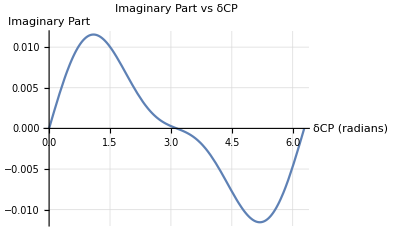

```mathematica
(*Current experimental values from Particle Data Group*)(*Mixing angles in radians*)theta12=33.45*Degree;   (*θ12*)
theta13=8.62*Degree;    (*θ13*)
theta23=42.1*Degree;    (*θ23*)

(*Define cosine and sine functions*)
c12=Cos[theta12];s12=Sin[theta12];
c13=Cos[theta13];s13=Sin[theta13];
c23=Cos[theta23];s23=Sin[theta23];

(*The imaginary part expression from previous calculation*)
imagExpression=2 c12^2 c13^2 c23^2 s13^2 s23^2 Cos[dcp] Sin[dcp]+c12 c13^3 c23^2 s12 s13 s23 Sin[dcp]-c12 c13^2 c23 s12 s13 s23^3 Sin[dcp];

(*Simplify the expression*)
imagExpressionSimplified=Simplify[imagExpression];

(*Plot for dcp from 0 to 2π*)
Plot[imagExpressionSimplified,{dcp,0,2 Pi},PlotLabel->"Imaginary Part vs δCP",AxesLabel->{"δCP (radians)","Imaginary Part"},GridLines->Automatic,PlotRange->All]
```